```mathematica
Clear["Global`*"]
```

```mathematica
SetDirectory[$UserDocumentsDirectory];
```

```mathematica
<<JLink`;
InstallJava[];
ReinstallJava[JVMArguments->"-Xmx2048m"]
```

LinkObject[…]

```mathematica
ax=Import["TestKaggle4K.csv"];gt=Drop[ax,1]
```

{{1595,23,1,1,318,26941,5031,0,0,9,2,0,1,25123,1,6,212,37},{2142,13,1,46,172,49374,6825,0,0,10,1,0,1,866,3,6,212,1086},{2858,2,3,62,15,38435,9475,0,0,2,1,0,1,25123,1,6,212,37},{5049,11,3,205,385,46963,16664,0,0,5,1,0,1,12920,5,6,212,37},4354,{10983,11,3,205,135,36086,36484,0,0,9,2,2,1,26321,1,2,198,1623},{10984,11,3,205,135,36086,36484,0,0,3,2,0,1,8228,1,2,198,371},{11004,11,3,205,385,46963,36537,1,0,3,2,0,1,8270,1,2,198,390},{11068,34,3,205,354,21728,36780,0,0,9,2,0,1,1829,1,2,198,1167}}
 |  |  |  |

```mathematica
e=Transpose[gt];
```

```mathematica
INTERPRETAR O HISTOGRAMA;
```

```mathematica
dd=200 {1,2,2,2,2,3,4,5,5,5,5,5}
```

{200,400,400,400,400,600,800,1000,1000,1000,1000,1000}

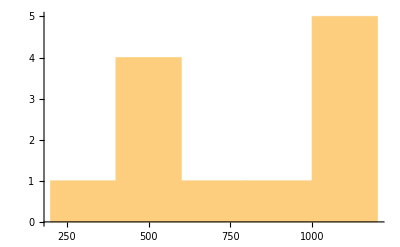

```mathematica
Histogram[dd,5]
```

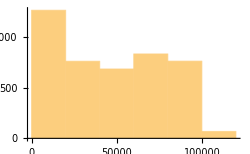
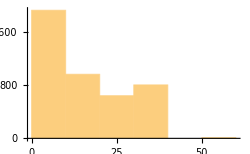
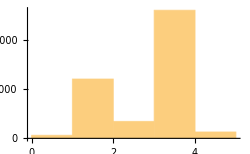
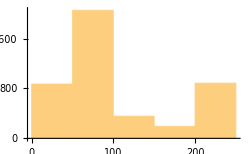
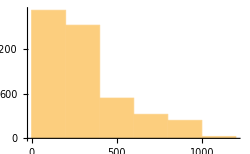
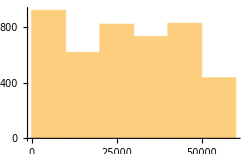
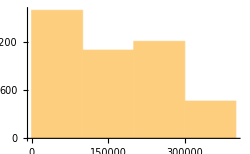
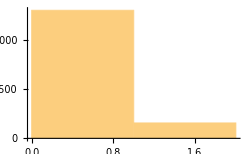
{{1,id,-Graphics-,0.124535},{2,site_name,-Graphics-,0.622076},{3,posa_continent,-Graphics-,-0.64865},{4,user_location_country,-Graphics-,0.586841},{5,user_location_region,-Graphics-,0.9436},{6,user_location_city,-Graphics-,-0.0378383},{7,user_id,-Graphics-,0.111196},{8,is_mobile,-Graphics-,2.53014},{9,is_package,-Graphics-,2.68892},{10,channel,-Graphics-,-0.441077},{11,srch_adults_cnt,-Graphics-,2.08013},{12,srch_children_cnt,-Graphics-,2.82111},{13,srch_rm_cnt,-Graphics-,6.69256},{14,srch_destination_id,-Graphics-,1.57614},{15,srch_destination_type_id,-Graphics-,0.441799},{16,hotel_continent,-Graphics-,-1.96262},{17,hotel_country,-Graphics-,-0.327221},{18,hotel_market,-Graphics-,0.177936}}

```mathematica
{#,ax[[1]][[#]],Histogram[e[[#]],5,ImageSize->250],N[Skewness[e[[#]]]]}&/@Table[k,{k,1,Dimensions[e][[1]],1}]
```

```mathematica
VARIÁVEIS SELECIONADAS;
```

```mathematica
fr={3,4,8,9,12,16};Dimensions[fr]
```

{6}

```mathematica
Selected=e[[#]]&/@fr;Dimensions[Selected]
```

{6,4362}

```mathematica
THRESHOLD PARA RULE PRUNING;
```

```mathematica
threshold=0.01;
```

```mathematica
AJUSTAR AS CLASSES;
```

```mathematica
VARIAVEL 1;
```

```mathematica
f={Flatten[Position[Selected[[1]],x_/;x<Mean[e[[5]]]]],Flatten[Position[e[[5]],x_/;x≥Mean[e[[5]]]]]}
```

{{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100,101,102,103,104,105,106,107,108,109,110,111,112,113,114,115,116,117,118,119,120,121,122,123,124,125,126,127,128,129,130,131,132,133,134,135,136,137,138,139,140,141,142,143,144,145,146,147,148,149,150,151,152,153,154,155,156,157,158,159,160,161,162,163,164,165,166,167,168,169,170,171,172,173,174,175,176,177,178,179,180,181,182,183,184,185,186,187,188,189,190,191,192,193,194,195,196,197,198,199,200,201,202,203,204,205,206,207,208,209,210,211,212,213,214,215,216,217,218,219,220,221,222,223,224,225,226,227,228,229,230,231,232,233,234,235,236,237,238,239,240,241,242,243,244,245,246,247,248,249,250,251,252,253,254,255,256,257,258,259,260,261,262,263,264,265,266,267,268,269,270,271,272,273,274,275,276,277,278,279,280,281,282,283,284,285,286,287,288,289,290,291,292,293,294,295,296,297,298,299,300,301,302,303,304,305,306,307,308,309,310,311,312,313,314,315,316,317,318,319,320,321,322,323,324,325,326,327,328,329,330,331,332,333,334,335,336,337,338,339,340,341,342,343,344,345,346,347,348,349,350,351,352,353,354,355,356,357,358,359,360,361,362,363,364,365,366,367,368,369,370,371,372,373,374,375,376,377,378,379,380,381,382,383,384,385,386,387,388,389,390,391,392,393,394,395,396,397,398,399,400,401,402,403,404,405,406,407,408,409,410,411,412,413,414,415,416,417,418,419,420,421,422,423,424,425,426,427,428,429,430,431,432,433,434,435,436,437,438,439,440,441,442,443,444,445,446,447,448,449,450,451,452,453,454,455,456,457,458,459,460,461,462,463,464,465,466,467,468,469,470,471,472,473,474,475,476,477,478,479,480,481,482,483,484,485,486,487,488,489,490,491,492,493,494,495,496,497,498,499,500,501,502,503,504,505,506,507,508,509,510,511,512,513,514,515,516,517,518,519,520,521,522,523,524,525,526,527,528,529,530,531,532,533,534,535,536,537,538,539,540,541,542,543,544,545,546,547,548,549,550,551,552,553,554,555,556,557,558,559,560,561,562,563,564,565,566,567,568,569,570,571,572,573,574,575,576,577,578,579,580,581,582,583,584,585,586,587,588,589,590,591,592,593,594,595,596,597,598,599,600,601,602,603,604,605,606,607,608,609,610,611,612,613,614,615,616,617,618,619,620,621,622,623,624,625,626,627,628,629,630,631,632,633,634,635,636,637,638,639,640,641,642,643,644,645,646,647,648,649,650,651,652,653,654,655,656,657,658,659,660,661,662,663,664,665,666,667,668,669,670,671,672,673,674,675,676,677,678,679,680,681,682,683,684,685,686,687,688,689,690,691,692,693,694,695,696,697,698,699,700,701,702,703,704,705,706,707,708,709,710,711,712,713,714,715,716,717,718,719,720,721,722,723,724,725,726,727,728,729,730,731,732,733,734,735,736,737,738,739,740,741,742,743,744,745,746,747,748,749,750,751,752,753,754,755,756,757,758,759,760,761,762,763,764,765,766,767,768,769,770,771,772,773,774,775,776,777,778,779,780,781,782,783,784,785,786,787,788,789,790,791,792,793,794,795,796,797,798,799,800,801,802,803,804,805,806,807,808,809,810,811,812,813,814,815,816,817,818,819,820,821,822,823,824,825,826,827,828,829,830,831,832,833,834,835,836,837,838,839,840,841,842,843,844,845,846,847,848,849,850,851,852,853,854,855,856,857,858,859,860,861,862,863,864,865,866,867,868,869,870,871,872,873,874,875,876,877,878,879,880,881,882,883,884,885,886,887,888,889,890,891,892,893,894,895,896,897,898,899,900,901,902,903,904,905,906,907,908,909,910,911,912,913,914,915,916,917,918,919,920,921,922,923,924,925,926,927,928,929,930,931,932,933,934,935,936,937,938,939,940,941,942,943,944,945,946,947,948,949,950,951,952,953,954,955,956,957,958,959,960,961,962,963,964,965,966,967,968,969,970,971,972,973,974,975,976,977,978,979,980,981,982,983,984,985,986,987,988,989,990,991,992,993,994,995,996,997,998,999,1000,1001,1002,1003,1004,1005,1006,1007,1008,1009,1010,1011,1012,1013,1014,1015,1016,1017,1018,1019,1020,1021,1022,1023,1024,1025,1026,1027,1028,1029,1030,1031,1032,1033,1034,1035,1036,1037,1038,1039,1040,1041,1042,1043,1044,1045,1046,1047,1048,1049,1050,1051,1052,1053,1054,1055,1056,1057,1058,1059,1060,1061,1062,1063,1064,1065,1066,1067,1068,1069,1070,1071,1072,1073,1074,1075,1076,1077,1078,1079,1080,1081,1082,1083,1084,1085,1086,1087,1088,1089,1090,1091,1092,1093,1094,1095,1096,1097,1098,1099,1100,1101,1102,1103,1104,1105,1106,1107,1108,1109,1110,1111,1112,1113,1114,1115,1116,1117,1118,1119,1120,1121,1122,1123,1124,1125,1126,1127,1128,1129,1130,1131,1132,1133,1134,1135,1136,1137,1138,1139,1140,1141,1142,1143,1144,1145,1146,1147,1148,1149,1150,1151,1152,1153,1154,1155,1156,1157,1158,1159,1160,1161,1162,1163,1164,1165,1166,1167,1168,1169,1170,1171,1172,1173,1174,1175,1176,1177,1178,1179,1180,1181,1182,1183,1184,1185,1186,1187,1188,1189,1190,1191,1192,1193,1194,1195,1196,1197,1198,1199,1200,1201,1202,1203,1204,1205,1206,1207,1208,1209,1210,1211,1212,1213,1214,1215,1216,1217,1218,1219,1220,1221,1222,1223,1224,1225,1226,1227,1228,1229,1230,1231,1232,1233,1234,1235,1236,1237,1238,1239,1240,1241,1242,1243,1244,1245,1246,1247,1248,1249,1250,1251,1252,1253,1254,1255,1256,1257,1258,1259,1260,1261,1262,1263,1264,1265,1266,1267,1268,1269,1270,1271,1272,1273,1274,1275,1276,1277,1278,1279,1280,1281,1282,1283,1284,1285,1286,1287,1288,1289,1290,1291,1292,1293,1294,1295,1296,1297,1298,1299,1300,1301,1302,1303,1304,1305,1306,1307,1308,1309,1310,1311,1312,1313,1314,1315,1316,1317,1318,1319,1320,1321,1322,1323,1324,1325,1326,1327,1328,1329,1330,1331,1332,1333,1334,1335,1336,1337,1338,1339,1340,1341,1342,1343,1344,1345,1346,1347,1348,1349,1350,1351,1352,1353,1354,1355,1356,1357,1358,1359,1360,1361,1362,1363,1364,1365,1366,1367,1368,1369,1370,1371,1372,1373,1374,1375,1376,1377,1378,1379,1380,1381,1382,1383,1384,1385,1386,1387,1388,1389,1390,1391,1392,1393,1394,1395,1396,1397,1398,1399,1400,1401,1402,1403,1404,1405,1406,1407,1408,1409,1410,1411,1412,1413,1414,1415,1416,1417,1418,1419,1420,1421,1422,1423,1424,1425,1426,1427,1428,1429,1430,1431,1432,1433,1434,1435,1436,1437,1438,1439,1440,1441,1442,1443,1444,1445,1446,1447,1448,1449,1450,1451,1452,1453,1454,1455,1456,1457,1458,1459,1460,1461,1462,1463,1464,1465,1466,1467,1468,1469,1470,1471,1472,1473,1474,1475,1476,1477,1478,1479,1480,1481,1482,1483,1484,1485,1486,1487,1488,1489,1490,1491,1492,1493,1494,1495,1496,1497,1498,1499,1500,1501,1502,1503,1504,1505,1506,1507,1508,1509,1510,1511,1512,1513,1514,1515,1516,1517,1518,1519,1520,1521,1522,1523,1524,1525,1526,1527,1528,1529,1530,1531,1532,1533,1534,1535,1536,1537,1538,1539,1540,1541,1542,1543,1544,1545,1546,1547,1548,1549,1550,1551,1552,1553,1554,1555,1556,1557,1558,1559,1560,1561,1562,1563,1564,1565,1566,1567,1568,1569,1570,1571,1572,1573,1574,1575,1576,1577,1578,1579,1580,1581,1582,1583,1584,1585,1586,1587,1588,1589,1590,1591,1592,1593,1594,1595,1596,1597,1598,1599,1600,1601,1602,1603,1604,1605,1606,1607,1608,1609,1610,1611,1612,1613,1614,1615,1616,1617,1618,1619,1620,1621,1622,1623,1624,1625,1626,1627,1628,1629,1630,1631,1632,1633,1634,1635,1636,1637,1638,1639,1640,1641,1642,1643,1644,1645,1646,1647,1648,1649,1650,1651,1652,1653,1654,1655,1656,1657,1658,1659,1660,1661,1662,1663,1664,1665,1666,1667,1668,1669,1670,1671,1672,1673,1674,1675,1676,1677,1678,1679,1680,1681,1682,1683,1684,1685,1686,1687,1688,1689,1690,1691,1692,1693,1694,1695,1696,1697,1698,1699,1700,1701,1702,1703,1704,1705,1706,1707,1708,1709,1710,1711,1712,1713,1714,1715,1716,1717,1718,1719,1720,1721,1722,1723,1724,1725,1726,1727,1728,1729,1730,1731,1732,1733,1734,1735,1736,1737,1738,1739,1740,1741,1742,1743,1744,1745,1746,1747,1748,1749,1750,1751,1752,1753,1754,1755,1756,1757,1758,1759,1760,1761,1762,1763,1764,1765,1766,1767,1768,1769,1770,1771,1772,1773,1774,1775,1776,1777,1778,1779,1780,1781,1782,1783,1784,1785,1786,1787,1788,1789,1790,1791,1792,1793,1794,1795,1796,1797,1798,1799,1800,1801,1802,1803,1804,1805,1806,1807,1808,1809,1810,1811,1812,1813,1814,1815,1816,1817,1818,1819,1820,1821,1822,1823,1824,1825,1826,1827,1828,1829,1830,1831,1832,1833,1834,1835,1836,1837,1838,1839,1840,1841,1842,1843,1844,1845,1846,1847,1848,1849,1850,1851,1852,1853,1854,1855,1856,1857,1858,1859,1860,1861,1862,1863,1864,1865,1866,1867,1868,1869,1870,1871,1872,1873,1874,1875,1876,1877,1878,1879,1880,1881,1882,1883,1884,1885,1886,1887,1888,1889,1890,1891,1892,1893,1894,1895,1896,1897,1898,1899,1900,1901,1902,1903,1904,1905,1906,1907,1908,1909,1910,1911,1912,1913,1914,1915,1916,1917,1918,1919,1920,1921,1922,1923,1924,1925,1926,1927,1928,1929,1930,1931,1932,1933,1934,1935,1936,1937,1938,1939,1940,1941,1942,1943,1944,1945,1946,1947,1948,1949,1950,1951,1952,1953,1954,1955,1956,1957,1958,1959,1960,1961,1962,1963,1964,1965,1966,1967,1968,1969,1970,1971,1972,1973,1974,1975,1976,1977,1978,1979,1980,1981,1982,1983,1984,1985,1986,1987,1988,1989,1990,1991,1992,1993,1994,1995,1996,1997,1998,1999,2000,2001,2002,2003,2004,2005,2006,2007,2008,2009,2010,2011,2012,2013,2014,2015,2016,2017,2018,2019,2020,2021,2022,2023,2024,2025,2026,2027,2028,2029,2030,2031,2032,2033,2034,2035,2036,2037,2038,2039,2040,2041,2042,2043,2044,2045,2046,2047,2048,2049,2050,2051,2052,2053,2054,2055,2056,2057,2058,2059,2060,2061,2062,2063,2064,2065,2066,2067,2068,2069,2070,2071,2072,2073,2074,2075,2076,2077,2078,2079,2080,2081,2082,2083,2084,2085,2086,2087,2088,2089,2090,2091,2092,2093,2094,2095,2096,2097,2098,2099,2100,2101,2102,2103,2104,2105,2106,2107,2108,2109,2110,2111,2112,2113,2114,2115,2116,2117,2118,2119,2120,2121,2122,2123,2124,2125,2126,2127,2128,2129,2130,2131,2132,2133,2134,2135,2136,2137,2138,2139,2140,2141,2142,2143,2144,2145,2146,2147,2148,2149,2150,2151,2152,2153,2154,2155,2156,2157,2158,2159,2160,2161,2162,2163,2164,2165,2166,2167,2168,2169,2170,2171,2172,2173,2174,2175,2176,2177,2178,2179,2180,2181,2182,2183,2184,2185,2186,2187,2188,2189,2190,2191,2192,2193,2194,2195,2196,2197,2198,2199,2200,2201,2202,2203,2204,2205,2206,2207,2208,2209,2210,2211,2212,2213,2214,2215,2216,2217,2218,2219,2220,2221,2222,2223,2224,2225,2226,2227,2228,2229,2230,2231,2232,2233,2234,2235,2236,2237,2238,2239,2240,2241,2242,2243,2244,2245,2246,2247,2248,2249,2250,2251,2252,2253,2254,2255,2256,2257,2258,2259,2260,2261,2262,2263,2264,2265,2266,2267,2268,2269,2270,2271,2272,2273,2274,2275,2276,2277,2278,2279,2280,2281,2282,2283,2284,2285,2286,2287,2288,2289,2290,2291,2292,2293,2294,2295,2296,2297,2298,2299,2300,2301,2302,2303,2304,2305,2306,2307,2308,2309,2310,2311,2312,2313,2314,2315,2316,2317,2318,2319,2320,2321,2322,2323,2324,2325,2326,2327,2328,2329,2330,2331,2332,2333,2334,2335,2336,2337,2338,2339,2340,2341,2342,2343,2344,2345,2346,2347,2348,2349,2350,2351,2352,2353,2354,2355,2356,2357,2358,2359,2360,2361,2362,2363,2364,2365,2366,2367,2368,2369,2370,2371,2372,2373,2374,2375,2376,2377,2378,2379,2380,2381,2382,2383,2384,2385,2386,2387,2388,2389,2390,2391,2392,2393,2394,2395,2396,2397,2398,2399,2400,2401,2402,2403,2404,2405,2406,2407,2408,2409,2410,2411,2412,2413,2414,2415,2416,2417,2418,2419,2420,2421,2422,2423,2424,2425,2426,2427,2428,2429,2430,2431,2432,2433,2434,2435,2436,2437,2438,2439,2440,2441,2442,2443,2444,2445,2446,2447,2448,2449,2450,2451,2452,2453,2454,2455,2456,2457,2458,2459,2460,2461,2462,2463,2464,2465,2466,2467,2468,2469,2470,2471,2472,2473,2474,2475,2476,2477,2478,2479,2480,2481,2482,2483,2484,2485,2486,2487,2488,2489,2490,2491,2492,2493,2494,2495,2496,2497,2498,2499,2500,2501,2502,2503,2504,2505,2506,2507,2508,2509,2510,2511,2512,2513,2514,2515,2516,2517,2518,2519,2520,2521,2522,2523,2524,2525,2526,2527,2528,2529,2530,2531,2532,2533,2534,2535,2536,2537,2538,2539,2540,2541,2542,2543,2544,2545,2546,2547,2548,2549,2550,2551,2552,2553,2554,2555,2556,2557,2558,2559,2560,2561,2562,2563,2564,2565,2566,2567,2568,2569,2570,2571,2572,2573,2574,2575,2576,2577,2578,2579,2580,2581,2582,2583,2584,2585,2586,2587,2588,2589,2590,2591,2592,2593,2594,2595,2596,2597,2598,2599,2600,2601,2602,2603,2604,2605,2606,2607,2608,2609,2610,2611,2612,2613,2614,2615,2616,2617,2618,2619,2620,2621,2622,2623,2624,2625,2626,2627,2628,2629,2630,2631,2632,2633,2634,2635,2636,2637,2638,2639,2640,2641,2642,2643,2644,2645,2646,2647,2648,2649,2650,2651,2652,2653,2654,2655,2656,2657,2658,2659,2660,2661,2662,2663,2664,2665,2666,2667,2668,2669,2670,2671,2672,2673,2674,2675,2676,2677,2678,2679,2680,2681,2682,2683,2684,2685,2686,2687,2688,2689,2690,2691,2692,2693,2694,2695,2696,2697,2698,2699,2700,2701,2702,2703,2704,2705,2706,2707,2708,2709,2710,2711,2712,2713,2714,2715,2716,2717,2718,2719,2720,2721,2722,2723,2724,2725,2726,2727,2728,2729,2730,2731,2732,2733,2734,2735,2736,2737,2738,2739,2740,2741,2742,2743,2744,2745,2746,2747,2748,2749,2750,2751,2752,2753,2754,2755,2756,2757,2758,2759,2760,2761,2762,2763,2764,2765,2766,2767,2768,2769,2770,2771,2772,2773,2774,2775,2776,2777,2778,2779,2780,2781,2782,2783,2784,2785,2786,2787,2788,2789,2790,2791,2792,2793,2794,2795,2796,2797,2798,2799,2800,2801,2802,2803,2804,2805,2806,2807,2808,2809,2810,2811,2812,2813,2814,2815,2816,2817,2818,2819,2820,2821,2822,2823,2824,2825,2826,2827,2828,2829,2830,2831,2832,2833,2834,2835,2836,2837,2838,2839,2840,2841,2842,2843,2844,2845,2846,2847,2848,2849,2850,2851,2852,2853,2854,2855,2856,2857,2858,2859,2860,2861,2862,2863,2864,2865,2866,2867,2868,2869,2870,2871,2872,2873,2874,2875,2876,2877,2878,2879,2880,2881,2882,2883,2884,2885,2886,2887,2888,2889,2890,2891,2892,2893,2894,2895,2896,2897,2898,2899,2900,2901,2902,2903,2904,2905,2906,2907,2908,2909,2910,2911,2912,2913,2914,2915,2916,2917,2918,2919,2920,2921,2922,2923,2924,2925,2926,2927,2928,2929,2930,2931,2932,2933,2934,2935,2936,2937,2938,2939,2940,2941,2942,2943,2944,2945,2946,2947,2948,2949,2950,2951,2952,2953,2954,2955,2956,2957,2958,2959,2960,2961,2962,2963,2964,2965,2966,2967,2968,2969,2970,2971,2972,2973,2974,2975,2976,2977,2978,2979,2980,2981,2982,2983,2984,2985,2986,2987,2988,2989,2990,2991,2992,2993,2994,2995,2996,2997,2998,2999,3000,3001,3002,3003,3004,3005,3006,3007,3008,3009,3010,3011,3012,3013,3014,3015,3016,3017,3018,3019,3020,3021,3022,3023,3024,3025,3026,3027,3028,3029,3030,3031,3032,3033,3034,3035,3036,3037,3038,3039,3040,3041,3042,3043,3044,3045,3046,3047,3048,3049,3050,3051,3052,3053,3054,3055,3056,3057,3058,3059,3060,3061,3062,3063,3064,3065,3066,3067,3068,3069,3070,3071,3072,3073,3074,3075,3076,3077,3078,3079,3080,3081,3082,3083,3084,3085,3086,3087,3088,3089,3090,3091,3092,3093,3094,3095,3096,3097,3098,3099,3100,3101,3102,3103,3104,3105,3106,3107,3108,3109,3110,3111,3112,3113,3114,3115,3116,3117,3118,3119,3120,3121,3122,3123,3124,3125,3126,3127,3128,3129,3130,3131,3132,3133,3134,3135,3136,3137,3138,3139,3140,3141,3142,3143,3144,3145,3146,3147,3148,3149,3150,3151,3152,3153,3154,3155,3156,3157,3158,3159,3160,3161,3162,3163,3164,3165,3166,3167,3168,3169,3170,3171,3172,3173,3174,3175,3176,3177,3178,3179,3180,3181,3182,3183,3184,3185,3186,3187,3188,3189,3190,3191,3192,3193,3194,3195,3196,3197,3198,3199,3200,3201,3202,3203,3204,3205,3206,3207,3208,3209,3210,3211,3212,3213,3214,3215,3216,3217,3218,3219,3220,3221,3222,3223,3224,3225,3226,3227,3228,3229,3230,3231,3232,3233,3234,3235,3236,3237,3238,3239,3240,3241,3242,3243,3244,3245,3246,3247,3248,3249,3250,3251,3252,3253,3254,3255,3256,3257,3258,3259,3260,3261,3262,3263,3264,3265,3266,3267,3268,3269,3270,3271,3272,3273,3274,3275,3276,3277,3278,3279,3280,3281,3282,3283,3284,3285,3286,3287,3288,3289,3290,3291,3292,3293,3294,3295,3296,3297,3298,3299,3300,3301,3302,3303,3304,3305,3306,3307,3308,3309,3310,3311,3312,3313,3314,3315,3316,3317,3318,3319,3320,3321,3322,3323,3324,3325,3326,3327,3328,3329,3330,3331,3332,3333,3334,3335,3336,3337,3338,3339,3340,3341,3342,3343,3344,3345,3346,3347,3348,3349,3350,3351,3352,3353,3354,3355,3356,3357,3358,3359,3360,3361,3362,3363,3364,3365,3366,3367,3368,3369,3370,3371,3372,3373,3374,3375,3376,3377,3378,3379,3380,3381,3382,3383,3384,3385,3386,3387,3388,3389,3390,3391,3392,3393,3394,3395,3396,3397,3398,3399,3400,3401,3402,3403,3404,3405,3406,3407,3408,3409,3410,3411,3412,3413,3414,3415,3416,3417,3418,3419,3420,3421,3422,3423,3424,3425,3426,3427,3428,3429,3430,3431,3432,3433,3434,3435,3436,3437,3438,3439,3440,3441,3442,3443,3444,3445,3446,3447,3448,3449,3450,3451,3452,3453,3454,3455,3456,3457,3458,3459,3460,3461,3462,3463,3464,3465,3466,3467,3468,3469,3470,3471,3472,3473,3474,3475,3476,3477,3478,3479,3480,3481,3482,3483,3484,3485,3486,3487,3488,3489,3490,3491,3492,3493,3494,3495,3496,3497,3498,3499,3500,3501,3502,3503,3504,3505,3506,3507,3508,3509,3510,3511,3512,3513,3514,3515,3516,3517,3518,3519,3520,3521,3522,3523,3524,3525,3526,3527,3528,3529,3530,3531,3532,3533,3534,3535,3536,3537,3538,3539,3540,3541,3542,3543,3544,3545,3546,3547,3548,3549,3550,3551,3552,3553,3554,3555,3556,3557,3558,3559,3560,3561,3562,3563,3564,3565,3566,3567,3568,3569,3570,3571,3572,3573,3574,3575,3576,3577,3578,3579,3580,3581,3582,3583,3584,3585,3586,3587,3588,3589,3590,3591,3592,3593,3594,3595,3596,3597,3598,3599,3600,3601,3602,3603,3604,3605,3606,3607,3608,3609,3610,3611,3612,3613,3614,3615,3616,3617,3618,3619,3620,3621,3622,3623,3624,3625,3626,3627,3628,3629,3630,3631,3632,3633,3634,3635,3636,3637,3638,3639,3640,3641,3642,3643,3644,3645,3646,3647,3648,3649,3650,3651,3652,3653,3654,3655,3656,3657,3658,3659,3660,3661,3662,3663,3664,3665,3666,3667,3668,3669,3670,3671,3672,3673,3674,3675,3676,3677,3678,3679,3680,3681,3682,3683,3684,3685,3686,3687,3688,3689,3690,3691,3692,3693,3694,3695,3696,3697,3698,3699,3700,3701,3702,3703,3704,3705,3706,3707,3708,3709,3710,3711,3712,3713,3714,3715,3716,3717,3718,3719,3720,3721,3722,3723,3724,3725,3726,3727,3728,3729,3730,3731,3732,3733,3734,3735,3736,3737,3738,3739,3740,3741,3742,3743,3744,3745,3746,3747,3748,3749,3750,3751,3752,3753,3754,3755,3756,3757,3758,3759,3760,3761,3762,3763,3764,3765,3766,3767,3768,3769,3770,3771,3772,3773,3774,3775,3776,3777,3778,3779,3780,3781,3782,3783,3784,3785,3786,3787,3788,3789,3790,3791,3792,3793,3794,3795,3796,3797,3798,3799,3800,3801,3802,3803,3804,3805,3806,3807,3808,3809,3810,3811,3812,3813,3814,3815,3816,3817,3818,3819,3820,3821,3822,3823,3824,3825,3826,3827,3828,3829,3830,3831,3832,3833,3834,3835,3836,3837,3838,3839,3840,3841,3842,3843,3844,3845,3846,3847,3848,3849,3850,3851,3852,3853,3854,3855,3856,3857,3858,3859,3860,3861,3862,3863,3864,3865,3866,3867,3868,3869,3870,3871,3872,3873,3874,3875,3876,3877,3878,3879,3880,3881,3882,3883,3884,3885,3886,3887,3888,3889,3890,3891,3892,3893,3894,3895,3896,3897,3898,3899,3900,3901,3902,3903,3904,3905,3906,3907,3908,3909,3910,3911,3912,3913,3914,3915,3916,3917,3918,3919,3920,3921,3922,3923,3924,3925,3926,3927,3928,3929,3930,3931,3932,3933,3934,3935,3936,3937,3938,3939,3940,3941,3942,3943,3944,3945,3946,3947,3948,3949,3950,3951,3952,3953,3954,3955,3956,3957,3958,3959,3960,3961,3962,3963,3964,3965,3966,3967,3968,3969,3970,3971,3972,3973,3974,3975,3976,3977,3978,3979,3980,3981,3982,3983,3984,3985,3986,3987,3988,3989,3990,3991,3992,3993,3994,3995,3996,3997,3998,3999,4000,4001,4002,4003,4004,4005,4006,4007,4008,4009,4010,4011,4012,4013,4014,4015,4016,4017,4018,4019,4020,4021,4022,4023,4024,4025,4026,4027,4028,4029,4030,4031,4032,4033,4034,4035,4036,4037,4038,4039,4040,4041,4042,4043,4044,4045,4046,4047,4048,4049,4050,4051,4052,4053,4054,4055,4056,4057,4058,4059,4060,4061,4062,4063,4064,4065,4066,4067,4068,4069,4070,4071,4072,4073,4074,4075,4076,4077,4078,4079,4080,4081,4082,4083,4084,4085,4086,4087,4088,4089,4090,4091,4092,4093,4094,4095,4096,4097,4098,4099,4100,4101,4102,4103,4104,4105,4106,4107,4108,4109,4110,4111,4112,4113,4114,4115,4116,4117,4118,4119,4120,4121,4122,4123,4124,4125,4126,4127,4128,4129,4130,4131,4132,4133,4134,4135,4136,4137,4138,4139,4140,4141,4142,4143,4144,4145,4146,4147,4148,4149,4150,4151,4152,4153,4154,4155,4156,4157,4158,4159,4160,4161,4162,4163,4164,4165,4166,4167,4168,4169,4170,4171,4172,4173,4174,4175,4176,4177,4178,4179,4180,4181,4182,4183,4184,4185,4186,4187,4188,4189,4190,4191,4192,4193,4194,4195,4196,4197,4198,4199,4200,4201,4202,4203,4204,4205,4206,4207,4208,4209,4210,4211,4212,4213,4214,4215,4216,4217,4218,4219,4220,4221,4222,4223,4224,4225,4226,4227,4228,4229,4230,4231,4232,4233,4234,4235,4236,4237,4238,4239,4240,4241,4242,4243,4244,4245,4246,4247,4248,4249,4250,4251,4252,4253,4254,4255,4256,4257,4258,4259,4260,4261,4262,4263,4264,4265,4266,4267,4268,4269,4270,4271,4272,4273,4274,4275,4276,4277,4278,4279,4280,4281,4282,4283,4284,4285,4286,4287,4288,4289,4290,4291,4292,4293,4294,4295,4296,4297,4298,4299,4300,4301,4302,4303,4304,4305,4306,4307,4308,4309,4310,4311,4312,4313,4314,4315,4316,4317,4318,4319,4320,4321,4322,4323,4324,4325,4326,4327,4328,4329,4330,4331,4332,4333,4334,4335,4336,4337,4338,4339,4340,4341,4342,4343,4344,4345,4346,4347,4348,4349,4350,4351,4352,4353,4354,4355,4356,4357,4358,4359,4360,4361,4362},{1,4,5,6,7,8,9,10,11,13,17,18,19,21,23,24,29,32,33,40,41,42,43,44,46,47,48,49,50,51,53,54,55,56,61,67,68,72,73,74,75,76,77,79,80,81,84,85,86,90,91,93,97,99,105,106,108,111,112,114,121,125,126,127,128,130,135,137,139,142,143,144,145,146,150,154,155,156,157,158,159,160,161,162,163,167,171,174,175,181,183,184,188,190,195,196,197,202,203,207,209,210,211,212,213,214,215,216,217,221,222,225,230,232,235,236,237,238,239,256,258,259,260,261,262,269,270,272,278,280,281,282,283,284,285,286,288,289,292,293,298,299,300,302,303,304,305,309,310,313,314,315,316,317,319,321,330,334,336,339,341,342,343,344,345,346,347,348,349,350,352,353,354,355,356,357,358,360,361,363,364,365,369,370,371,372,376,382,383,384,385,389,390,391,394,396,398,399,406,407,408,413,416,418,420,421,423,425,428,429,434,443,444,445,449,450,451,452,453,454,456,457,460,461,462,464,465,466,467,470,471,472,473,474,475,476,477,478,479,481,482,483,484,485,486,487,488,489,490,491,492,493,494,495,496,497,498,499,501,502,503,504,505,506,507,510,511,513,518,519,521,522,523,524,525,526,527,528,529,531,532,536,538,542,543,544,545,546,547,553,554,555,556,557,558,562,563,564,565,566,569,571,572,573,577,578,581,583,586,589,590,591,592,594,596,597,602,603,604,605,606,607,608,609,610,611,612,614,615,616,617,618,619,620,621,622,623,624,625,626,629,630,635,636,641,642,643,644,651,652,653,656,659,660,661,662,664,665,666,670,672,678,679,680,681,682,683,684,685,688,689,691,694,695,696,697,699,701,704,705,706,707,708,709,713,714,717,719,720,721,722,723,724,727,730,732,737,738,740,741,752,754,755,761,763,765,766,768,769,770,771,772,773,774,775,778,779,780,781,782,786,795,798,801,805,809,810,812,819,820,824,825,837,840,849,851,854,855,856,857,859,860,864,865,867,869,871,874,875,880,881,882,883,884,885,886,889,890,893,896,898,903,904,905,906,908,909,910,911,912,915,916,919,923,925,927,930,932,933,934,938,941,942,946,948,949,952,953,957,961,964,974,976,977,988,990,993,994,999,1000,1002,1006,1011,1016,1017,1018,1021,1022,1023,1024,1025,1026,1027,1032,1033,1034,1036,1037,1038,1039,1040,1041,1044,1047,1048,1052,1053,1056,1058,1059,1060,1062,1064,1065,1066,1068,1072,1073,1074,1076,1079,1080,1084,1085,1086,1087,1088,1089,1090,1091,1093,1094,1097,1098,1099,1100,1101,1103,1108,1115,1116,1117,1118,1119,1120,1123,1124,1126,1127,1129,1130,1131,1134,1139,1140,1144,1145,1148,1149,1156,1157,1164,1167,1168,1169,1172,1173,1174,1176,1178,1179,1183,1184,1185,1186,1187,1189,1190,1191,1195,1199,1200,1201,1203,1204,1205,1206,1207,1208,1214,1215,1216,1217,1218,1219,1221,1222,1223,1225,1230,1231,1232,1235,1237,1239,1240,1241,1242,1247,1251,1254,1255,1263,1264,1266,1267,1272,1277,1278,1279,1282,1286,1287,1289,1290,1293,1295,1297,1300,1304,1307,1308,1309,1313,1314,1315,1318,1319,1320,1323,1325,1326,1334,1335,1340,1342,1344,1345,1348,1349,1350,1358,1360,1361,1362,1363,1364,1365,1366,1367,1371,1372,1378,1382,1385,1390,1391,1392,1393,1394,1397,1398,1399,1401,1402,1409,1410,1423,1424,1425,1427,1428,1429,1430,1433,1435,1436,1439,1440,1441,1442,1444,1446,1449,1454,1455,1458,1459,1460,1461,1463,1464,1468,1469,1470,1471,1472,1473,1475,1476,1478,1484,1485,1492,1495,1496,1497,1498,1499,1500,1503,1504,1505,1506,1509,1514,1516,1517,1518,1520,1530,1531,1533,1535,1536,1537,1540,1542,1543,1544,1545,1546,1547,1549,1550,1551,1553,1554,1555,1557,1561,1563,1566,1568,1574,1576,1577,1581,1589,1590,1591,1594,1595,1596,1601,1602,1603,1612,1624,1625,1626,1627,1628,1629,1630,1631,1637,1638,1640,1643,1645,1646,1647,1648,1649,1650,1652,1656,1657,1658,1659,1660,1661,1664,1666,1669,1670,1671,1672,1673,1679,1680,1682,1683,1684,1687,1688,1690,1691,1692,1697,1698,1701,1710,1712,1713,1715,1722,1725,1728,1729,1730,1731,1732,1733,1734,1736,1737,1738,1739,1740,1741,1742,1746,1748,1749,1750,1752,1760,1761,1762,1765,1769,1771,1772,1773,1774,1776,1778,1780,1781,1782,1783,1784,1785,1788,1789,1793,1794,1795,1796,1797,1798,1800,1803,1804,1805,1806,1807,1810,1811,1812,1813,1814,1815,1816,1817,1822,1823,1826,1828,1829,1831,1832,1835,1836,1842,1843,1845,1846,1847,1851,1852,1853,1855,1859,1862,1863,1864,1865,1866,1868,1869,1870,1871,1872,1873,1876,1878,1879,1880,1883,1886,1892,1893,1897,1898,1899,1904,1905,1906,1907,1910,1911,1912,1913,1914,1915,1916,1917,1922,1923,1924,1927,1929,1932,1938,1939,1940,1941,1942,1944,1945,1946,1947,1948,1949,1950,1951,1952,1953,1954,1955,1956,1957,1958,1960,1962,1963,1969,1973,1975,1977,1981,1983,1984,1985,1986,1987,1989,1992,1994,1995,1996,2003,2004,2005,2006,2007,2013,2016,2020,2026,2027,2028,2030,2031,2032,2033,2034,2035,2036,2037,2040,2041,2044,2050,2053,2055,2057,2058,2062,2063,2064,2065,2067,2068,2069,2070,2071,2072,2073,2074,2076,2077,2081,2082,2083,2084,2086,2088,2089,2091,2093,2095,2096,2099,2100,2101,2103,2105,2108,2110,2112,2117,2118,2121,2124,2125,2132,2133,2138,2143,2149,2151,2152,2156,2159,2160,2161,2162,2163,2167,2168,2169,2171,2174,2175,2176,2177,2178,2179,2181,2183,2186,2187,2188,2189,2190,2191,2195,2196,2198,2202,2203,2204,2205,2206,2207,2208,2212,2213,2215,2222,2223,2225,2227,2228,2231,2234,2235,2239,2240,2246,2247,2248,2249,2252,2255,2259,2260,2261,2264,2265,2267,2268,2278,2285,2286,2287,2288,2289,2291,2293,2295,2296,2297,2298,2299,2303,2304,2305,2306,2307,2308,2312,2315,2316,2318,2319,2320,2321,2322,2325,2326,2327,2328,2329,2330,2331,2332,2333,2334,2337,2338,2339,2340,2341,2352,2353,2357,2358,2360,2361,2362,2363,2366,2367,2368,2370,2375,2376,2378,2379,2380,2381,2387,2388,2389,2390,2392,2394,2395,2396,2398,2399,2401,2402,2403,2404,2408,2409,2411,2412,2419,2422,2425,2427,2428,2430,2431,2433,2435,2438,2439,2440,2448,2449,2451,2454,2455,2456,2457,2458,2461,2464,2465,2466,2467,2472,2474,2475,2477,2478,2485,2487,2490,2491,2492,2494,2495,2496,2497,2502,2508,2509,2510,2512,2514,2515,2522,2523,2526,2527,2530,2531,2532,2533,2537,2538,2539,2542,2545,2546,2548,2559,2561,2566,2567,2569,2575,2576,2577,2580,2582,2583,2584,2585,2586,2588,2589,2592,2593,2594,2595,2597,2598,2601,2602,2606,2607,2613,2614,2615,2618,2620,2622,2626,2635,2638,2639,2644,2645,2646,2647,2648,2649,2650,2651,2652,2653,2657,2658,2659,2662,2663,2666,2668,2673,2674,2675,2676,2677,2682,2683,2689,2690,2691,2692,2699,2701,2704,2705,2706,2711,2713,2714,2715,2718,2719,2720,2721,2727,2729,2735,2740,2741,2742,2745,2746,2748,2749,2750,2752,2753,2756,2757,2758,2759,2760,2761,2762,2763,2768,2772,2773,2778,2780,2782,2783,2785,2786,2787,2791,2792,2793,2794,2799,2800,2803,2804,2805,2806,2807,2811,2814,2815,2816,2817,2818,2819,2820,2821,2822,2823,2824,2825,2826,2827,2828,2833,2836,2837,2840,2843,2844,2845,2846,2847,2848,2850,2852,2853,2856,2859,2860,2862,2864,2865,2866,2867,2868,2874,2875,2876,2879,2881,2882,2883,2884,2887,2892,2893,2894,2898,2899,2900,2903,2904,2905,2909,2915,2917,2919,2920,2925,2930,2931,2932,2933,2938,2950,2951,2952,2954,2957,2958,2965,2966,2967,2968,2970,2971,2973,2979,2982,2983,2984,2988,2990,2993,2994,2996,2997,3000,3001,3002,3009,3010,3011,3012,3013,3015,3016,3020,3021,3022,3024,3025,3028,3031,3034,3037,3038,3039,3040,3045,3052,3053,3054,3055,3059,3060,3061,3064,3065,3066,3067,3068,3069,3070,3072,3073,3074,3075,3080,3082,3085,3087,3088,3090,3091,3092,3093,3095,3096,3098,3100,3101,3102,3104,3105,3106,3107,3108,3109,3110,3111,3112,3113,3114,3118,3121,3122,3123,3129,3130,3139,3140,3141,3142,3143,3144,3148,3151,3158,3163,3164,3165,3166,3167,3173,3175,3176,3178,3179,3187,3188,3189,3191,3193,3198,3201,3202,3205,3207,3208,3209,3210,3211,3212,3213,3215,3224,3225,3226,3229,3230,3231,3232,3235,3239,3241,3242,3244,3246,3249,3253,3254,3255,3260,3261,3264,3269,3270,3275,3277,3278,3284,3285,3286,3289,3290,3291,3292,3293,3295,3297,3298,3299,3300,3304,3308,3312,3314,3315,3317,3318,3319,3321,3324,3325,3326,3329,3330,3331,3332,3333,3334,3338,3344,3345,3349,3351,3354,3356,3357,3359,3360,3361,3362,3363,3364,3365,3366,3367,3369,3370,3376,3378,3379,3380,3382,3383,3384,3387,3388,3389,3392,3393,3394,3395,3396,3397,3399,3400,3401,3403,3407,3408,3412,3413,3414,3415,3416,3417,3418,3419,3421,3429,3430,3431,3432,3433,3435,3436,3439,3442,3443,3444,3448,3449,3450,3458,3467,3469,3472,3482,3484,3485,3489,3492,3496,3500,3502,3503,3505,3506,3508,3510,3511,3514,3515,3516,3517,3518,3520,3521,3523,3525,3526,3531,3539,3541,3542,3544,3545,3546,3548,3549,3550,3552,3554,3555,3557,3558,3561,3562,3563,3565,3569,3571,3572,3573,3574,3575,3579,3581,3587,3588,3592,3594,3596,3597,3598,3599,3601,3602,3603,3604,3606,3607,3613,3614,3615,3616,3617,3619,3622,3623,3627,3630,3631,3634,3637,3639,3640,3641,3645,3646,3647,3648,3650,3652,3653,3654,3655,3656,3657,3663,3665,3670,3673,3675,3676,3677,3678,3679,3680,3681,3682,3683,3685,3686,3687,3688,3689,3690,3692,3694,3697,3699,3700,3701,3702,3703,3704,3705,3706,3707,3709,3711,3714,3719,3720,3723,3724,3726,3727,3729,3730,3731,3732,3735,3737,3738,3739,3741,3743,3744,3745,3746,3748,3749,3750,3751,3752,3753,3755,3756,3757,3758,3759,3763,3767,3769,3771,3774,3775,3776,3781,3784,3785,3786,3788,3789,3790,3791,3792,3795,3796,3797,3798,3801,3802,3803,3806,3807,3810,3817,3819,3826,3828,3829,3830,3831,3832,3833,3834,3840,3841,3842,3845,3846,3847,3848,3851,3854,3855,3856,3857,3858,3859,3860,3863,3865,3867,3869,3871,3873,3874,3877,3878,3879,3883,3884,3885,3889,3890,3891,3897,3898,3899,3900,3901,3902,3904,3906,3917,3918,3919,3920,3921,3922,3926,3927,3928,3929,3930,3934,3935,3936,3938,3939,3940,3942,3943,3947,3950,3957,3958,3959,3961,3962,3963,3966,3983,3984,3993,3995,3996,3997,3998,3999,4000,4001,4002,4005,4006,4007,4012,4014,4016,4017,4018,4019,4020,4021,4024,4026,4027,4028,4029,4031,4032,4033,4034,4035,4036,4037,4038,4039,4043,4044,4050,4051,4052,4053,4056,4057,4063,4064,4065,4066,4073,4075,4076,4077,4079,4081,4082,4083,4086,4087,4089,4090,4091,4092,4093,4094,4095,4096,4100,4101,4102,4103,4105,4109,4110,4111,4112,4115,4117,4133,4134,4136,4137,4138,4139,4140,4144,4145,4146,4147,4148,4149,4150,4151,4152,4153,4154,4156,4157,4159,4161,4162,4169,4170,4171,4172,4173,4174,4175,4176,4177,4178,4182,4183,4184,4186,4190,4191,4193,4194,4195,4196,4197,4198,4204,4205,4209,4210,4211,4212,4213,4221,4224,4225,4226,4227,4228,4229,4230,4231,4235,4236,4237,4239,4241,4242,4244,4246,4249,4252,4253,4255,4258,4266,4267,4268,4269,4270,4271,4281,4285,4286,4288,4289,4290,4291,4294,4296,4298,4299,4300,4304,4305,4309,4313,4321,4323,4326,4332,4334,4335,4337,4338,4339,4340,4341,4342,4343,4344,4345,4346,4347,4348,4349,4350,4355,4357,4358,4361,4362}}

```mathematica
z1=Flatten[Dimensions[f[[#]]]&/@Table[k,{k,1,Dimensions[f][[1]],1}]]
```

{4362,2164}

```mathematica
z11=N[z1[[#]]/Total[z1]]&/@Table[k,{k,1,Dimensions[f][[1]],1}]
```

{0.668403,0.331597}

```mathematica
InfoGain1=Max[z11]
```

0.668403

```mathematica
VARIAVEL 2;
```

```mathematica
e22=Selected[[2]][[f[[#]]]]&/@{1,2}
```

{{1,46,62,205,69,66,66,68,68,148,69,205,69,24,198,59,205,208,69,3,69,46,69,48,66,93,93,198,63,66,3,66,205,46,205,54,66,66,66,66,50,230,66,1,1,69,69,66,1,1,1,3,1,69,1,195,149,149,3,3,1,3,3,190,231,231,66,1,66,198,46,66,69,69,69,66,205,205,1,1,66,133,133,1,1,66,133,228,228,69,77,75,205,66,66,66,66,66,77,205,235,235,163,194,46,77,3,66,119,119,66,66,190,69,66,3,28,190,66,66,69,46,66,46,69,205,69,69,66,69,190,190,190,62,69,1,69,1,1,190,133,1,48,48,205,205,205,205,205,66,66,205,103,99,205,1,66,1,1,1,1,1,1,66,48,46,66,3,66,1,66,70,62,69,205,80,190,190,133,198,66,205,66,69,46,46,66,205,66,69,66,205,205,66,48,48,77,5,66,66,190,32,69,66,0,0,77,133,69,205,69,77,191,205,205,66,66,72,163,190,66,77,190,205,1,1,1,1,1,182,45,1,93,62,32,32,1,69,146,163,3,3,66,190,66,66,66,190,162,1,66,205,133,133,1,1,214,69,66,66,69,69,52,66,66,66,66,133,215,215,66,77,91,133,66,66,66,1,66,69,1,1,1,1,1,12,231,1,205,66,66,66,205,133,133,66,0,205,205,205,95,66,66,66,205,190,66,66,66,66,205,66,69,205,205,205,69,66,69,3,182,66,66,66,66,66,66,66,205,66,119,119,190,205,66,12,163,190,1,23,66,66,66,66,182,182,182,182,182,182,66,66,66,66,66,66,69,66,190,66,66,3,69,69,205,66,163,66,205,205,69,1,66,66,66,66,52,3,3,3,66,66,154,154,205,66,190,190,69,69,69,154,154,66,93,68,66,66,66,205,66,66,66,205,205,66,66,69,3,3,3,3,69,190,5,66,190,1,3,69,68,190,1,66,68,55,1,115,115,198,80,3,3,1,5,190,205,205,66,46,46,46,1,205,66,205,48,66,1,68,68,66,48,48,190,1,32,3,133,77,68,68,0,48,48,48,77,3,3,69,69,195,66,66,66,66,66,66,1,24,46,1,205,205,77,48,66,69,66,66,66,205,77,77,69,205,12,205,1,235,205,130,1,1,1,69,69,205,235,205,205,66,48,205,133,66,66,66,66,205,66,77,66,66,66,66,69,205,1,205,46,46,76,231,66,69,93,48,66,66,133,205,66,66,77,77,1,205,205,205,205,205,69,205,205,205,66,48,190,190,190,205,66,66,66,66,205,205,69,190,1,205,205,133,66,66,69,69,133,29,69,222,69,66,1,1,235,66,66,69,66,66,133,69,1,1,205,133,66,66,66,66,69,205,66,66,66,1,215,63,63,63,66,77,77,77,77,77,77,69,69,69,1,32,77,77,188,188,12,66,93,190,93,93,66,66,62,66,66,66,66,12,69,66,133,133,66,66,190,66,66,66,69,66,190,69,5,3,69,66,69,69,3,46,66,66,87,3,66,66,179,48,66,66,66,163,163,115,66,69,69,69,69,66,205,62,66,182,66,66,205,46,87,163,163,163,163,3,66,66,69,46,3,66,66,69,1,66,205,46,133,133,66,69,5,80,1,163,66,48,48,66,66,66,66,163,66,163,47,69,163,205,155,66,66,231,66,66,235,69,46,3,3,3,3,3,68,46,46,46,66,69,133,68,66,3,46,46,133,3,1,66,68,46,66,205,133,63,69,1,182,205,205,205,205,3,3,69,77,77,77,1,119,133,46,77,3,3,1,46,46,46,46,3,77,1,1,69,133,133,68,66,66,66,66,79,3,66,12,12,46,46,46,141,3,46,3,29,205,205,3,46,46,66,66,3,3,85,3,66,133,133,133,133,133,133,215,3,3,69,133,133,133,133,3,3,124,46,69,133,69,3,3,1,69,77,69,3,69,1,66,66,66,6,205,163,66,205,46,46,46,72,133,1,50,3,5,3,3,69,69,69,77,77,77,68,46,133,1,77,3,3,46,194,133,69,66,69,3,3,3,3,215,215,215,1,3,69,1,66,69,1,1,63,69,1,46,46,63,3,3,133,205,3,69,3,68,3,3,66,133,46,66,66,133,66,66,69,66,66,66,66,205,205,55,205,205,66,69,66,133,69,69,1,222,222,66,66,5,5,69,66,133,99,66,66,48,48,48,48,48,66,116,69,66,66,66,63,66,66,66,133,19,66,133,133,133,69,133,215,133,133,66,66,46,46,46,46,77,77,46,69,76,3,133,68,103,46,46,55,195,66,218,218,218,205,1,66,66,70,195,55,55,55,55,55,55,55,55,55,55,69,69,205,66,66,66,205,1,46,205,66,66,66,55,55,130,130,214,66,52,66,66,222,66,205,66,66,205,66,66,215,205,69,77,77,133,208,66,46,133,66,66,205,235,66,66,46,66,195,66,205,148,32,69,66,66,69,46,69,205,80,205,66,133,133,66,182,182,182,230,205,1,133,133,205,66,77,3,205,205,205,205,205,69,69,205,205,205,205,66,1,66,69,63,69,69,133,69,69,69,3,3,195,46,80,80,133,66,148,235,3,205,66,66,75,75,66,66,66,66,55,66,133,3,32,32,66,66,1,66,3,3,205,133,3,77,77,69,28,66,66,69,66,66,69,198,66,12,55,28,133,215,215,215,215,182,149,63,63,205,80,80,214,77,62,66,66,69,69,1,205,66,66,69,1,1,1,3,3,3,3,66,69,69,66,1,1,1,3,69,69,69,66,205,133,66,66,66,66,66,69,66,23,66,66,69,134,66,66,66,66,133,66,141,95,205,63,63,52,66,66,0,0,0,55,55,55,55,66,133,55,205,1,133,66,12,133,1,1,1,205,66,66,133,133,69,66,66,66,11,32,66,190,190,12,12,205,205,66,55,66,69,154,66,24,66,66,205,66,66,133,133,66,205,133,66,32,69,66,66,63,66,66,226,141,133,1,48,205,66,66,66,214,66,69,66,26,26,26,26,26,26,69,205,55,133,66,162,32,66,32,141,69,77,214,63,66,66,50,133,3,66,66,66,66,133,66,66,66,226,66,68,1,1,205,205,66,66,46,130,46,119,133,133,133,133,66,66,66,66,77,66,66,66,66,47,133,3,69,69,0,32,69,66,23,66,66,69,133,69,154,66,66,66,46,194,154,66,66,133,133,133,133,133,133,133,133,133,133,133,133,66,66,66,66,205,205,205,205,133,52,205,66,69,69,52,66,32,32,77,69,66,1,1,1,3,1,77,66,66,124,124,1,1,66,66,66,69,69,66,133,69,69,133,133,80,69,66,66,69,69,66,205,69,66,66,66,80,133,133,93,66,66,66,66,28,235,235,46,46,230,198,231,205,205,205,205,179,66,104,66,66,66,66,66,205,205,63,133,235,133,133,77,205,68,205,69,1,205,66,133,133,46,3,3,3,66,66,205,205,133,77,3,66,69,66,66,66,69,5,69,69,69,77,69,66,66,66,66,69,46,32,69,69,66,66,133,66,133,66,66,66,66,66,205,66,66,58,133,205,205,66,205,66,215,66,24,24,231,205,66,141,133,66,133,133,133,66,66,69,217,119,69,69,205,62,66,66,66,66,205,205,133,205,3,133,133,133,133,133,66,63,66,205,66,205,133,133,46,133,133,62,69,66,66,69,69,69,66,69,141,3,133,133,133,66,66,66,205,5,66,205,52,69,69,66,66,66,63,66,69,23,205,66,69,69,46,205,69,215,66,55,69,238,66,66,5,205,66,69,69,69,154,214,46,46,214,1,77,3,205,69,1,46,66,66,69,133,77,77,66,66,133,133,0,77,69,13,205,46,133,133,133,133,133,66,66,66,1,46,205,205,62,69,133,3,3,133,66,46,69,133,66,66,1,133,131,131,66,69,69,66,66,66,205,66,205,205,66,69,66,70,70,205,46,66,69,69,66,66,66,133,133,133,205,133,66,66,66,205,46,3,66,99,55,55,55,69,133,69,66,63,66,3,69,205,66,133,69,69,69,205,69,66,3,3,205,205,133,168,63,215,215,66,66,46,46,205,66,66,66,69,46,66,66,66,133,66,66,205,69,215,69,69,69,69,46,46,66,66,66,66,66,133,6,133,182,69,66,66,66,3,3,182,182,66,69,222,3,3,69,66,52,66,205,205,66,46,133,69,69,69,46,69,66,66,63,66,34,66,69,68,215,182,205,62,205,215,69,69,69,69,66,80,66,1,191,66,69,182,66,69,3,154,205,214,214,66,3,133,85,85,133,66,66,69,66,32,66,190,133,55,66,66,205,182,66,66,158,69,182,182,182,182,182,182,66,66,66,66,215,66,66,63,103,69,133,69,66,66,66,133,66,80,80,205,46,66,205,66,66,1,46,46,205,63,63,66,69,69,205,215,66,69,69,66,66,205,77,133,66,69,3,141,66,66,66,205,235,133,66,66,133,205,66,66,66,66,66,69,66,66,66,66,205,69,205,182,23,23,205,133,69,69,69,133,1,46,28,66,66,69,46,195,66,66,3,34,66,47,66,205,119,66,69,66,23,133,205,66,66,66,66,85,215,69,205,66,66,205,66,205,205,215,69,205,5,66,182,215,133,133,69,52,119,119,209,0,208,70,70,191,205,69,133,66,66,46,133,23,66,66,205,66,66,205,205,205,205,205,205,205,66,182,215,215,28,66,66,77,69,69,66,52,66,66,215,66,66,66,66,205,68,66,66,66,66,154,69,69,46,229,179,66,63,63,66,133,66,91,195,181,66,133,0,66,66,23,66,205,133,1,48,115,55,55,55,55,55,55,66,66,194,66,198,66,77,65,65,3,70,77,3,3,66,3,3,1,133,1,69,46,119,3,77,3,3,12,68,68,68,69,133,3,3,66,66,66,46,205,28,3,1,205,205,205,205,205,66,66,133,55,66,3,130,77,66,66,66,215,66,66,71,66,66,3,1,182,23,3,68,68,68,68,68,1,68,3,66,46,182,182,133,77,0,0,0,0,66,3,46,46,46,68,3,68,66,205,205,66,66,67,205,205,29,29,1,46,69,3,66,66,70,23,1,1,1,1,66,3,77,0,0,148,1,46,46,1,66,63,3,3,69,69,133,77,66,205,205,205,63,119,66,66,133,133,205,23,68,68,68,68,3,46,77,77,1,1,133,68,66,69,66,69,69,77,77,77,5,3,3,68,77,69,69,1,1,1,3,46,1,133,233,68,68,3,66,66,66,66,66,133,3,66,66,115,115,115,115,115,115,115,115,181,29,63,63,63,205,215,66,1,3,46,46,46,133,133,133,133,69,69,23,68,133,69,69,3,1,1,1,1,133,133,68,68,68,3,1,3,66,66,11,46,77,133,1,205,1,68,133,0,185,133,133,1,179,77,1,46,69,3,68,63,77,190,66,66,133,68,66,77,69,3,3,3,46,69,66,1,68,133,133,133,205,133,1,68,46,205,205,66,66,66,133,48,48,71,66,69,1,69,3,77,46,23,69,215,1,3,3,167,167,167,198,3,0,63,3,69,205,3,77,69,68,1,66,3,133,68,133,133,69,69,77,66,198,66,66,133,1,1,1,205,133,68,68,46,194,3,3,3,133,69,5,77,133,46,1,1,69,133,6,1,69,46,46,3,46,46,46,46,46,133,75,206,1,1,66,80,66,3,1,69,66,46,46,3,133,133,69,69,3,3,1,1,46,46,66,66,69,69,66,66,66,66,205,205,197,197,77,23,3,205,69,198,66,133,205,205,133,3,1,1,1,46,133,66,133,69,3,3,3,3,1,66,1,1,235,46,46,133,133,77,69,69,188,68,69,46,69,66,117,117,117,202,1,66,66,66,69,154,205,66,179,66,66,48,66,115,115,235,66,70,1,205,66,66,46,1,1,69,158,158,66,133,69,46,205,133,1,47,23,3,182,3,3,46,46,46,46,46,46,182,133,133,69,66,68,205,205,66,69,77,77,69,69,69,1,1,1,182,133,205,205,66,205,66,66,66,69,1,66,133,46,3,69,66,133,133,66,205,205,205,205,205,66,46,3,133,66,205,133,66,66,66,66,66,66,66,66,66,66,66,46,46,133,66,205,66,133,198,205,205,205,66,66,66,205,66,205,77,69,32,3,66,66,66,66,205,133,133,133,66,133,205,80,66,66,66,66,66,66,66,66,66,66,66,205,32,32,80,80,66,205,48,32,205,66,66,69,205,66,66,69,205,205,69,69,46,46,46,0,3,133,133,69,3,3,231,66,46,46,66,66,66,66,66,195,66,66,69,133,66,66,66,62,62,62,230,66,205,1,66,66,231,133,215,66,133,93,69,12,69,205,205,205,205,205,66,74,28,69,69,77,77,77,46,46,46,66,46,32,191,191,66,66,133,133,66,133,12,93,93,63,1,133,23,205,66,66,77,77,1,1,1,1,46,66,205,205,205,205,66,77,133,133,69,69,66,66,66,66,215,215,215,69,66,23,54,26,26,69,46,69,3,66,66,3,1,1,1,66,1,205,1,63,205,66,205,46,66,205,133,23,133,205,1,1,133,133,69,69,205,55,205,190,77,54,66,66,66,66,77,66,69,28,66,66,66,66,66,66,69,133,205,133,5,66,66,1,66,66,52,133,205,69,62,66,66,66,66,66,46,46,205,66,66,1,69,69,66,205,205,205,205,215,46,198,66,66,66,214,66,66,66,69,198,66,205,66,66,133,133,133,133,133,69,28,28,77,69,77,205,205,205,69,66,205,66,214,1,1,66,77,69,55,62,69,46,46,3,205,205,66,205,66,1,1,69,69,46,133,12,66,66,205,66,230,46,69,205,66,154,66,218,66,66,80,69,66,91,66,66,66,1,66,215,66,23,23,23,23,206,66,66,66,66,235,46,46,66,66,1,3,28,52,46,46,46,66,66,66,32,32,32,205,69,77,66,215,205,69,69,3,3,3,3,205,62,1,55,93,69,66,32,32,149,69,69,69,32,66,66,69,66,154,3,66,77,77,3,205,66,77,205,205,69,69,69,205,205,205,133,133,133,66,28,1,66,66,66,103,103,93,46,66,66,66,66,66,66,66,66,66,133,133,69,69,69,69,69,66,133,46,125,69,133,66,46,133,66,133,66,205,168,1,205,55,133,133,69,69,69,69,69,66,133,66,66,235,66,3,63,69,66,77,205,190,133,133,66,66,48,133,66,66,66,133,6,66,66,66,66,66,66,66,66,103,32,66,119,205,66,66,66,66,205,205,205,66,66,66,66,85,3,66,231,24,85,85,85,6,69,69,29,29,215,69,85,66,5,85,66,85,85,85,55,205,99,66,46,66,66,66,205,205,66,66,66,85,99,66,69,1,1,29,155,69,69,198,85,0,66,85,66,198,85,66,205,214,66,188,85,56,85,85,66,62,205,80,149,85,205,205,70,85,69,69,215,69,69,66,69,70,136,85,66,186,133,205,85,69,85,85,66,173,66,66,66,69,205,99,66,66,66,99,205,3,69,66,66,66,66,66,198,80,77,205,205,66,85,66,66,66,85,195,55,70,66,85,66,66,77,66,205,205,66,66,66,46,66,55,55,68,68,3,46,6,66,68,68,68,68,68,68,48,66,66,66,85,66,142,68,68,85,115,66,1,46,68,66,66,46,46,99,195,195,68,68,69,69,69,69,68,85,66,205,69,69,46,85,155,29,29,69,46,80,66,66,69,69,77,69,46,46,46,85,62,66,63,63,63,63,63,63,63,1,1,1,1,66,85,69,77,188,188,85,205,205,66,66,66,66,66,66,77,69,69,198,3,80,80,55,91,5,69,80,58,66,80,80,198,80,80,205,80,69,80,80,69,80,66,80,80,80,198,80,3,80,205,149,1,69,149,80,80,69,80,28,69,190,80,198,66,80,80,80,69,149,0,77,85,69,69,228,69,228,205,48,46,28,69,69,69,55,69,149,69,69,62,69,228,69,69,66,198,66,55,206,235,228,48,46,198,46,46,69,46,66,48,28,77,12,48,228,69,69,12,66,69,46,1,1,66,68,215,55,1,69,66,48,198,69,66,5,190,46,66,69,66,69,205,69,62,52,66,66,26,32,214,206,0,66,66,215,66,66,63,55,206,46,205,206,66,77,179,66,66,66,69,69,1,163,205,163,62,93,66,46,62,69,66,48,69,69,206,69,1,205,66,66,62,5,66,46,129,66,69,69,148,55,66,66,66,215,66,182,205,77,55,66,3,69,69,66,182,23,66,66,69,66,77,205,205,66,66,182,80,66,46,12,46,69,55,148,46,181,205,68,3,77,133,1,68,115,205,66,66,68,1,1,63,77,69,215,1,1,1,48,69,68,77,46,133,1,206,215,66,77,66,48,66,66,1,66,66,69,46,32,206,205,66,188,66,3,23,63,66,205,133,66,205,46,205,205,66,69,182,12,69,66,1,205,66,69,69,69,214,69,66,68,48,1,66,5,205,66,77,66,69,66,66,179,205,57,57,205,205,205,205,205,205,66,205,205,205,215,205,77,66,66,66,66,66,66,66,205,205,205,205,3,205,205,205,3,205,205,66,69,69,3,3,66,205,205,205,3,3,66,66,205,66,66,68,68,205,205,205,3,3,3,3,3,66,66,205,205,205,205,205,66,3,3,205,205,205,69,66,69,69,69,205,46,46,46,119,3,205,66,69,3,205,205,205,205,205,205,205,66,3,66,205,205,205,205,205,205,205,66,66,205,205,205,205,205,205,205,205,205,66,205,1,205,66,205,205,205,66,205,205,57,57,57,205,205,205,205,205,205,66,66,66,66,205,66,66,66,205,205,205,66,66,205,66,205,205,205,205,205,3,3,3,66,205,205,205,205,66,205,205,205,3,3,66,68,66,66,66,66,205,3,66,205,66,68,205,205,66,205,205,66,205,205,205,205,205,205,205,205,205,205,205,205,205,66,66,69,205,66,205,205,205,205,66,205,205,205,205,205,205,205,205,205,205,205,205,205,205,205,205,205,205,66,66,205,205,205,205,205,205,66,205,205,205,205,205,205,205,205,205,205,205,205,205,205,205,205,205,205,66,205,205,205,205,205,205,205,205,205,205,205,205,66,205,205,66,66,205,205,205,205,205,205,205,205,205,205,205,205,205,66,205,205,205,205,66,66,66,66,66,66,66,66,66,66,3,202,205,205,3,66,205,205,205,133,3,3,3,205,205,77,205,215,205,205,3,205,46,66,66,66,66,66,77,205,205,66,205,205,46,46,77,215,66,230,3,205,205,205,205,205,66,205,205,205,205,205,205,205,205,66,205,66,205,66,205,205,205,66,66,66,205,66,66,66,66,66,66,66,205,66,66,205,0,66,205,205,205,205,205,205,205,205,205,205,205,205,205,205,205,205,205,205,205,66,205,205,28,205,205,205,205,205,205,23,66,66,205,205,205,205,205,205,205,205,205,205,205,205,69,66,66,205,66,205,205,205,205,205,66,205,205,205,205,66,66,66,205,205,205,66,205,205,205,205,205,205,205,205,205,66,205,205,205,205,205,66,66,205,205,205,205,205,66,66,205,205,66,205,205,205,205,205,205,205,205,205,39,205,66,205,66,66,205,205,205,205,205,66,66,66,205,66,205,205,205,39,205,205,205,205,205,205,66,66,205,205,66,205,205,205,205,205,205,66,205,205,205,205,205,205,205,66,205,66,66,66,66,205,205,205,205,205,66,205,205,205,205,205,205,205,205,205,66,66,205,66,205,66,29,205,205,205,205,205,66,205,205,69,66,66,205,205,205,205,205,205,205,205,205,205,205,205,66,205,205,191,191,205,205,205,205,66,205,205,205,205,205,205,205,205,205,66,205,205,205,205,205,205,205},{1,205,69,66,66,68,68,148,69,69,205,208,69,69,69,48,63,66,205,66,50,230,66,1,69,69,66,1,1,1,1,69,1,195,1,66,1,66,69,69,69,66,205,1,1,66,1,1,66,69,77,205,66,77,46,77,66,66,66,69,69,69,205,69,69,69,69,69,1,1,48,48,205,205,66,99,205,1,66,1,1,1,1,1,1,66,66,69,205,66,66,69,205,69,48,48,77,32,69,77,69,205,69,77,191,205,205,66,66,66,77,1,182,1,32,32,1,69,146,1,69,66,66,69,69,215,215,77,1,69,1,1,1,1,1,12,1,205,66,205,205,205,205,66,66,66,205,66,66,69,205,205,205,69,69,182,66,205,12,1,66,66,66,66,182,182,182,182,182,182,66,66,66,66,66,69,66,66,66,69,69,205,205,205,69,1,66,66,154,154,205,69,69,69,66,68,66,66,66,66,69,69,66,1,69,68,1,68,115,115,1,1,205,66,1,68,68,66,48,48,1,32,77,68,68,48,48,48,77,69,69,195,66,66,66,66,66,66,1,46,1,205,205,77,48,66,69,66,66,66,205,77,77,69,205,12,205,1,205,130,1,1,1,69,69,205,205,48,66,66,66,77,66,66,66,66,69,205,1,46,46,69,48,205,66,66,77,77,1,69,205,205,205,66,48,205,66,66,66,66,69,1,205,205,69,69,69,69,1,66,69,66,66,69,1,205,66,69,205,66,66,66,1,215,63,63,63,77,77,77,77,77,77,69,69,69,1,32,77,77,12,66,66,66,66,12,69,66,66,66,69,69,69,66,69,69,46,66,66,66,48,115,66,69,69,69,69,66,205,182,66,205,163,163,163,163,66,69,66,66,69,1,66,205,66,69,1,66,48,48,66,66,66,66,69,205,66,66,69,46,69,68,66,1,68,66,205,63,69,1,182,205,205,205,205,69,77,77,77,1,77,77,69,68,66,12,12,46,205,205,66,66,215,69,69,69,1,69,77,69,69,1,6,205,66,46,46,1,50,69,69,69,77,77,77,68,1,77,46,69,69,215,215,215,1,69,1,66,69,1,69,1,63,205,69,68,66,46,66,66,69,66,66,205,66,69,69,69,66,69,99,69,66,66,69,215,66,66,77,77,69,68,195,205,1,66,195,55,55,55,55,55,55,69,69,205,66,66,205,1,46,205,66,130,130,66,66,205,66,205,66,215,69,77,77,208,66,66,205,66,66,195,32,69,66,66,69,46,69,205,205,66,66,182,182,182,230,1,77,69,69,205,205,205,205,66,69,69,69,69,69,69,195,66,148,66,66,66,66,32,32,205,77,77,69,66,69,66,69,66,12,215,215,215,215,182,63,63,205,77,69,69,1,66,66,69,1,1,1,69,69,66,1,1,1,69,69,69,205,66,66,69,66,69,66,66,66,66,205,66,0,0,205,1,66,12,205,69,66,66,32,12,12,205,66,69,66,66,66,66,66,32,69,66,66,226,1,48,205,66,66,69,69,205,32,32,69,77,66,66,50,66,66,226,66,68,1,1,205,205,130,46,66,77,66,69,69,0,32,69,66,66,69,69,154,66,66,66,66,66,205,205,205,205,205,69,69,32,32,77,69,1,1,77,1,1,66,69,69,66,69,69,69,66,66,69,69,66,69,66,66,66,66,230,205,205,205,205,179,66,66,66,66,66,63,77,68,205,69,205,205,205,77,66,69,66,69,69,69,69,77,69,66,66,66,69,32,69,69,66,66,66,205,66,205,215,66,205,66,66,69,69,69,205,66,205,205,66,69,66,66,69,69,69,66,69,66,66,205,205,69,69,66,66,66,63,69,69,69,46,205,69,215,69,66,205,66,69,69,69,1,77,205,69,1,66,69,77,77,66,77,69,46,1,205,205,69,69,66,131,131,66,69,69,66,66,205,66,205,205,66,69,66,46,69,69,66,66,66,205,46,99,69,69,66,63,66,69,66,69,69,69,205,69,66,205,205,215,215,66,66,46,46,66,69,46,66,66,66,66,205,69,215,69,69,69,69,66,66,6,182,69,66,66,182,182,69,66,66,205,205,69,69,69,69,66,69,68,215,182,205,205,215,69,69,69,69,66,191,66,69,69,205,85,85,69,66,32,66,66,205,182,158,69,182,182,182,182,182,182,215,66,66,69,69,66,46,66,205,66,66,46,46,205,63,63,66,69,69,205,215,66,69,69,66,66,77,66,69,205,66,205,66,69,66,66,66,205,69,182,205,69,69,69,69,46,195,66,66,205,69,205,215,69,205,66,205,66,205,205,215,69,205,182,215,69,208,191,69,66,66,66,66,205,66,205,205,205,205,205,205,205,66,215,215,77,69,69,66,66,215,66,66,205,66,66,154,69,69,229,66,66,66,195,66,66,205,48,115,66,66,77,77,1,1,69,77,12,68,68,68,69,66,66,66,205,1,205,205,205,205,205,66,55,130,77,66,66,66,215,66,66,1,68,68,68,68,68,1,68,182,182,77,46,46,68,68,66,66,205,205,46,69,1,1,1,1,77,148,1,66,63,69,69,77,66,205,46,77,77,1,1,68,69,69,69,77,77,77,68,77,69,69,1,1,1,68,68,66,66,66,66,66,66,66,115,115,115,115,115,115,115,115,63,63,63,205,215,69,69,69,69,1,1,1,1,68,68,68,1,46,77,1,205,1,68,1,179,77,1,69,68,63,77,66,66,68,66,77,69,46,69,1,68,68,205,66,48,48,66,69,69,77,69,215,1,0,63,69,77,69,68,1,66,68,69,69,77,66,1,1,205,68,68,69,77,1,1,69,6,1,69,46,46,1,1,66,66,1,69,69,69,1,1,66,66,69,69,66,205,205,77,205,69,66,66,69,1,66,1,77,69,69,69,69,66,117,117,117,1,66,69,154,205,66,66,66,115,115,1,205,69,158,158,69,205,1,182,182,69,66,69,77,77,69,69,69,1,1,1,182,66,205,66,69,1,46,69,205,205,205,205,205,66,205,66,66,66,66,66,66,205,205,205,66,77,69,32,66,66,66,205,205,66,66,205,32,32,66,205,32,205,66,69,205,69,205,205,69,69,46,46,46,69,66,46,66,195,66,69,66,66,66,230,66,205,1,215,66,69,12,69,205,205,66,69,69,77,77,77,46,46,46,66,46,32,191,191,66,66,12,63,1,205,77,77,1,1,1,1,66,205,205,77,69,69,66,66,215,215,215,69,69,46,69,66,1,1,1,66,1,46,66,205,205,1,1,69,69,205,77,77,69,66,66,69,66,66,1,66,69,1,69,69,205,205,215,66,66,66,69,66,205,66,69,77,69,77,69,205,1,1,77,69,69,46,46,1,1,69,69,46,12,66,230,46,69,66,154,66,69,66,1,66,215,66,206,46,66,66,1,46,46,46,66,32,32,32,205,69,77,215,205,69,69,205,1,69,32,32,69,69,69,32,66,69,154,66,77,77,205,66,77,205,205,69,69,69,205,205,205,66,66,66,66,66,66,69,69,69,69,69,66,69,46,1,69,69,69,69,69,66,63,69,77,205,66,66,66,6,66,66,32,66,66,66,66,205,205,205,66,66,66,6,69,69,215,69,85,66,66,55,99,66,66,66,66,99,66,69,69,69,0,85,66,85,85,85,85,205,205,69,69,215,69,69,69,136,85,66,186,69,173,69,99,66,66,99,205,69,66,66,66,77,205,205,66,85,66,195,66,77,66,66,55,68,68,46,6,66,68,68,68,68,68,68,66,66,68,115,66,1,68,66,66,99,195,195,69,69,69,69,68,85,205,69,69,85,69,46,69,69,77,69,46,46,46,85,66,1,1,1,1,66,69,77,85,66,66,66,77,69,69,69,205,69,69,205,1,69,69,69,66,69,0,77,69,69,69,205,48,69,69,69,55,69,69,69,69,69,69,206,69,66,48,77,12,48,69,69,12,69,1,1,68,215,69,66,48,69,46,69,66,69,205,69,66,32,215,66,206,205,66,77,179,66,66,69,69,1,205,163,69,66,48,69,69,69,66,66,46,69,69,66,215,182,205,77,69,69,66,182,66,69,66,77,205,205,66,12,69,205,77,1,68,115,205,66,66,68,1,1,77,69,215,1,1,1,69,77,1,215,66,77,66,48,66,66,1,66,69,32,66,63,66,66,205,205,205,69,182,12,69,205,69,69,69,69,68,48,1,66,205,66,77,66,69,66,179,205,57,57,205,205,205,215,77,66,66,66,205,205,205,205,205,205,66,69,69,66,205,205,205,66,66,205,68,68,205,66,205,205,205,69,66,69,69,69,205,205,66,69,205,205,205,205,66,205,205,205,205,205,205,205,205,205,205,205,205,205,1,205,205,205,57,57,57,205,205,205,66,66,66,205,205,205,66,66,205,205,205,66,205,205,66,68,66,66,66,66,205,66,205,205,66,205,66,205,205,66,66,69,66,205,205,66,205,205,66,205,205,205,205,205,205,205,205,205,205,205,66,205,205,205,205,205,205,205,205,205,205,66,66,205,205,205,205,205,205,205,205,205,66,205,66,66,66,66,66,66,66,205,205,205,77,215,205,205,205,66,66,66,77,205,66,205,205,46,46,77,215,66,205,205,205,205,205,205,205,205,205,66,66,66,66,0,66,205,205,205,205,205,205,205,205,205,205,205,205,205,205,205,66,205,205,205,66,205,205,205,205,205,205,205,205,205,69,66,66,66,205,205,205,205,205,205,66,66,205,205,205,205,205,205,66,205,205,205,66,66,205,205,66,205,205,205,205,205,205,66,66,205,205,66,66,66,205,66,66,205,205,66,205,205,66,205,66,66,66,205,205,66,205,205,205,205,205,66,205,69,66,205,205,205,205,205,205,191,191,205,205,205,205,66,205,205,205,205,205,66,205,205,205,205}}

```mathematica
f2=Flatten[{Flatten[Position[e22[[#]],x_/;x<Mean[e22[[#]]]]],Flatten[Position[e22[[#]],x_/;x≥Mean[e22[[#]]]]]}&/@{1,2},1]
```

{{1,2,3,5,6,7,8,9,11,13,14,16,19,20,21,22,23,24,25,26,27,29,30,31,32,34,36,37,38,39,40,41,43,44,45,46,47,48,49,50,51,52,53,54,55,59,60,61,62,63,67,68,69,71,72,73,74,75,76,79,80,81,84,85,86,90,91,92,94,95,96,97,98,99,105,106,107,108,111,112,114,115,116,117,119,120,121,122,123,124,125,127,128,129,130,134,135,136,137,138,139,142,143,144,150,151,156,157,158,159,160,161,162,163,164,165,166,167,168,169,170,171,172,173,174,176,181,183,184,185,186,187,189,190,191,194,195,196,197,198,199,200,202,203,204,205,206,207,209,211,212,216,217,218,221,222,225,226,227,228,229,231,232,233,234,235,236,237,238,241,242,243,245,246,247,250,251,255,256,258,259,260,261,262,263,264,265,266,267,271,272,273,275,276,277,278,279,280,281,282,283,284,285,286,288,290,291,292,296,297,301,302,303,304,307,308,309,310,312,313,317,318,319,320,322,323,324,325,326,327,328,330,335,336,339,340,341,342,343,344,351,352,353,354,355,356,357,358,360,361,362,363,364,366,368,371,372,373,374,375,376,377,378,379,380,381,382,386,389,390,391,394,395,396,397,398,399,401,402,403,406,407,408,409,410,411,412,413,415,416,418,419,420,421,423,424,425,426,427,431,432,433,434,435,439,440,441,442,443,445,447,448,449,450,451,452,453,454,456,457,458,460,461,462,463,464,465,466,467,468,469,470,471,473,474,475,476,477,478,479,480,481,482,485,486,487,488,489,490,491,493,494,495,497,499,503,504,505,506,507,512,513,516,517,518,519,521,522,523,524,525,526,527,529,531,532,533,535,536,537,538,539,540,543,544,545,546,547,553,557,558,563,564,565,566,569,571,575,576,577,578,580,581,583,584,585,586,588,589,590,591,592,594,595,596,599,600,601,602,603,605,606,607,608,610,611,612,613,614,615,616,617,618,619,620,621,622,623,624,625,626,629,630,631,633,634,635,636,637,638,639,640,641,642,643,644,647,648,650,651,652,653,654,656,657,658,659,660,661,662,663,664,665,666,667,668,669,670,672,673,674,675,679,680,681,682,683,684,686,687,689,690,692,693,698,699,700,701,702,703,704,705,706,707,708,710,713,714,715,716,717,719,720,721,722,723,724,725,727,729,730,734,735,737,738,740,741,742,743,744,745,746,747,748,749,750,751,752,754,755,756,757,758,760,761,762,763,764,765,768,769,770,776,777,778,779,780,781,782,785,786,787,788,789,790,791,792,793,794,795,796,797,798,801,802,803,804,805,806,807,808,809,810,811,812,813,815,816,817,818,821,822,823,824,825,826,827,828,829,830,838,839,840,845,846,848,849,851,852,853,854,855,856,857,858,859,860,861,862,863,864,867,869,870,871,872,874,875,876,877,878,879,880,881,882,883,884,885,886,887,889,890,891,892,893,896,897,898,899,900,901,902,906,907,908,909,910,911,912,913,914,915,916,917,918,919,920,921,924,925,926,927,928,929,930,932,933,934,936,937,938,939,940,941,942,945,948,949,950,952,953,954,957,958,959,960,961,962,965,966,967,968,969,970,971,972,974,975,976,977,978,979,980,981,983,984,988,993,994,995,996,997,998,999,1000,1001,1002,1003,1004,1006,1008,1009,1010,1012,1017,1018,1019,1020,1022,1023,1024,1025,1026,1027,1028,1029,1030,1031,1032,1033,1035,1036,1037,1039,1040,1042,1043,1044,1045,1046,1050,1051,1052,1053,1055,1057,1058,1060,1061,1064,1065,1066,1069,1070,1072,1073,1076,1077,1078,1079,1081,1084,1085,1086,1087,1088,1089,1090,1092,1094,1097,1103,1107,1108,1109,1115,1116,1121,1122,1123,1124,1125,1126,1127,1129,1130,1131,1132,1133,1135,1136,1137,1139,1142,1144,1145,1146,1147,1148,1149,1150,1151,1152,1153,1155,1156,1157,1158,1159,1160,1161,1162,1163,1166,1167,1168,1169,1170,1171,1172,1173,1174,1175,1176,1178,1179,1180,1181,1189,1190,1192,1193,1195,1196,1197,1198,1199,1200,1201,1203,1204,1205,1206,1207,1208,1209,1210,1211,1212,1213,1214,1215,1216,1217,1218,1219,1220,1221,1222,1223,1224,1227,1228,1229,1230,1231,1232,1233,1234,1235,1236,1237,1239,1240,1241,1242,1244,1246,1248,1249,1250,1251,1252,1253,1254,1255,1256,1257,1258,1259,1260,1262,1264,1266,1267,1269,1270,1271,1273,1274,1277,1278,1279,1280,1281,1282,1283,1286,1287,1290,1291,1292,1293,1295,1296,1297,1298,1300,1301,1304,1307,1308,1309,1310,1311,1312,1313,1314,1318,1319,1321,1322,1323,1325,1326,1327,1328,1329,1330,1331,1332,1333,1334,1336,1338,1340,1341,1342,1344,1345,1347,1348,1349,1350,1352,1353,1354,1355,1356,1358,1359,1360,1362,1363,1364,1365,1368,1369,1370,1372,1378,1379,1380,1381,1382,1383,1384,1385,1386,1387,1389,1390,1391,1392,1393,1394,1395,1396,1397,1398,1399,1401,1403,1404,1405,1406,1409,1410,1423,1424,1425,1426,1432,1434,1435,1436,1437,1438,1439,1440,1441,1442,1443,1444,1445,1446,1447,1448,1449,1450,1451,1454,1455,1456,1457,1458,1459,1460,1461,1463,1464,1467,1468,1469,1470,1471,1472,1473,1475,1476,1477,1478,1479,1482,1483,1484,1485,1486,1487,1490,1491,1500,1502,1503,1504,1505,1506,1509,1514,1516,1518,1519,1521,1524,1525,1526,1527,1528,1529,1533,1534,1535,1536,1537,1538,1539,1540,1541,1542,1543,1544,1545,1546,1547,1548,1549,1550,1551,1552,1553,1554,1555,1556,1557,1559,1561,1562,1563,1564,1565,1567,1568,1569,1573,1575,1577,1578,1579,1582,1585,1589,1590,1591,1594,1595,1597,1598,1599,1600,1601,1606,1612,1613,1614,1616,1620,1623,1624,1625,1626,1627,1628,1629,1630,1631,1633,1637,1638,1639,1641,1642,1644,1645,1646,1647,1648,1649,1650,1651,1652,1653,1655,1656,1657,1658,1660,1662,1663,1664,1666,1667,1668,1670,1671,1672,1673,1676,1677,1679,1680,1681,1683,1684,1685,1686,1687,1688,1690,1691,1692,1693,1696,1697,1698,1699,1701,1707,1708,1709,1710,1711,1714,1715,1717,1718,1720,1721,1722,1724,1725,1726,1730,1731,1732,1733,1734,1735,1737,1740,1741,1742,1743,1744,1746,1747,1748,1749,1750,1751,1752,1758,1759,1760,1762,1763,1764,1766,1767,1768,1769,1771,1772,1773,1774,1775,1776,1778,1780,1781,1782,1784,1785,1786,1787,1792,1795,1796,1797,1798,1800,1801,1802,1803,1804,1805,1806,1807,1809,1810,1812,1814,1815,1816,1817,1818,1819,1820,1821,1822,1823,1824,1826,1829,1830,1831,1832,1833,1834,1837,1838,1840,1841,1842,1843,1844,1845,1848,1849,1851,1852,1853,1854,1855,1856,1857,1858,1859,1860,1861,1862,1863,1867,1870,1871,1872,1873,1874,1875,1876,1877,1879,1880,1882,1883,1884,1889,1890,1892,1893,1895,1896,1897,1898,1899,1900,1903,1904,1905,1908,1909,1911,1918,1919,1920,1921,1923,1924,1925,1927,1929,1930,1931,1932,1934,1935,1936,1938,1939,1941,1942,1943,1944,1945,1947,1948,1949,1950,1951,1954,1955,1956,1957,1958,1960,1962,1963,1964,1966,1967,1968,1972,1973,1976,1977,1978,1979,1980,1981,1982,1983,1984,1985,1987,1990,1991,1994,1995,1996,1998,1999,2000,2001,2002,2003,2004,2006,2007,2008,2009,2010,2011,2012,2015,2016,2017,2018,2021,2022,2023,2024,2025,2027,2029,2030,2032,2036,2038,2039,2044,2045,2049,2051,2052,2055,2057,2058,2059,2061,2062,2063,2065,2066,2074,2078,2079,2080,2081,2082,2083,2084,2085,2086,2087,2089,2090,2091,2092,2094,2095,2096,2097,2098,2100,2101,2102,2105,2106,2107,2108,2110,2111,2114,2116,2117,2118,2119,2120,2123,2124,2126,2127,2128,2129,2130,2131,2132,2133,2135,2137,2138,2139,2140,2141,2142,2143,2144,2145,2146,2147,2148,2149,2151,2152,2153,2155,2156,2157,2158,2159,2160,2161,2162,2163,2165,2166,2167,2168,2169,2170,2172,2173,2174,2180,2181,2183,2184,2185,2187,2188,2189,2190,2192,2193,2194,2195,2196,2197,2198,2200,2201,2202,2203,2204,2205,2206,2207,2208,2209,2210,2211,2215,2216,2217,2218,2219,2220,2221,2222,2223,2224,2225,2226,2227,2228,2231,2232,2233,2236,2237,2238,2239,2240,2241,2242,2243,2244,2245,2246,2247,2248,2249,2250,2251,2252,2253,2254,2256,2257,2258,2259,2260,2261,2262,2263,2264,2265,2267,2268,2272,2274,2275,2279,2280,2281,2282,2283,2284,2285,2286,2287,2288,2289,2291,2292,2293,2294,2295,2296,2297,2298,2299,2300,2301,2302,2303,2304,2305,2306,2307,2308,2309,2310,2311,2312,2315,2316,2317,2318,2319,2320,2321,2322,2324,2325,2326,2336,2337,2338,2339,2342,2343,2344,2345,2346,2347,2352,2353,2354,2355,2357,2358,2359,2360,2361,2362,2363,2366,2367,2368,2369,2370,2371,2372,2373,2374,2375,2376,2378,2380,2381,2383,2387,2389,2390,2391,2392,2393,2394,2395,2396,2398,2399,2401,2402,2403,2404,2405,2406,2407,2408,2409,2410,2411,2412,2418,2419,2420,2423,2424,2425,2427,2428,2429,2430,2431,2432,2433,2434,2435,2436,2437,2438,2440,2441,2442,2447,2448,2449,2450,2451,2453,2454,2455,2456,2457,2458,2459,2461,2464,2465,2466,2467,2469,2470,2472,2473,2474,2477,2478,2479,2481,2482,2483,2485,2486,2487,2489,2490,2491,2492,2494,2495,2496,2497,2498,2499,2500,2501,2502,2503,2504,2506,2508,2509,2510,2511,2512,2513,2514,2515,2516,2517,2518,2519,2522,2523,2524,2525,2526,2527,2528,2529,2530,2531,2532,2533,2534,2535,2536,2537,2542,2543,2544,2546,2548,2553,2554,2555,2556,2557,2559,2561,2562,2563,2564,2565,2566,2567,2568,2569,2571,2572,2575,2576,2577,2579,2580,2581,2582,2583,2588,2589,2590,2591,2592,2595,2597,2598,2599,2600,2604,2605,2606,2608,2609,2610,2611,2612,2613,2616,2618,2619,2622,2623,2624,2625,2627,2628,2629,2630,2631,2632,2633,2634,2638,2639,2640,2643,2644,2645,2646,2647,2648,2649,2650,2651,2652,2657,2659,2660,2661,2662,2663,2664,2666,2667,2668,2669,2672,2678,2679,2680,2682,2685,2686,2687,2688,2689,2690,2691,2692,2693,2694,2695,2696,2697,2699,2701,2707,2708,2709,2711,2713,2714,2715,2716,2717,2718,2719,2720,2725,2728,2729,2730,2731,2732,2733,2734,2735,2736,2737,2738,2739,2741,2742,2743,2744,2745,2747,2748,2750,2751,2752,2754,2755,2756,2759,2760,2761,2762,2763,2764,2765,2768,2769,2770,2772,2773,2774,2775,2776,2777,2778,2779,2781,2782,2783,2785,2786,2787,2788,2789,2790,2792,2794,2795,2796,2800,2802,2803,2804,2805,2811,2812,2813,2814,2815,2816,2817,2818,2819,2820,2821,2822,2823,2824,2827,2828,2831,2833,2834,2835,2836,2837,2839,2841,2842,2843,2844,2845,2846,2847,2848,2849,2850,2855,2856,2859,2860,2861,2862,2863,2864,2868,2869,2870,2871,2872,2873,2874,2875,2876,2877,2878,2879,2880,2881,2882,2883,2884,2885,2887,2888,2890,2892,2893,2896,2899,2900,2903,2904,2906,2909,2910,2911,2912,2913,2914,2915,2916,2917,2918,2919,2920,2921,2922,2923,2924,2925,2929,2930,2931,2932,2933,2934,2935,2938,2939,2940,2941,2942,2943,2944,2945,2946,2948,2949,2950,2951,2952,2953,2959,2961,2962,2963,2965,2966,2967,2968,2970,2972,2973,2979,2980,2981,2982,2983,2984,2988,2989,2991,2993,2994,2995,2996,2997,2998,2999,3000,3001,3002,3003,3006,3008,3009,3010,3011,3012,3013,3015,3016,3017,3019,3021,3022,3024,3026,3028,3029,3030,3031,3032,3033,3034,3035,3036,3037,3038,3040,3041,3042,3043,3044,3046,3047,3048,3049,3051,3052,3053,3054,3055,3056,3057,3058,3059,3060,3061,3062,3063,3064,3065,3066,3067,3069,3070,3071,3074,3075,3076,3077,3078,3079,3081,3082,3083,3084,3085,3086,3087,3088,3090,3091,3092,3093,3094,3095,3096,3097,3099,3100,3101,3102,3103,3105,3106,3109,3110,3111,3118,3119,3120,3121,3122,3123,3126,3127,3128,3129,3130,3131,3132,3133,3134,3135,3136,3139,3140,3141,3142,3143,3144,3146,3148,3150,3151,3153,3155,3158,3160,3163,3164,3165,3166,3167,3168,3170,3171,3173,3174,3175,3176,3177,3178,3183,3184,3185,3187,3188,3189,3191,3192,3193,3194,3195,3196,3197,3198,3199,3201,3202,3205,3206,3207,3208,3212,3213,3214,3215,3216,3217,3218,3220,3221,3222,3223,3224,3225,3226,3227,3228,3230,3231,3232,3233,3234,3235,3236,3237,3238,3239,3242,3243,3244,3245,3246,3249,3250,3251,3252,3254,3255,3256,3257,3258,3260,3261,3263,3264,3265,3266,3267,3269,3270,3273,3275,3276,3277,3278,3279,3280,3282,3284,3287,3288,3289,3290,3292,3293,3294,3295,3296,3298,3299,3303,3304,3305,3306,3307,3309,3310,3311,3312,3315,3316,3317,3320,3321,3322,3323,3324,3325,3326,3328,3329,3332,3333,3334,3335,3336,3337,3339,3340,3341,3342,3343,3344,3345,3346,3349,3350,3351,3352,3353,3354,3355,3356,3357,3358,3359,3360,3361,3362,3363,3364,3365,3366,3367,3368,3369,3370,3371,3372,3373,3375,3376,3377,3379,3380,3381,3382,3383,3384,3385,3386,3390,3391,3392,3393,3394,3395,3396,3397,3398,3400,3401,3402,3403,3405,3406,3407,3408,3409,3410,3411,3412,3413,3414,3415,3416,3417,3418,3419,3420,3421,3422,3423,3424,3425,3426,3427,3428,3429,3430,3431,3432,3433,3434,3435,3436,3439,3442,3443,3444,3445,3446,3447,3448,3449,3450,3452,3453,3454,3455,3456,3457,3458,3459,3460,3461,3462,3463,3465,3466,3468,3469,3470,3471,3472,3473,3474,3475,3476,3477,3479,3480,3481,3484,3485,3487,3488,3489,3490,3491,3492,3494,3496,3497,3498,3499,3500,3502,3503,3504,3505,3506,3508,3511,3512,3513,3514,3515,3516,3517,3518,3520,3521,3522,3523,3525,3526,3527,3529,3530,3534,3535,3537,3538,3539,3540,3541,3542,3543,3544,3545,3546,3548,3549,3550,3551,3552,3553,3554,3555,3556,3557,3559,3560,3561,3562,3563,3565,3566,3567,3569,3570,3571,3572,3573,3575,3576,3577,3578,3579,3580,3581,3584,3585,3586,3588,3589,3590,3591,3593,3596,3597,3599,3600,3601,3602,3603,3604,3608,3609,3610,3611,3612,3613,3614,3615,3616,3617,3619,3620,3622,3623,3624,3625,3626,3627,3629,3630,3631,3633,3634,3635,3636,3638,3641,3642,3643,3644,3645,3646,3647,3649,3650,3651,3652,3653,3654,3657,3658,3660,3661,3662,3663,3664,3665,3666,3668,3671,3672,3673,3675,3676,3679,3680,3681,3682,3683,3684,3685,3686,3688,3689,3690,3691,3692,3693,3694,3695,3697,3700,3701,3702,3703,3704,3705,3706,3707,3708,3709,3710,3711,3714,3716,3717,3718,3719,3720,3723,3725,3728,3729,3731,3732,3733,3734,3736,3737,3738,3739,3741,3742,3743,3744,3745,3746,3747,3749,3750,3751,3752,3753,3754,3757,3758,3765,3771,3772,3773,3774,3775,3776,3777,3778,3783,3787,3790,3791,3792,3793,3794,3795,3799,3800,3801,3802,3804,3805,3806,3807,3811,3812,3813,3814,3815,3816,3817,3823,3824,3825,3829,3830,3831,3832,3833,3835,3836,3837,3839,3841,3842,3843,3851,3852,3853,3861,3862,3872,3874,3876,3880,3883,3884,3885,3892,3893,3894,3895,3897,3898,3899,3903,3904,3906,3912,3913,3914,3915,3920,3924,3925,3926,3927,3928,3929,3930,3931,3933,3934,3936,3937,3940,3943,3957,3958,3959,3961,3966,3985,3986,3993,4012,4025,4028,4029,4043,4048,4049,4050,4051,4052,4053,4054,4055,4056,4057,4058,4062,4063,4068,4069,4070,4073,4078,4080,4081,4082,4083,4084,4085,4086,4089,4092,4093,4094,4096,4098,4104,4113,4115,4117,4121,4122,4123,4125,4126,4127,4128,4129,4130,4131,4133,4134,4136,4137,4157,4160,4167,4168,4169,4182,4183,4184,4186,4192,4197,4198,4199,4203,4213,4219,4220,4226,4227,4230,4240,4242,4244,4245,4251,4252,4253,4255,4259,4266,4267,4270,4277,4285,4287,4288,4289,4290,4296,4306,4307,4309,4311,4312,4318,4321,4322,4323,4336,4345,4355},{4,10,12,15,17,18,28,33,35,42,56,57,58,64,65,66,70,77,78,82,83,87,88,89,93,100,101,102,103,104,109,110,113,118,126,131,132,133,140,141,145,146,147,148,149,152,153,154,155,175,177,178,179,180,182,188,192,193,201,208,210,213,214,215,219,220,223,224,230,239,240,244,248,249,252,253,254,257,268,269,270,274,287,289,293,294,295,298,299,300,305,306,311,314,315,316,321,329,331,332,333,334,337,338,345,346,347,348,349,350,359,365,367,369,370,383,384,385,387,388,392,393,400,404,405,414,417,422,428,429,430,436,437,438,444,446,455,459,472,483,484,492,496,498,500,501,502,508,509,510,511,514,515,520,528,530,534,541,542,548,549,550,551,552,554,555,556,559,560,561,562,567,568,570,572,573,574,579,582,587,593,597,598,604,609,627,628,632,645,646,649,655,671,676,677,678,685,688,691,694,695,696,697,709,711,712,718,726,728,731,732,733,736,739,753,759,766,767,771,772,773,774,775,783,784,799,800,814,819,820,831,832,833,834,835,836,837,841,842,843,844,847,850,865,866,868,873,888,894,895,903,904,905,922,923,931,935,943,944,946,947,951,955,956,963,964,973,982,985,986,987,989,990,991,992,1005,1007,1011,1013,1014,1015,1016,1021,1034,1038,1041,1047,1048,1049,1054,1056,1059,1062,1063,1067,1068,1071,1074,1075,1080,1082,1083,1091,1093,1095,1096,1098,1099,1100,1101,1102,1104,1105,1106,1110,1111,1112,1113,1114,1117,1118,1119,1120,1128,1134,1138,1140,1141,1143,1154,1164,1165,1177,1182,1183,1184,1185,1186,1187,1188,1191,1194,1202,1225,1226,1238,1243,1245,1247,1261,1263,1265,1268,1272,1275,1276,1284,1285,1288,1289,1294,1299,1302,1303,1305,1306,1315,1316,1317,1320,1324,1335,1337,1339,1343,1346,1351,1357,1361,1366,1367,1371,1373,1374,1375,1376,1377,1388,1400,1402,1407,1408,1411,1412,1413,1414,1415,1416,1417,1418,1419,1420,1421,1422,1427,1428,1429,1430,1431,1433,1452,1453,1462,1465,1466,1474,1480,1481,1488,1489,1492,1493,1494,1495,1496,1497,1498,1499,1501,1507,1508,1510,1511,1512,1513,1515,1517,1520,1522,1523,1530,1531,1532,1558,1560,1566,1570,1571,1572,1574,1576,1580,1581,1583,1584,1586,1587,1588,1592,1593,1596,1602,1603,1604,1605,1607,1608,1609,1610,1611,1615,1617,1618,1619,1621,1622,1632,1634,1635,1636,1640,1643,1654,1659,1661,1665,1669,1674,1675,1678,1682,1689,1694,1695,1700,1702,1703,1704,1705,1706,1712,1713,1716,1719,1723,1727,1728,1729,1736,1738,1739,1745,1753,1754,1755,1756,1757,1761,1765,1770,1777,1779,1783,1788,1789,1790,1791,1793,1794,1799,1808,1811,1813,1825,1827,1828,1835,1836,1839,1846,1847,1850,1864,1865,1866,1868,1869,1878,1881,1885,1886,1887,1888,1891,1894,1901,1902,1906,1907,1910,1912,1913,1914,1915,1916,1917,1922,1926,1928,1933,1937,1940,1946,1952,1953,1959,1961,1965,1969,1970,1971,1974,1975,1986,1988,1989,1992,1993,1997,2005,2013,2014,2019,2020,2026,2028,2031,2033,2034,2035,2037,2040,2041,2042,2043,2046,2047,2048,2050,2053,2054,2056,2060,2064,2067,2068,2069,2070,2071,2072,2073,2075,2076,2077,2088,2093,2099,2103,2104,2109,2112,2113,2115,2121,2122,2125,2134,2136,2150,2154,2164,2171,2175,2176,2177,2178,2179,2182,2186,2191,2199,2212,2213,2214,2229,2230,2234,2235,2255,2266,2269,2270,2271,2273,2276,2277,2278,2290,2313,2314,2323,2327,2328,2329,2330,2331,2332,2333,2334,2335,2340,2341,2348,2349,2350,2351,2356,2364,2365,2377,2379,2382,2384,2385,2386,2388,2397,2400,2413,2414,2415,2416,2417,2421,2422,2426,2439,2443,2444,2445,2446,2452,2460,2462,2463,2468,2471,2475,2476,2480,2484,2488,2493,2505,2507,2520,2521,2538,2539,2540,2541,2545,2547,2549,2550,2551,2552,2558,2560,2570,2573,2574,2578,2584,2585,2586,2587,2593,2594,2596,2601,2602,2603,2607,2614,2615,2617,2620,2621,2626,2635,2636,2637,2641,2642,2653,2654,2655,2656,2658,2665,2670,2671,2673,2674,2675,2676,2677,2681,2683,2684,2698,2700,2702,2703,2704,2705,2706,2710,2712,2721,2722,2723,2724,2726,2727,2740,2746,2749,2753,2757,2758,2766,2767,2771,2780,2784,2791,2793,2797,2798,2799,2801,2806,2807,2808,2809,2810,2825,2826,2829,2830,2832,2838,2840,2851,2852,2853,2854,2857,2858,2865,2866,2867,2886,2889,2891,2894,2895,2897,2898,2901,2902,2905,2907,2908,2926,2927,2928,2936,2937,2947,2954,2955,2956,2957,2958,2960,2964,2969,2971,2974,2975,2976,2977,2978,2985,2986,2987,2990,2992,3004,3005,3007,3014,3018,3020,3023,3025,3027,3039,3045,3050,3068,3072,3073,3080,3089,3098,3104,3107,3108,3112,3113,3114,3115,3116,3117,3124,3125,3137,3138,3145,3147,3149,3152,3154,3156,3157,3159,3161,3162,3169,3172,3179,3180,3181,3182,3186,3190,3200,3203,3204,3209,3210,3211,3219,3229,3240,3241,3247,3248,3253,3259,3262,3268,3271,3272,3274,3281,3283,3285,3286,3291,3297,3300,3301,3302,3308,3313,3314,3318,3319,3327,3330,3331,3338,3347,3348,3374,3378,3387,3388,3389,3399,3404,3437,3438,3440,3441,3451,3464,3467,3478,3482,3483,3486,3493,3495,3501,3507,3509,3510,3519,3524,3528,3531,3532,3533,3536,3547,3558,3564,3568,3574,3582,3583,3587,3592,3594,3595,3598,3605,3606,3607,3618,3621,3628,3632,3637,3639,3640,3648,3655,3656,3659,3667,3669,3670,3674,3677,3678,3687,3696,3698,3699,3712,3713,3715,3721,3722,3724,3726,3727,3730,3735,3740,3748,3755,3756,3759,3760,3761,3762,3763,3764,3766,3767,3768,3769,3770,3779,3780,3781,3782,3784,3785,3786,3788,3789,3796,3797,3798,3803,3808,3809,3810,3818,3819,3820,3821,3822,3826,3827,3828,3834,3838,3840,3844,3845,3846,3847,3848,3849,3850,3854,3855,3856,3857,3858,3859,3860,3863,3864,3865,3866,3867,3868,3869,3870,3871,3873,3875,3877,3878,3879,3881,3882,3886,3887,3888,3889,3890,3891,3896,3900,3901,3902,3905,3907,3908,3909,3910,3911,3916,3917,3918,3919,3921,3922,3923,3932,3935,3938,3939,3941,3942,3944,3945,3946,3947,3948,3949,3950,3951,3952,3953,3954,3955,3956,3960,3962,3963,3964,3965,3967,3968,3969,3970,3971,3972,3973,3974,3975,3976,3977,3978,3979,3980,3981,3982,3983,3984,3987,3988,3989,3990,3991,3992,3994,3995,3996,3997,3998,3999,4000,4001,4002,4003,4004,4005,4006,4007,4008,4009,4010,4011,4013,4014,4015,4016,4017,4018,4019,4020,4021,4022,4023,4024,4026,4027,4030,4031,4032,4033,4034,4035,4036,4037,4038,4039,4040,4041,4042,4044,4045,4046,4047,4059,4060,4061,4064,4065,4066,4067,4071,4072,4074,4075,4076,4077,4079,4087,4088,4090,4091,4095,4097,4099,4100,4101,4102,4103,4105,4106,4107,4108,4109,4110,4111,4112,4114,4116,4118,4119,4120,4124,4132,4135,4138,4139,4140,4141,4142,4143,4144,4145,4146,4147,4148,4149,4150,4151,4152,4153,4154,4155,4156,4158,4159,4161,4162,4163,4164,4165,4166,4170,4171,4172,4173,4174,4175,4176,4177,4178,4179,4180,4181,4185,4187,4188,4189,4190,4191,4193,4194,4195,4196,4200,4201,4202,4204,4205,4206,4207,4208,4209,4210,4211,4212,4214,4215,4216,4217,4218,4221,4222,4223,4224,4225,4228,4229,4231,4232,4233,4234,4235,4236,4237,4238,4239,4241,4243,4246,4247,4248,4249,4250,4254,4256,4257,4258,4260,4261,4262,4263,4264,4265,4268,4269,4271,4272,4273,4274,4275,4276,4278,4279,4280,4281,4282,4283,4284,4286,4291,4292,4293,4294,4295,4297,4298,4299,4300,4301,4302,4303,4304,4305,4308,4310,4313,4314,4315,4316,4317,4319,4320,4324,4325,4326,4327,4328,4329,4330,4331,4332,4333,4334,4335,4337,4338,4339,4340,4341,4342,4343,4344,4346,4347,4348,4349,4350,4351,4352,4353,4354,4356,4357,4358,4359,4360,4361,4362},{1,3,4,5,6,7,9,10,13,14,15,16,17,18,20,21,23,24,25,26,27,28,29,30,31,32,33,35,36,37,38,39,40,41,42,44,45,46,47,48,49,50,51,53,54,55,56,57,58,59,60,61,62,64,65,66,67,68,69,70,71,72,75,78,79,80,81,82,83,84,85,86,87,88,90,91,92,94,95,96,97,98,99,100,101,103,104,108,109,110,111,112,114,115,116,117,118,120,121,122,123,124,125,128,129,130,131,132,133,134,135,136,137,139,144,145,146,148,149,150,154,155,157,159,160,161,162,163,164,171,172,173,174,175,176,177,178,179,180,181,185,186,187,188,192,193,194,195,196,197,198,199,200,201,202,203,204,205,206,207,208,211,212,214,215,216,217,218,219,220,221,222,223,224,225,226,227,228,229,230,231,233,234,235,236,237,238,239,240,241,244,245,246,247,248,249,250,252,253,254,256,258,261,262,263,264,265,268,269,270,271,272,273,274,275,276,277,279,280,281,282,283,285,286,287,288,289,290,294,295,297,298,299,300,301,302,305,306,307,308,309,310,311,312,313,314,315,317,318,320,321,322,323,325,326,327,328,329,330,331,332,333,334,335,336,337,338,339,340,341,342,343,344,345,346,347,348,349,350,351,352,353,354,355,356,357,358,359,360,361,363,364,365,366,367,368,371,377,378,379,380,381,382,383,385,386,387,388,389,390,391,392,393,394,395,397,398,399,400,401,402,403,404,405,406,408,409,410,416,417,418,419,420,421,422,423,424,425,426,427,428,431,432,434,435,436,437,438,439,440,441,442,443,445,446,447,448,449,450,451,452,453,454,455,456,457,458,459,460,461,465,466,467,468,469,470,471,472,473,475,476,477,478,479,480,481,482,483,485,486,487,488,489,490,492,493,494,495,497,498,499,500,501,502,505,506,508,509,510,511,512,513,514,515,517,518,520,521,523,526,527,529,531,533,534,535,537,538,540,541,543,544,545,546,547,548,549,552,553,558,559,560,561,566,567,568,569,570,571,572,574,576,577,578,579,580,581,583,584,585,586,587,588,589,590,591,597,598,600,601,602,603,604,605,606,607,608,609,610,611,612,613,614,615,616,617,618,620,621,622,623,624,625,626,627,628,630,631,632,634,635,636,638,639,640,641,642,643,645,646,647,648,649,650,651,652,653,654,655,657,658,660,661,662,663,665,666,667,668,669,670,671,672,673,675,676,677,678,682,683,684,685,686,687,688,689,690,691,692,693,694,696,697,698,699,700,706,707,708,709,710,711,712,713,714,715,716,717,718,719,720,721,722,723,724,725,726,727,728,729,730,731,732,733,740,741,742,743,744,745,746,747,749,753,754,755,756,757,758,759,760,761,762,763,764,765,766,767,768,769,770,771,772,774,777,779,780,781,782,783,785,788,789,790,791,792,793,794,795,796,797,798,801,802,803,804,805,806,807,808,809,810,812,814,815,817,818,819,820,821,822,824,825,826,827,828,829,830,831,832,833,834,837,838,839,842,843,844,845,846,848,851,852,853,854,855,856,857,858,859,861,863,864,865,866,867,868,869,870,871,872,874,875,880,881,882,883,884,885,886,887,888,889,890,892,894,895,896,897,898,899,900,902,903,904,907,908,909,912,913,914,915,916,917,918,924,925,926,927,928,930,931,932,934,935,936,937,938,939,940,944,952,953,954,955,956,957,958,960,961,962,963,965,966,967,968,969,972,973,974,975,976,977,978,979,981,983,984,985,986,987,989,992,993,994,995,996,998,999,1001,1004,1006,1008,1012,1016,1019,1020,1021,1022,1023,1025,1033,1036,1037,1038,1039,1040,1042,1043,1045,1046,1048,1049,1051,1052,1053,1055,1056,1058,1060,1061,1062,1063,1064,1065,1066,1067,1068,1069,1070,1071,1072,1073,1074,1075,1077,1083,1084,1086,1087,1088,1089,1091,1092,1093,1094,1095,1096,1097,1098,1099,1100,1103,1104,1105,1106,1107,1108,1109,1112,1113,1114,1115,1116,1117,1118,1120,1121,1122,1123,1124,1125,1126,1128,1129,1130,1131,1132,1133,1134,1135,1136,1137,1138,1139,1140,1141,1142,1143,1144,1145,1146,1147,1148,1149,1150,1151,1152,1153,1154,1155,1164,1165,1166,1169,1170,1171,1172,1173,1174,1175,1176,1177,1178,1179,1180,1181,1182,1183,1185,1186,1187,1189,1190,1191,1192,1193,1194,1195,1196,1197,1198,1199,1200,1201,1202,1203,1204,1205,1207,1208,1209,1210,1211,1212,1213,1214,1216,1217,1218,1219,1220,1221,1222,1223,1224,1225,1226,1227,1228,1229,1230,1231,1233,1234,1235,1236,1237,1238,1239,1240,1241,1242,1243,1244,1245,1246,1247,1248,1249,1250,1251,1252,1253,1254,1255,1256,1257,1258,1259,1262,1264,1265,1266,1267,1268,1269,1270,1271,1272,1273,1274,1275,1276,1280,1281,1282,1285,1286,1287,1290,1292,1295,1297,1300,1301,1302,1303,1304,1305,1306,1307,1308,1309,1310,1312,1314,1315,1316,1317,1318,1324,1326,1327,1328,1329,1330,1331,1335,1336,1337,1338,1339,1340,1341,1344,1345,1347,1348,1349,1351,1353,1354,1356,1359,1360,1361,1362,1363,1364,1365,1366,1367,1369,1370,1371,1372,1373,1375,1377,1379,1380,1381,1382,1385,1386,1387,1388,1389,1390,1391,1392,1393,1394,1395,1396,1399,1400,1401,1402,1403,1405,1406,1407,1408,1409,1410,1411,1414,1415,1416,1417,1418,1422,1423,1424,1425,1426,1427,1428,1429,1430,1431,1432,1433,1436,1437,1438,1439,1441,1442,1443,1444,1445,1446,1447,1448,1449,1450,1451,1452,1453,1454,1458,1459,1460,1461,1462,1464,1465,1466,1467,1468,1469,1471,1472,1473,1474,1475,1476,1477,1478,1479,1480,1481,1482,1483,1484,1486,1487,1488,1490,1491,1492,1493,1494,1496,1498,1499,1500,1501,1502,1503,1504,1505,1506,1507,1508,1510,1511,1514,1515,1517,1518,1519,1520,1521,1522,1523,1524,1525,1526,1528,1529,1530,1532,1533,1536,1537,1538,1542,1543,1544,1545,1546,1547,1548,1549,1550,1551,1552,1553,1554,1555,1556,1557,1558,1559,1560,1561,1562,1563,1564,1565,1567,1568,1569,1570,1571,1572,1573,1574,1575,1576,1577,1581,1582,1583,1584,1585,1586,1588,1589,1590,1591,1592,1594,1595,1596,1597,1599,1600,1601,1602,1603,1604,1605,1606,1607,1608,1609,1612,1613,1615,1616,1617,1619,1620,1622,1624,1626,1627,1630,1631,1632,1633,1634,1637,1638,1639,1641,1642,1643,1644,1645,1646,1647,1648,1649,1650,1651,1652,1653,1654,1655,1656,1657,1658,1659,1661,1662,1663,1664,1665,1669,1670,1671,1672,1673,1674,1676,1677,1678,1679,1680,1681,1682,1683,1684,1685,1686,1687,1688,1689,1690,1691,1692,1693,1694,1695,1696,1697,1698,1699,1700,1701,1702,1703,1704,1706,1707,1709,1710,1711,1712,1713,1714,1715,1716,1717,1718,1719,1721,1722,1723,1724,1725,1726,1727,1728,1729,1730,1731,1733,1734,1735,1736,1737,1738,1739,1740,1741,1742,1743,1744,1745,1747,1748,1749,1750,1751,1752,1753,1754,1756,1757,1758,1760,1763,1764,1766,1767,1768,1769,1770,1773,1774,1775,1776,1777,1778,1779,1780,1781,1782,1783,1784,1788,1789,1790,1791,1793,1794,1795,1796,1799,1800,1801,1803,1804,1805,1808,1809,1810,1811,1812,1813,1814,1816,1817,1818,1819,1820,1821,1823,1824,1825,1826,1827,1828,1829,1830,1831,1832,1833,1834,1835,1836,1840,1842,1843,1845,1846,1847,1848,1849,1850,1851,1852,1854,1855,1856,1857,1858,1861,1862,1867,1868,1869,1870,1877,1878,1879,1880,1884,1885,1887,1888,1890,1894,1895,1896,1897,1898,1901,1902,1907,1921,1925,1926,1927,1931,1932,1933,1937,1938,1942,1945,1946,1947,1948,1949,1950,1952,1955,1957,1960,1961,1962,1963,1966,1969,1981,1992,1993,2003,2005,2006,2007,2008,2009,2010,2011,2015,2020,2021,2022,2023,2025,2028,2029,2030,2032,2042,2043,2044,2045,2046,2047,2063,2067,2077,2078,2079,2080,2087,2088,2095,2099,2100,2103,2110,2111,2114,2115,2116,2118,2119,2122,2125,2127,2128,2129,2132,2138,2140,2141,2154,2160},{2,8,11,12,19,22,34,43,52,63,73,74,76,77,89,93,102,105,106,107,113,119,126,127,138,140,141,142,143,147,151,152,153,156,158,165,166,167,168,169,170,182,183,184,189,190,191,209,210,213,232,242,243,251,255,257,259,260,266,267,278,284,291,292,293,296,303,304,316,319,324,362,369,370,372,373,374,375,376,384,396,407,411,412,413,414,415,429,430,433,444,462,463,464,474,484,491,496,503,504,507,516,519,522,524,525,528,530,532,536,539,542,550,551,554,555,556,557,562,563,564,565,573,575,582,592,593,594,595,596,599,619,629,633,637,644,656,659,664,674,679,680,681,695,701,702,703,704,705,734,735,736,737,738,739,748,750,751,752,773,775,776,778,784,786,787,799,800,811,813,816,823,835,836,840,841,847,849,850,860,862,873,876,877,878,879,891,893,901,905,906,910,911,919,920,921,922,923,929,933,941,942,943,945,946,947,948,949,950,951,959,964,970,971,980,982,988,990,991,997,1000,1002,1003,1005,1007,1009,1010,1011,1013,1014,1015,1017,1018,1024,1026,1027,1028,1029,1030,1031,1032,1034,1035,1041,1044,1047,1050,1054,1057,1059,1076,1078,1079,1080,1081,1082,1085,1090,1101,1102,1110,1111,1119,1127,1156,1157,1158,1159,1160,1161,1162,1163,1167,1168,1184,1188,1206,1215,1232,1260,1261,1263,1277,1278,1279,1283,1284,1288,1289,1291,1293,1294,1296,1298,1299,1311,1313,1319,1320,1321,1322,1323,1325,1332,1333,1334,1342,1343,1346,1350,1352,1355,1357,1358,1368,1374,1376,1378,1383,1384,1397,1398,1404,1412,1413,1419,1420,1421,1434,1435,1440,1455,1456,1457,1463,1470,1485,1489,1495,1497,1509,1512,1513,1516,1527,1531,1534,1535,1539,1540,1541,1566,1578,1579,1580,1587,1593,1598,1610,1611,1614,1618,1621,1623,1625,1628,1629,1635,1636,1640,1660,1666,1667,1668,1675,1705,1708,1720,1732,1746,1755,1759,1761,1762,1765,1771,1772,1785,1786,1787,1792,1797,1798,1802,1806,1807,1815,1822,1837,1838,1839,1841,1844,1853,1859,1860,1863,1864,1865,1866,1871,1872,1873,1874,1875,1876,1881,1882,1883,1886,1889,1891,1892,1893,1899,1900,1903,1904,1905,1906,1908,1909,1910,1911,1912,1913,1914,1915,1916,1917,1918,1919,1920,1922,1923,1924,1928,1929,1930,1934,1935,1936,1939,1940,1941,1943,1944,1951,1953,1954,1956,1958,1959,1964,1965,1967,1968,1970,1971,1972,1973,1974,1975,1976,1977,1978,1979,1980,1982,1983,1984,1985,1986,1987,1988,1989,1990,1991,1994,1995,1996,1997,1998,1999,2000,2001,2002,2004,2012,2013,2014,2016,2017,2018,2019,2024,2026,2027,2031,2033,2034,2035,2036,2037,2038,2039,2040,2041,2048,2049,2050,2051,2052,2053,2054,2055,2056,2057,2058,2059,2060,2061,2062,2064,2065,2066,2068,2069,2070,2071,2072,2073,2074,2075,2076,2081,2082,2083,2084,2085,2086,2089,2090,2091,2092,2093,2094,2096,2097,2098,2101,2102,2104,2105,2106,2107,2108,2109,2112,2113,2117,2120,2121,2123,2124,2126,2130,2131,2133,2134,2135,2136,2137,2139,2142,2143,2144,2145,2146,2147,2148,2149,2150,2151,2152,2153,2155,2156,2157,2158,2159,2161,2162,2163,2164}}

```mathematica
z2=Partition[Flatten[Dimensions[f2[[#]]]&/@Table[k,{k,1,Dimensions[f2][[1]],1}]],2]/.{0->0.001}
```

{{2919,1443},{1559,605}}

```mathematica
z22=Partition[N[Flatten[z2/.{0.001->0}][[#]]/Total[z1]]&/@Table[k,{k,1,Dimensions[f2][[1]],1}],2]
```

{{0.447288,0.221116},{0.238891,0.0927061}}

```mathematica
Exemplos explicados;
```

```mathematica
explained21=Total[Partition[N[Flatten[z2][[#]]/Total[z1]]&/@Table[k,{k,1,Dimensions[f2][[1]],1}],2][[#]][[2]]&/@Table[k,{k,1,Dimensions[f2][[1]]/2,1}]]
```

0.313822

```mathematica
Information Gain;
```

```mathematica
InfoGain2=Max[{Total[z22[[#]][[1]]&/@Table[k,{k,1,Dimensions[z22][[1]],1}]],Total[z22[[#]][[2]]&/@Table[k,{k,1,Dimensions[z22][[1]],1}]]}]
```

0.686178

```mathematica
Position[Flatten[Partition[N[Flatten[z2/.{0.001->0}][[#]]/Total[z1]]&/@Table[k,{k,1,Dimensions[f2][[1]],1}],2]],x_/;x>threshold]
```

{{1},{2},{3},{4}}

```mathematica
VARIAVEL 3;
```

```mathematica
e23=Selected[[3]][[f2[[#]]]]&/@Table[k,{k,1,Dimensions[f2][[1]],1}];
```

```mathematica
f3=Flatten[{Flatten[Position[e23[[#]],x_/;x<Mean[e23[[#]]]]],Flatten[Position[e23[[#]],x_/;x≥Mean[e23[[#]]]]]}&/@Table[k,{k,1,Dimensions[f2][[1]],1}],1]
```

{{1,2,3,4,5,6,7,8,10,11,13,14,15,16,17,18,19,20,21,22,23,24,25,28,29,30,31,32,33,35,36,37,39,40,41,42,43,45,47,48,49,50,51,52,53,54,55,56,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,88,89,91,92,93,94,95,96,97,98,99,100,101,102,103,104,105,106,107,108,109,110,111,112,113,114,115,116,117,118,119,121,122,123,124,125,126,127,128,130,131,132,133,134,135,136,137,138,139,140,141,142,143,144,145,146,147,148,149,151,152,153,154,155,156,157,158,159,160,161,163,165,166,167,168,169,170,171,172,173,174,176,177,178,179,180,181,182,183,184,185,186,188,189,190,191,192,193,194,195,196,197,198,199,200,201,204,205,206,207,208,209,210,211,215,216,218,219,221,222,223,224,225,226,227,228,229,230,231,232,233,234,235,236,237,240,241,242,243,244,245,246,248,249,250,251,252,253,254,255,257,258,259,260,262,263,264,265,266,267,268,269,270,271,272,273,274,275,276,278,279,280,281,282,283,284,285,286,287,288,289,290,291,292,293,294,295,296,297,298,299,300,301,302,303,304,305,306,307,308,309,310,311,312,313,314,315,316,319,320,321,322,323,324,325,326,327,328,330,331,332,334,335,336,337,338,339,340,341,342,343,344,345,346,347,349,350,351,352,354,355,356,357,358,359,361,362,363,364,365,366,367,368,369,370,371,372,373,374,375,376,377,378,379,381,382,383,384,385,386,387,388,389,390,392,393,394,395,397,400,401,402,403,405,406,407,408,409,410,411,412,413,414,415,417,418,419,420,421,422,423,424,425,426,427,428,433,434,435,436,437,438,439,440,441,442,443,444,445,446,447,448,449,450,451,452,453,454,455,456,457,458,459,460,462,463,464,465,466,467,468,469,470,471,472,473,474,475,476,477,478,479,481,482,483,484,485,486,487,488,489,490,491,492,493,494,495,496,497,498,499,500,503,504,505,506,507,508,509,511,512,513,514,515,516,517,518,519,520,521,524,525,530,531,532,533,534,535,536,537,538,539,540,542,543,544,545,546,547,548,549,550,552,553,554,555,556,557,558,559,560,561,562,563,564,569,570,571,572,573,574,575,576,577,578,579,580,581,582,584,585,586,588,589,590,591,592,593,594,595,596,598,599,601,602,603,604,605,606,608,609,610,611,612,613,614,615,616,617,618,619,620,621,622,623,624,625,626,627,628,630,631,632,633,634,635,639,640,641,642,643,646,647,648,649,650,651,652,653,654,655,656,657,658,659,660,661,662,663,664,665,666,667,668,669,670,671,672,673,674,675,676,677,678,679,680,682,683,684,685,686,687,688,689,690,691,693,694,695,696,697,699,700,701,702,703,704,705,706,707,708,709,710,711,712,713,714,715,716,718,719,720,721,722,723,724,725,726,727,728,729,730,731,732,733,734,736,737,738,739,740,741,742,743,744,745,746,747,748,749,750,751,752,753,755,756,757,758,759,760,761,762,764,765,766,767,768,769,770,771,772,773,774,775,776,778,780,781,782,783,784,785,786,788,789,790,791,792,794,795,796,797,798,800,801,802,803,804,805,806,807,810,811,812,813,814,815,816,817,818,819,821,822,823,824,825,826,828,829,831,832,834,835,836,837,838,839,841,843,844,845,846,847,848,849,851,852,853,854,855,856,857,858,859,860,861,863,864,865,866,867,868,869,870,871,872,873,874,875,876,877,878,879,880,881,883,884,885,886,887,888,889,890,891,892,893,894,895,896,897,898,899,900,901,902,903,904,905,906,907,908,909,910,911,913,914,915,916,917,918,919,920,921,922,923,924,925,926,927,928,929,930,931,932,933,935,936,937,938,939,940,942,943,944,945,946,947,948,949,950,951,952,953,954,955,956,957,958,959,960,961,962,963,964,965,966,967,968,969,970,971,972,973,974,975,976,977,978,979,980,981,982,983,984,985,986,988,989,990,991,992,993,994,995,996,997,998,999,1000,1002,1003,1004,1005,1006,1007,1008,1009,1011,1012,1013,1014,1015,1016,1017,1018,1019,1020,1021,1022,1023,1024,1027,1028,1029,1030,1031,1032,1033,1034,1035,1036,1037,1038,1039,1040,1041,1042,1043,1044,1045,1046,1047,1048,1049,1050,1051,1052,1054,1055,1056,1057,1058,1059,1060,1061,1062,1063,1064,1065,1066,1067,1068,1069,1070,1072,1073,1074,1075,1076,1077,1078,1079,1080,1081,1082,1083,1084,1088,1089,1090,1092,1094,1095,1096,1097,1098,1099,1100,1101,1102,1103,1104,1105,1106,1107,1108,1109,1110,1111,1112,1113,1114,1115,1116,1117,1120,1121,1122,1123,1124,1125,1127,1128,1129,1130,1131,1132,1133,1134,1135,1136,1137,1138,1139,1140,1141,1142,1143,1144,1145,1147,1148,1149,1150,1151,1152,1154,1155,1156,1157,1158,1159,1160,1161,1162,1164,1165,1166,1167,1168,1169,1170,1171,1172,1173,1175,1177,1178,1179,1180,1181,1182,1183,1185,1187,1188,1189,1190,1191,1193,1194,1195,1196,1197,1198,1199,1200,1202,1203,1204,1205,1206,1207,1208,1209,1211,1212,1213,1214,1215,1216,1217,1218,1219,1220,1222,1223,1224,1225,1226,1227,1228,1229,1230,1231,1232,1233,1234,1236,1238,1239,1240,1241,1242,1243,1244,1245,1246,1249,1250,1252,1253,1254,1255,1256,1257,1259,1260,1261,1262,1263,1264,1265,1267,1268,1269,1270,1271,1272,1274,1275,1276,1277,1278,1279,1280,1281,1282,1283,1284,1285,1286,1287,1288,1289,1290,1291,1293,1294,1295,1296,1297,1298,1299,1300,1301,1303,1304,1305,1306,1308,1309,1310,1311,1314,1315,1316,1317,1318,1319,1320,1321,1322,1323,1326,1327,1328,1329,1330,1331,1332,1333,1334,1336,1337,1339,1340,1341,1342,1343,1344,1345,1347,1348,1349,1350,1351,1352,1353,1354,1355,1356,1357,1358,1361,1362,1363,1364,1365,1366,1368,1369,1370,1371,1372,1373,1374,1375,1376,1377,1378,1379,1380,1381,1382,1383,1385,1386,1391,1392,1393,1394,1395,1396,1397,1398,1399,1400,1403,1404,1405,1409,1410,1411,1412,1413,1415,1416,1417,1418,1419,1421,1422,1423,1424,1425,1426,1428,1429,1430,1434,1435,1436,1437,1438,1439,1440,1441,1442,1443,1444,1445,1446,1448,1449,1450,1451,1452,1453,1454,1455,1456,1457,1458,1460,1461,1462,1464,1465,1466,1467,1468,1469,1470,1471,1472,1473,1474,1475,1476,1477,1478,1479,1480,1481,1482,1483,1484,1485,1486,1487,1488,1489,1490,1491,1492,1493,1494,1495,1496,1497,1498,1499,1500,1501,1502,1503,1504,1505,1506,1508,1511,1512,1513,1514,1515,1516,1517,1518,1519,1520,1521,1522,1523,1524,1525,1526,1527,1528,1529,1530,1531,1532,1533,1534,1535,1536,1537,1538,1540,1541,1542,1543,1544,1545,1546,1547,1548,1549,1550,1551,1552,1553,1554,1555,1556,1557,1559,1560,1561,1562,1563,1564,1565,1566,1567,1568,1569,1570,1571,1572,1573,1574,1575,1576,1577,1578,1579,1580,1581,1582,1583,1584,1585,1586,1587,1588,1589,1590,1591,1592,1593,1594,1595,1596,1597,1598,1599,1600,1601,1602,1603,1605,1606,1607,1608,1609,1610,1611,1612,1613,1614,1615,1616,1617,1618,1619,1620,1621,1622,1623,1624,1625,1626,1627,1628,1629,1630,1631,1632,1633,1634,1635,1636,1637,1638,1639,1640,1641,1642,1643,1644,1645,1646,1647,1648,1649,1650,1651,1652,1653,1654,1655,1656,1657,1658,1659,1660,1661,1662,1663,1664,1665,1666,1667,1668,1669,1670,1671,1672,1673,1674,1675,1676,1678,1679,1681,1682,1683,1684,1685,1686,1687,1688,1689,1690,1691,1692,1693,1695,1696,1697,1698,1699,1700,1701,1702,1703,1704,1705,1706,1707,1709,1710,1711,1712,1713,1714,1715,1716,1718,1719,1720,1721,1722,1723,1725,1726,1727,1728,1729,1730,1731,1732,1733,1734,1735,1736,1737,1738,1739,1741,1742,1743,1746,1747,1748,1751,1753,1754,1755,1756,1757,1758,1759,1760,1761,1762,1763,1764,1765,1766,1767,1768,1769,1771,1772,1774,1775,1777,1778,1779,1780,1781,1782,1783,1784,1785,1787,1788,1789,1790,1791,1792,1793,1794,1795,1796,1797,1798,1799,1800,1801,1802,1803,1804,1805,1806,1808,1809,1810,1811,1812,1813,1814,1815,1816,1817,1818,1819,1820,1821,1822,1823,1824,1825,1826,1827,1828,1829,1830,1831,1832,1833,1834,1835,1836,1838,1839,1840,1841,1842,1843,1844,1845,1846,1847,1848,1849,1851,1852,1853,1854,1855,1857,1858,1859,1860,1861,1863,1864,1865,1866,1867,1868,1869,1870,1871,1872,1873,1874,1875,1876,1877,1878,1879,1880,1881,1882,1883,1884,1885,1886,1887,1888,1889,1890,1891,1892,1893,1894,1895,1896,1897,1898,1901,1902,1903,1904,1905,1906,1907,1908,1909,1910,1911,1912,1913,1914,1915,1916,1917,1920,1921,1922,1923,1924,1925,1926,1927,1928,1929,1930,1931,1932,1933,1934,1935,1936,1937,1939,1940,1944,1945,1946,1947,1948,1949,1950,1951,1952,1954,1955,1956,1958,1959,1960,1961,1962,1963,1964,1965,1966,1967,1968,1969,1970,1971,1972,1973,1974,1976,1977,1978,1979,1980,1981,1982,1983,1984,1985,1986,1988,1989,1990,1991,1992,1993,1994,1996,1998,1999,2000,2001,2002,2003,2004,2005,2006,2007,2008,2009,2010,2011,2012,2013,2014,2015,2016,2017,2018,2019,2020,2021,2022,2023,2025,2027,2028,2029,2030,2031,2032,2034,2035,2036,2037,2038,2039,2040,2041,2042,2043,2044,2046,2047,2048,2049,2051,2052,2054,2055,2056,2057,2058,2059,2061,2062,2064,2065,2066,2067,2068,2069,2070,2071,2072,2075,2076,2077,2078,2079,2081,2082,2083,2084,2085,2086,2088,2089,2090,2091,2092,2093,2094,2095,2096,2097,2098,2101,2102,2103,2104,2105,2106,2107,2108,2109,2110,2111,2112,2113,2114,2115,2116,2117,2118,2119,2120,2121,2122,2123,2124,2125,2126,2127,2128,2129,2130,2131,2132,2133,2135,2136,2137,2138,2139,2140,2141,2142,2143,2144,2146,2147,2148,2149,2150,2152,2153,2154,2155,2156,2157,2158,2159,2160,2161,2162,2163,2164,2165,2166,2167,2169,2170,2171,2172,2173,2174,2175,2176,2177,2178,2179,2180,2181,2182,2183,2184,2186,2187,2188,2189,2190,2191,2192,2193,2194,2196,2197,2198,2199,2200,2201,2202,2203,2204,2205,2206,2207,2208,2211,2212,2213,2214,2215,2216,2217,2218,2219,2220,2221,2222,2223,2224,2225,2226,2227,2228,2229,2231,2232,2233,2234,2235,2236,2237,2238,2239,2240,2241,2242,2243,2244,2245,2246,2247,2248,2249,2250,2252,2253,2254,2255,2256,2257,2258,2259,2260,2261,2262,2263,2264,2265,2266,2267,2268,2270,2271,2272,2273,2274,2275,2276,2277,2279,2281,2282,2283,2284,2285,2286,2287,2288,2289,2290,2291,2292,2293,2297,2299,2300,2301,2302,2304,2305,2307,2308,2309,2310,2311,2312,2314,2315,2316,2317,2319,2320,2321,2322,2323,2324,2325,2326,2327,2328,2329,2330,2331,2332,2334,2335,2336,2337,2338,2339,2340,2341,2342,2343,2344,2345,2346,2347,2349,2350,2351,2355,2356,2357,2359,2360,2361,2362,2365,2367,2368,2369,2370,2371,2372,2373,2374,2375,2376,2379,2380,2382,2383,2384,2385,2386,2387,2388,2389,2390,2391,2392,2393,2394,2395,2396,2397,2398,2399,2400,2402,2403,2404,2405,2406,2407,2408,2409,2410,2411,2412,2413,2414,2415,2416,2418,2419,2420,2421,2422,2423,2424,2425,2426,2427,2429,2431,2432,2433,2435,2437,2439,2440,2441,2442,2443,2444,2445,2446,2447,2448,2449,2450,2451,2452,2454,2456,2457,2458,2459,2460,2461,2462,2463,2464,2465,2466,2467,2468,2469,2470,2471,2472,2473,2474,2475,2476,2477,2478,2479,2480,2481,2482,2483,2484,2485,2486,2487,2488,2489,2490,2491,2493,2495,2496,2497,2498,2499,2500,2501,2502,2503,2504,2505,2506,2507,2508,2510,2512,2514,2515,2516,2517,2518,2519,2520,2521,2522,2523,2524,2525,2527,2528,2529,2530,2532,2533,2534,2535,2536,2537,2538,2540,2541,2542,2543,2544,2545,2546,2547,2548,2549,2550,2551,2552,2553,2554,2555,2556,2557,2558,2560,2561,2562,2563,2565,2566,2567,2568,2569,2570,2571,2572,2573,2574,2575,2576,2577,2578,2579,2580,2581,2582,2584,2585,2587,2588,2589,2590,2591,2592,2593,2594,2595,2596,2597,2598,2599,2600,2601,2602,2605,2606,2607,2608,2609,2610,2611,2612,2613,2614,2615,2616,2617,2618,2619,2620,2621,2622,2623,2624,2625,2626,2627,2628,2629,2630,2631,2632,2633,2634,2635,2636,2637,2638,2639,2640,2641,2642,2643,2645,2646,2647,2648,2649,2650,2651,2652,2653,2654,2655,2656,2657,2658,2659,2660,2661,2662,2663,2664,2665,2666,2667,2668,2670,2671,2672,2673,2674,2675,2676,2677,2678,2679,2680,2681,2682,2684,2685,2686,2687,2688,2689,2691,2692,2693,2694,2695,2696,2697,2698,2699,2700,2701,2702,2703,2704,2706,2707,2708,2709,2710,2711,2713,2714,2715,2717,2718,2719,2720,2721,2722,2723,2724,2725,2726,2727,2728,2729,2730,2731,2732,2733,2734,2735,2736,2737,2738,2739,2740,2741,2742,2743,2744,2745,2746,2747,2748,2749,2750,2751,2752,2753,2754,2755,2756,2757,2758,2759,2760,2761,2762,2763,2764,2765,2766,2767,2768,2769,2771,2772,2774,2775,2776,2777,2778,2779,2780,2781,2782,2783,2784,2785,2786,2787,2788,2789,2790,2791,2792,2793,2794,2795,2796,2797,2798,2799,2800,2801,2802,2803,2804,2805,2806,2807,2808,2809,2810,2811,2812,2813,2814,2815,2816,2817,2818,2819,2820,2821,2822,2823,2824,2825,2826,2827,2828,2829,2830,2831,2832,2836,2837,2838,2839,2840,2841,2842,2843,2844,2845,2846,2847,2848,2849,2850,2851,2852,2853,2854,2855,2857,2858,2859,2860,2861,2863,2864,2865,2866,2867,2868,2869,2870,2871,2873,2874,2875,2876,2877,2878,2879,2880,2881,2882,2883,2884,2885,2887,2888,2889,2890,2891,2892,2894,2895,2897,2898,2902,2903,2904,2905,2906,2907,2908,2909,2910,2911,2912,2913,2914,2915,2916,2917,2918,2919},{9,12,26,27,34,38,44,46,57,87,90,120,129,150,162,164,175,187,202,203,212,213,214,217,220,238,239,247,256,261,277,317,318,329,333,348,353,360,380,391,396,398,399,404,416,429,430,431,432,461,480,501,502,510,522,523,526,527,528,529,541,551,565,566,567,568,583,587,597,600,607,629,636,637,638,644,645,681,692,698,717,735,754,763,777,779,787,793,799,808,809,820,827,830,833,840,842,850,862,882,912,934,941,987,1001,1010,1025,1026,1053,1071,1085,1086,1087,1091,1093,1118,1119,1126,1146,1153,1163,1174,1176,1184,1186,1192,1201,1210,1221,1235,1237,1247,1248,1251,1258,1266,1273,1292,1302,1307,1312,1313,1324,1325,1335,1338,1346,1359,1360,1367,1384,1387,1388,1389,1390,1401,1402,1406,1407,1408,1414,1420,1427,1431,1432,1433,1447,1459,1463,1507,1509,1510,1539,1558,1604,1677,1680,1694,1708,1717,1724,1740,1744,1745,1749,1750,1752,1770,1773,1776,1786,1807,1837,1850,1856,1862,1899,1900,1918,1919,1938,1941,1942,1943,1953,1957,1975,1987,1995,1997,2024,2026,2033,2045,2050,2053,2060,2063,2073,2074,2080,2087,2099,2100,2134,2145,2151,2168,2185,2195,2209,2210,2230,2251,2269,2278,2280,2294,2295,2296,2298,2303,2306,2313,2318,2333,2348,2352,2353,2354,2358,2363,2364,2366,2377,2378,2381,2401,2417,2428,2430,2434,2436,2438,2453,2455,2492,2494,2509,2511,2513,2526,2531,2539,2559,2564,2583,2586,2603,2604,2644,2669,2683,2690,2705,2712,2716,2770,2773,2833,2834,2835,2856,2862,2872,2886,2893,2896,2899,2900,2901},{1,2,3,4,5,6,7,8,9,10,11,12,13,14,17,18,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,60,62,63,66,67,68,69,70,71,74,75,76,77,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,101,102,103,104,105,106,107,108,109,110,112,113,114,115,116,117,122,123,124,125,126,127,128,129,130,131,133,134,135,136,137,138,139,140,141,142,143,144,145,146,147,149,150,151,152,153,154,155,156,157,158,160,161,162,163,164,165,166,167,171,172,173,175,176,177,178,179,180,181,182,183,184,185,186,187,188,189,190,192,193,195,196,197,198,199,200,201,202,203,204,205,206,207,209,210,211,212,213,214,215,216,217,218,219,220,221,222,223,224,225,226,227,228,229,230,231,232,233,234,235,236,237,238,239,240,241,242,243,244,245,246,247,248,250,251,252,253,254,255,256,257,258,259,260,261,262,263,264,265,266,267,270,271,272,273,274,275,276,277,278,279,280,281,282,283,284,285,286,287,288,289,290,291,294,295,296,297,298,300,301,302,303,304,305,306,307,308,309,310,311,312,313,314,315,316,317,318,319,320,321,322,324,325,326,327,328,330,331,332,333,334,335,336,337,338,339,340,341,342,343,344,345,346,347,348,349,351,353,354,355,356,357,358,360,361,365,367,368,369,370,371,372,373,374,375,376,378,379,380,381,382,383,384,385,386,387,388,389,390,391,392,393,394,395,396,397,398,399,400,401,402,403,404,405,406,407,408,409,411,412,413,414,415,416,418,419,420,421,422,423,424,425,426,427,428,429,430,431,432,433,435,436,437,438,439,442,444,445,447,448,449,450,451,452,453,454,456,457,458,459,460,461,462,463,464,465,466,467,468,469,470,471,472,474,475,476,477,478,479,480,481,482,483,484,485,486,487,488,489,490,491,493,494,495,496,497,498,499,500,503,504,505,507,509,510,511,512,513,514,515,516,517,518,519,520,521,522,523,524,525,526,527,528,529,530,531,532,533,534,536,537,538,539,540,541,542,543,544,545,546,547,548,549,550,551,552,553,554,555,558,559,560,561,562,563,564,565,566,567,568,569,570,571,572,574,575,576,577,578,579,580,581,583,584,585,586,587,589,590,591,592,593,594,595,596,597,598,599,600,601,602,603,604,606,607,608,609,610,611,612,613,614,615,616,617,618,619,620,621,622,623,624,625,626,627,628,629,631,632,634,635,636,637,638,639,640,641,642,643,644,645,646,647,648,649,650,651,652,653,655,656,657,658,659,660,661,662,663,665,666,667,668,669,672,673,674,675,676,677,678,679,680,681,682,683,684,685,686,688,689,690,692,694,695,696,697,698,699,700,701,702,703,704,705,706,707,708,709,710,711,712,713,714,715,716,717,718,720,721,722,723,724,725,726,728,729,730,731,732,734,735,736,737,738,739,740,741,743,744,745,746,747,750,751,752,753,754,755,756,757,758,759,760,761,763,764,765,766,767,768,769,771,772,773,774,775,776,777,778,779,780,782,783,785,786,788,789,790,791,792,793,794,795,796,797,798,799,800,801,802,803,804,805,806,807,808,809,810,811,813,814,815,816,817,818,819,820,821,824,825,827,828,829,830,831,835,836,837,838,839,840,841,842,843,845,846,847,850,851,852,853,854,855,856,857,858,859,860,861,862,863,864,865,866,867,868,869,870,871,874,876,877,878,879,880,881,882,883,884,886,887,888,889,890,891,892,893,894,895,899,900,901,902,903,904,905,906,907,908,910,911,912,913,914,915,916,917,918,919,921,922,923,924,925,926,927,928,929,930,931,932,933,934,935,936,937,938,939,940,941,942,943,944,945,946,947,948,949,950,953,954,955,956,957,958,959,960,961,962,963,964,965,967,968,969,970,971,972,973,974,975,976,977,978,979,981,982,983,985,986,987,988,989,990,991,992,993,994,995,996,997,998,1000,1001,1002,1003,1004,1005,1006,1007,1008,1010,1011,1012,1013,1014,1015,1016,1017,1019,1020,1021,1022,1023,1024,1025,1026,1027,1028,1029,1030,1031,1032,1033,1034,1035,1036,1037,1038,1039,1040,1041,1042,1043,1044,1045,1046,1047,1048,1049,1050,1051,1052,1053,1054,1055,1056,1057,1058,1059,1060,1061,1062,1063,1064,1065,1066,1067,1068,1070,1072,1074,1075,1076,1077,1079,1080,1081,1082,1083,1084,1085,1086,1087,1088,1089,1090,1091,1092,1093,1094,1096,1097,1098,1099,1100,1101,1102,1103,1104,1105,1107,1108,1109,1111,1112,1113,1114,1115,1116,1117,1118,1120,1121,1122,1123,1124,1125,1126,1127,1128,1129,1130,1131,1132,1133,1134,1135,1137,1138,1139,1140,1141,1142,1143,1144,1145,1146,1147,1151,1153,1154,1155,1156,1157,1158,1159,1160,1161,1162,1163,1164,1165,1166,1167,1168,1169,1170,1171,1172,1173,1174,1175,1176,1178,1180,1182,1183,1185,1186,1187,1188,1189,1190,1191,1192,1195,1196,1197,1198,1199,1200,1203,1204,1205,1206,1207,1208,1209,1210,1211,1212,1213,1214,1215,1216,1217,1218,1219,1220,1221,1224,1225,1229,1231,1232,1233,1235,1236,1237,1238,1239,1241,1242,1243,1244,1245,1246,1247,1248,1250,1251,1252,1253,1254,1255,1256,1257,1258,1259,1260,1261,1262,1263,1264,1266,1267,1268,1269,1270,1271,1273,1274,1275,1276,1277,1278,1279,1280,1281,1282,1283,1284,1286,1287,1288,1289,1290,1291,1292,1293,1294,1295,1296,1297,1298,1299,1300,1301,1302,1303,1304,1305,1306,1307,1308,1309,1310,1311,1312,1313,1315,1322,1323,1324,1325,1326,1327,1328,1329,1330,1331,1333,1334,1335,1336,1337,1338,1339,1340,1341,1342,1343,1344,1345,1346,1347,1349,1351,1352,1353,1354,1356,1357,1358,1359,1361,1362,1364,1365,1366,1367,1368,1369,1370,1371,1375,1377,1378,1379,1380,1381,1383,1384,1385,1386,1387,1388,1389,1390,1391,1392,1393,1394,1395,1396,1397,1398,1399,1400,1401,1402,1403,1404,1405,1406,1407,1408,1409,1412,1413,1414,1415,1416,1417,1418,1420,1421,1422,1423,1424,1425,1426,1427,1428,1429,1430,1431,1433,1434,1435,1436,1437,1438,1439,1440,1441,1443},{15,16,19,39,40,59,61,64,65,72,73,78,99,100,111,118,119,120,121,132,148,159,168,169,170,174,191,194,208,249,268,269,292,293,299,323,329,350,352,359,362,363,364,366,377,410,417,434,440,441,443,446,455,473,492,501,502,506,508,535,556,557,573,582,588,605,630,633,654,664,670,671,687,691,693,719,727,733,742,748,749,762,770,781,784,787,812,822,823,826,832,833,834,844,848,849,872,873,875,885,896,897,898,909,920,951,952,966,980,984,999,1009,1018,1069,1071,1073,1078,1095,1106,1110,1119,1136,1148,1149,1150,1152,1177,1179,1181,1184,1193,1194,1201,1202,1222,1223,1226,1227,1228,1230,1234,1240,1249,1265,1272,1285,1314,1316,1317,1318,1319,1320,1321,1332,1348,1350,1355,1360,1363,1372,1373,1374,1376,1382,1410,1411,1419,1432,1442},{1,2,3,4,5,6,7,8,9,10,11,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,30,31,32,33,34,35,37,38,39,41,42,43,44,46,47,48,49,51,52,53,54,57,58,59,60,61,62,63,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,100,101,103,104,105,106,107,108,109,110,111,112,113,114,115,116,117,118,119,120,121,122,123,124,125,126,127,128,129,130,131,132,133,134,135,136,137,138,139,140,141,142,143,144,145,146,147,148,149,150,151,152,153,155,156,157,158,159,160,161,163,164,166,167,168,170,171,172,173,174,175,176,177,178,179,180,183,184,185,186,187,188,189,190,192,193,196,197,198,199,200,201,202,203,204,205,206,208,209,210,211,212,213,214,215,216,217,218,219,220,221,222,224,225,226,227,228,229,230,231,232,233,234,235,237,238,239,240,242,243,244,246,247,248,249,250,251,252,253,254,255,256,257,258,259,262,263,264,265,266,267,268,269,270,273,274,275,276,277,278,279,280,281,282,283,284,285,287,289,290,291,292,293,294,295,296,298,299,300,301,302,303,304,306,309,310,311,313,314,315,316,317,319,320,321,322,323,324,325,326,327,328,329,330,331,332,333,334,335,336,337,338,339,340,341,342,343,344,345,347,348,349,350,351,352,353,354,355,356,357,358,359,360,361,364,365,366,367,368,369,370,371,372,374,375,376,378,379,380,381,382,383,384,385,386,387,388,389,390,391,392,394,395,396,397,399,400,401,402,403,404,405,406,408,409,410,411,412,413,414,415,416,417,418,419,420,421,422,423,424,425,426,428,429,430,431,432,433,434,435,436,437,438,439,444,445,446,449,450,451,453,454,455,456,457,459,460,461,462,463,464,465,466,467,468,469,470,471,472,473,474,475,476,477,478,479,480,481,482,487,488,489,490,491,492,493,494,495,496,497,498,499,500,501,502,503,504,505,506,507,508,509,510,511,512,514,515,517,518,519,520,521,522,523,524,525,526,527,528,529,530,531,532,533,535,537,538,539,540,541,542,543,544,545,546,547,548,549,550,551,552,553,554,555,556,557,558,559,560,561,562,563,564,565,566,568,569,570,571,572,573,574,575,576,578,579,580,581,582,583,584,589,590,591,592,593,594,595,596,598,599,600,601,602,603,604,605,606,607,608,609,611,612,613,614,615,616,617,618,619,620,621,622,623,628,629,630,631,632,633,634,635,636,637,638,639,640,641,643,644,646,647,648,649,650,651,652,653,654,656,657,659,660,661,662,663,664,665,666,667,668,669,670,671,672,673,674,675,676,677,678,679,680,681,682,683,684,685,686,687,688,689,690,691,692,693,694,695,696,700,701,702,703,704,707,708,709,710,711,712,713,714,715,716,717,718,719,720,721,722,723,724,725,726,727,728,729,730,731,732,733,734,735,736,737,739,740,741,742,743,745,746,747,748,749,750,752,753,754,755,756,757,758,759,760,761,762,763,764,765,766,767,768,770,771,772,773,774,775,776,777,778,779,780,781,782,783,784,785,786,787,788,789,790,791,792,793,794,795,797,798,799,800,801,802,803,804,806,807,808,809,810,811,813,814,815,816,817,818,819,820,821,822,823,824,826,827,828,829,830,831,833,834,835,836,837,838,839,840,841,842,843,844,845,846,848,849,850,851,852,853,854,855,856,858,860,861,862,863,864,865,866,867,870,871,872,873,874,875,876,877,878,880,881,882,883,884,886,887,888,889,890,891,892,893,894,895,896,897,899,901,902,903,904,905,906,907,908,909,910,911,912,913,915,916,917,918,919,920,921,922,923,924,925,926,927,928,930,931,932,933,934,935,936,937,938,939,940,941,942,943,944,945,946,947,948,950,951,952,953,954,955,956,957,958,959,960,961,962,963,964,965,966,967,968,969,970,971,972,973,974,975,976,977,978,979,980,982,984,985,986,987,988,989,990,991,992,993,994,995,996,997,998,999,1000,1001,1002,1004,1005,1006,1009,1010,1013,1014,1015,1016,1017,1018,1019,1020,1021,1022,1023,1024,1025,1026,1027,1028,1029,1030,1031,1032,1033,1034,1035,1036,1037,1038,1039,1040,1042,1043,1044,1045,1046,1047,1048,1049,1050,1051,1052,1053,1054,1055,1056,1057,1058,1059,1060,1061,1062,1063,1064,1065,1066,1067,1068,1070,1071,1072,1073,1074,1075,1076,1077,1078,1079,1080,1081,1082,1083,1084,1085,1086,1087,1088,1089,1090,1091,1092,1093,1094,1095,1096,1097,1098,1099,1100,1101,1102,1103,1104,1107,1108,1109,1110,1111,1112,1113,1114,1115,1116,1117,1118,1119,1120,1121,1122,1123,1124,1125,1126,1127,1128,1129,1130,1131,1132,1134,1135,1136,1137,1138,1139,1140,1141,1142,1143,1145,1146,1147,1148,1149,1150,1151,1152,1154,1155,1156,1157,1158,1159,1160,1161,1162,1163,1164,1165,1166,1167,1168,1169,1170,1171,1172,1173,1174,1175,1176,1177,1178,1180,1183,1184,1187,1189,1190,1191,1192,1193,1194,1195,1196,1197,1198,1199,1200,1201,1202,1203,1204,1205,1206,1207,1208,1209,1210,1211,1214,1215,1216,1217,1218,1219,1220,1221,1222,1223,1224,1226,1227,1228,1230,1231,1232,1233,1234,1235,1236,1237,1238,1239,1240,1241,1242,1243,1244,1245,1246,1247,1248,1249,1250,1251,1252,1253,1254,1255,1256,1257,1259,1260,1261,1262,1263,1264,1265,1266,1267,1268,1269,1270,1271,1272,1273,1274,1276,1277,1278,1279,1280,1281,1282,1283,1284,1285,1286,1288,1289,1290,1291,1292,1293,1294,1295,1296,1298,1300,1301,1302,1303,1304,1305,1306,1307,1309,1310,1311,1312,1313,1315,1316,1317,1319,1320,1321,1322,1323,1324,1325,1326,1327,1328,1329,1330,1331,1332,1334,1337,1338,1339,1340,1341,1342,1343,1344,1345,1346,1347,1350,1352,1353,1354,1355,1356,1357,1358,1359,1360,1361,1362,1363,1364,1365,1366,1368,1370,1371,1372,1373,1374,1375,1376,1377,1378,1379,1380,1383,1384,1385,1386,1387,1388,1389,1390,1391,1392,1394,1395,1396,1397,1398,1399,1400,1401,1402,1403,1405,1406,1407,1408,1410,1411,1412,1413,1414,1415,1416,1417,1418,1419,1420,1421,1422,1423,1424,1425,1426,1427,1430,1431,1432,1433,1434,1435,1436,1437,1438,1439,1440,1441,1442,1443,1444,1446,1447,1448,1449,1452,1453,1454,1455,1456,1457,1458,1459,1460,1461,1462,1463,1464,1466,1467,1468,1469,1470,1471,1472,1473,1474,1477,1478,1479,1480,1482,1483,1484,1485,1487,1488,1490,1491,1492,1493,1494,1495,1496,1498,1499,1500,1502,1503,1504,1507,1508,1509,1510,1511,1513,1514,1515,1517,1518,1520,1522,1523,1524,1526,1527,1528,1529,1530,1531,1532,1533,1534,1535,1537,1538,1539,1540,1541,1542,1543,1544,1546,1547,1548,1549,1550,1551,1552,1553,1554,1555,1556,1557,1558,1559},{12,29,36,40,45,50,55,56,64,99,102,154,162,165,169,181,182,191,194,195,207,223,236,241,245,260,261,271,272,286,288,297,305,307,308,312,318,346,362,363,373,377,393,398,407,427,440,441,442,443,447,448,452,458,483,484,485,486,513,516,534,536,567,577,585,586,587,588,597,610,624,625,626,627,642,645,655,658,697,698,699,705,706,738,744,751,769,796,805,812,825,832,847,857,859,868,869,879,885,898,900,914,929,949,981,983,1003,1007,1008,1011,1012,1041,1069,1105,1106,1133,1144,1153,1179,1181,1182,1185,1186,1188,1212,1213,1225,1229,1258,1275,1287,1297,1299,1308,1314,1318,1333,1335,1336,1348,1349,1351,1367,1369,1381,1382,1393,1404,1409,1428,1429,1445,1450,1451,1465,1475,1476,1481,1486,1489,1497,1501,1505,1506,1512,1516,1519,1521,1525,1536,1545},{1,2,4,5,6,8,9,10,11,13,14,15,16,17,18,19,20,21,22,23,24,25,28,29,30,31,32,33,34,35,36,37,38,39,41,42,43,45,46,47,48,50,51,52,53,54,55,57,58,59,60,61,63,64,65,66,69,70,71,72,73,74,75,76,77,78,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100,102,103,104,105,106,107,108,109,110,111,113,114,115,116,117,118,119,120,121,122,123,125,126,127,128,129,130,132,133,134,135,136,137,138,139,140,141,142,143,144,145,146,147,152,153,154,155,156,157,158,159,160,161,162,163,164,165,166,167,168,169,170,171,172,173,174,175,176,177,179,180,181,182,184,185,186,187,189,190,191,192,193,194,195,196,197,198,199,200,201,202,203,204,205,206,207,208,209,210,211,212,213,214,215,218,219,220,221,222,223,224,225,226,227,228,229,230,231,233,234,235,236,237,238,239,240,241,242,243,244,245,246,247,248,249,253,254,255,256,257,258,259,260,261,262,263,264,265,267,268,270,271,273,274,275,276,277,278,279,280,282,283,284,285,286,287,289,290,291,292,293,294,296,297,298,299,300,301,302,303,304,305,306,307,308,309,310,311,312,313,314,316,317,318,319,320,321,323,324,325,326,327,328,329,331,332,333,334,335,336,337,338,339,340,341,343,344,346,348,349,350,351,353,354,355,356,357,358,359,360,361,363,364,365,366,368,369,370,372,373,374,375,376,377,378,379,380,381,382,383,384,385,387,388,389,390,391,392,393,394,395,396,397,398,399,400,401,403,404,405,406,407,408,409,410,413,414,415,416,417,418,419,420,421,422,424,425,426,428,429,430,431,432,433,434,435,436,437,438,439,440,441,442,443,444,445,446,447,449,450,451,452,453,454,455,456,457,458,459,460,461,462,463,465,468,469,470,471,473,474,475,476,477,478,479,480,483,484,485,486,487,488,492,493,494,495,496,497,498,499,500,501,502,503,504,505,506,507,509,510,511,512,513,514,515,516,517,518,519,520,521,522,523,524,525,526,527,528,529,531,532,533,534,535,536,537,538,539,540,541,542,543,544,545,546,547,549,550,551,552,553,554,555,556,557,558,559,560,561,562,563,564,565,566,567,569,570,571,572,573,574,575,576,577,578,579,580,581,582,583,584,585,586,587,589,592,593,594,595,596,597,598,599,600,601,602,603,604,605},{3,7,12,26,27,40,44,49,56,62,67,68,79,101,112,124,131,148,149,150,151,178,183,188,216,217,232,250,251,252,266,269,272,281,288,295,315,322,330,342,345,347,352,362,367,371,386,402,411,412,423,427,448,464,466,467,472,481,482,489,490,491,508,530,548,568,588,590,591}}

```mathematica
z3=Flatten[Partition[Partition[Flatten[Dimensions[f3[[#]]]&/@Table[k,{k,1,Dimensions[f3][[1]],1}]],2],2],1]/.{0->0.001}
```

{{2618,301},{1274,169},{1388,171},{536,69}}

```mathematica
{#,Partition[N[Flatten[z3/.{0.001->0}][[#]]/Total[z1]]&/@Table[k,{k,1,Dimensions[f3][[1]],1}],2][[#]]}&/@Table[k,{k,1,Dimensions[f3][[1]]/2,1}]
```

{{1,{0.401165,0.0461232}},{2,{0.195219,0.0258964}},{3,{0.212688,0.0262029}},{4,{0.082133,0.0105731}}}

```mathematica
explained31=Total[Partition[N[Flatten[z3][[#]]/Total[z1]]&/@Table[k,{k,1,Dimensions[f3][[1]],1}],2][[#]][[2]]&/@Table[k,{k,1,Dimensions[f3][[1]]/2,1}]]
```

0.108796

```mathematica
z33=Partition[N[Flatten[z3][[#]]/Total[z1]]&/@Table[k,{k,1,Dimensions[f3][[1]],1}],2];InfoGain3=Max[{Total[z33[[#]][[1]]&/@Table[k,{k,1,Dimensions[z33][[1]],1}]],Total[z33[[#]][[2]]&/@Table[k,{k,1,Dimensions[z33][[1]],1}]]}]
```

0.891204

```mathematica
Position[Flatten[Partition[N[Flatten[z3/.{0.001->0}][[#]]/Total[z1]]&/@Table[k,{k,1,Dimensions[f3][[1]],1}],2]],x_/;x>threshold]
```

{{1},{2},{3},{4},{5},{6},{7},{8}}

```mathematica
VARIAVEL 4;
```

```mathematica
e24=Selected[[4]][[f3[[#]]]]&/@Table[k,{k,1,Dimensions[f3][[1]],1}]
```

{{0,0,0,0,0,0,1,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,1,0,0,0,0,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,1,0,0,1,0,0,0,0,0,0,0,0,1,0,0,0,1,0,1,0,0,0,0,0,0,0,0,0,0,1,0,1,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,1,1,1,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,1,0,1,0,1,0,0,1,0,0,0,0,0,0,0,0,0,0,1,0,0,0,1,1,1,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,1,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,1,0,1,0,0,0,1,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,1,0,1,0,1,0,0,0,0,0,0,1,1,1,0,0,0,0,0,0,0,0,0,0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,1,0,1,1,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,1,0,0,1,0,0,1,0,0,0,1,1,0,0,0,1,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,1,0,0,0,1,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,1,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,1,1,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,0,1,0,0,0,0,0,0,0,1,1,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,1,0,1,0,0,0,0,0,0,0,1,0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,1,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,1,0,0,0,0,0,0,0,0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,1,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,1,0,0,0,1,0,0,0,1,1,1,1,0,0,0,0,0,1,1,0,0,0,0,0,0,0,0,1,0,0,0,1,0,0,1,0,0,0,0,0,0,0,1,1,1,0,0,0,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,1,0,0,0,0,0,1,0,0,0,0,1,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,1,0,0,1,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,1,0,0,1,0,0,0,0,0,0,0,1,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,1,0,0,1,0,0,1,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,1,0,0,0,0,0,0,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,1,1,1,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,1,1,0,0,1,0,0,0,0,1,1,1,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,1,1,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,0,0,0,0,0,1,0,0,0,1,0,1,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,1,0,1,0,0,0,0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,1,0,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,1,0,0,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,1,0,0,1,0,0,0,0,0,0,0,0,0,1,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,1,0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,1,0,0,0,0,0,1,0,1,0,0,0,0,0,0,0,0,0,0,1,0,0,1,0,0,0,0,0,0,0,1,0,0,0,0,1,1,0,1,0,0,0,0,0,0,0,0,1,0,1,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,1,1,1,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,1,0,1,0,1,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,1,0,0,0,1,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,1,1,0,0,0,1,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,1,0,1,0,1,0,0,0,0,0,0,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,1,0,1,1,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,1,0,1,0,0,1,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,1,0,0,0,0,1,0,0,1,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,1,0,0,0,0,0,0,0,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,0,0,1,0,0,0,0,0,0,1,1,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,1,0,1,1,0,0,0,0,0,0,1,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,1,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,1,0,0,0},{0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,1,1,0,1,0,0,0,1,1,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0},{0,0,0,0,0,0,1,0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,1,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,1,0,0,1,0,0,0,0,0,0,0,0,1,0,0,0,0,1,1,0,1,0,0,0,0,0,0,0,0,1,0,1,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,1,1,1,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,1,0,1,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,1,1,1,1,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,1,0,1,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,1,0,1,0,0,0,1,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,1,0,1,0,0,1,0,0,0,0,0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,1,0,1,1,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,1,1,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,1,0,0,1,0,0,0,0,0,1,1,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,1,0,0,1,0,0,1,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,1,1,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,1,1,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,0,1,0,0,0,0,0,0,0,1,1,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,1,0,1,0,0,0,0,1,0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,1,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,0,0,0,0,0,1,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0},{0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,1,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,1,0,0,0,0,0,0,0,1,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,1,0,0,0,0,1,0,1,0,0,0,0,0,0,0,0,0,0,1,0,1,0,0,1,0,0,0,0,0,0,0,1,0,0,0,0,1,1,0,1,0,0,0,0,0,0,0,0,0,1,0,1,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,1,1,1,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,1,0,0,0,0,0,1,0,0,1,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,1,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,1,0,0,1,0,0,1,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,1,0,0,0,0,0,0,0,0,0,1,0,1,0,0,1,0,0,0,0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,1,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,1,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,1,0,0,1,0,0,1,0,0,0,1,1,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0},{0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,1,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,1,1,0,0,0,0,0,1,0,0,0,0,0,1,0,0,0,0,0,0,0,0,1,0,0}}

```mathematica
f4=Flatten[{Flatten[Position[e24[[#]],x_/;x<Mean[e24[[#]]]]],Flatten[Position[e24[[#]],x_/;x≥Mean[e24[[#]]]]]}&/@Table[k,{k,1,Dimensions[f3][[1]],1}],1]
```

{{1,2,3,4,5,6,8,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,38,40,41,42,43,44,46,48,49,50,51,52,53,54,55,56,57,58,59,60,62,64,65,67,68,69,70,71,72,73,74,76,77,78,80,82,83,84,85,86,87,88,89,90,91,93,95,96,97,98,99,100,101,102,104,105,106,107,108,109,110,111,112,113,115,116,117,118,119,120,121,125,126,127,128,129,130,131,133,134,135,136,137,138,139,140,141,142,143,144,145,146,147,148,149,150,151,152,153,154,156,157,158,159,160,161,162,163,164,165,166,167,168,169,170,171,173,174,175,176,177,178,179,181,182,183,184,185,186,187,188,189,190,191,192,193,194,195,196,197,198,200,201,202,203,204,206,208,210,211,213,214,215,216,217,218,219,220,221,222,224,225,226,230,231,232,233,234,235,236,237,239,240,241,242,243,244,245,246,247,248,249,250,251,252,253,254,255,256,258,259,260,261,262,263,264,265,266,267,268,269,270,271,272,273,274,275,277,278,279,280,281,283,284,285,286,288,289,290,291,292,293,294,295,296,297,298,299,300,301,302,303,305,306,307,308,309,310,311,312,313,314,316,317,318,319,320,321,322,323,324,325,326,328,330,331,332,334,335,336,337,338,339,340,341,343,344,345,346,347,348,349,350,351,352,353,354,356,358,359,360,361,362,363,364,365,366,367,368,370,372,374,375,376,377,378,379,383,384,385,386,387,388,389,390,391,392,393,396,397,398,399,400,401,402,403,404,405,406,407,408,409,411,412,413,414,415,416,417,419,422,423,424,425,426,427,428,429,431,432,433,434,435,436,437,438,439,440,441,442,443,444,445,446,447,448,449,450,451,455,457,458,459,460,461,462,463,464,465,466,467,468,469,470,471,472,473,474,476,477,479,480,481,482,483,484,485,486,487,488,489,490,491,492,493,494,495,496,497,498,499,500,501,502,504,506,507,509,510,512,513,514,517,518,519,521,522,523,524,525,526,528,529,530,531,532,533,534,535,536,538,539,540,541,542,543,544,545,546,547,548,549,550,551,553,554,555,556,557,558,559,560,561,562,563,564,565,566,567,568,569,570,571,572,574,575,577,578,579,581,582,583,584,585,586,588,589,590,591,592,593,594,595,596,597,598,599,600,601,602,603,604,605,606,607,609,610,611,612,613,614,615,616,617,618,619,620,621,623,624,625,627,628,629,630,631,632,633,634,636,637,638,639,640,641,642,643,644,645,646,647,648,649,650,651,652,653,654,656,657,658,659,660,661,662,663,664,665,666,667,668,669,670,671,672,673,676,677,678,679,680,681,682,683,684,685,687,688,689,690,691,692,693,694,695,696,697,698,700,701,703,704,705,706,707,708,709,710,711,712,713,714,715,716,717,718,719,720,721,722,723,724,725,727,728,729,730,731,732,733,734,735,736,737,738,739,740,741,742,743,745,746,747,748,749,750,753,754,755,756,757,758,759,760,761,763,764,765,766,767,768,769,770,771,772,774,776,777,778,779,780,781,782,783,784,785,786,787,788,790,791,792,794,795,796,797,798,799,800,801,802,803,804,805,806,807,808,809,810,813,814,816,817,818,819,820,821,822,825,826,827,828,830,831,832,833,834,835,836,837,838,839,840,841,842,843,844,845,846,847,848,849,851,852,853,854,855,856,857,858,859,860,862,863,864,865,866,867,868,869,870,871,872,873,874,875,876,877,878,879,880,881,882,883,884,885,886,887,888,889,890,891,892,893,894,895,896,897,898,900,902,904,905,906,907,908,909,910,912,913,916,917,918,919,920,921,922,923,924,925,926,927,928,929,930,931,933,934,935,937,938,939,940,942,943,944,945,946,947,948,949,950,951,952,953,954,955,956,957,958,959,960,961,962,963,964,965,966,967,968,969,970,971,972,973,974,976,977,978,979,980,981,983,984,985,986,987,988,989,990,991,992,993,994,995,996,997,998,999,1000,1001,1002,1003,1004,1005,1006,1008,1009,1010,1011,1012,1013,1014,1015,1016,1018,1019,1020,1021,1022,1024,1025,1026,1027,1028,1029,1030,1031,1032,1033,1034,1035,1036,1037,1038,1039,1042,1043,1044,1045,1046,1047,1049,1050,1051,1052,1053,1054,1055,1056,1057,1058,1059,1060,1061,1062,1063,1064,1065,1066,1067,1068,1069,1070,1071,1072,1073,1074,1075,1077,1078,1079,1080,1081,1082,1083,1084,1085,1086,1087,1088,1089,1090,1091,1092,1093,1094,1095,1096,1097,1098,1099,1100,1101,1102,1103,1104,1105,1106,1107,1108,1109,1110,1111,1112,1113,1114,1115,1116,1117,1118,1119,1120,1121,1122,1123,1124,1125,1126,1127,1128,1129,1130,1132,1133,1134,1135,1136,1137,1138,1139,1140,1141,1142,1143,1144,1145,1146,1147,1148,1149,1150,1151,1152,1153,1154,1155,1156,1157,1158,1159,1160,1162,1164,1165,1166,1167,1168,1169,1170,1171,1172,1175,1176,1177,1178,1179,1180,1181,1182,1183,1184,1185,1186,1187,1188,1189,1190,1191,1192,1193,1194,1195,1196,1197,1198,1199,1200,1201,1203,1204,1205,1206,1207,1208,1209,1210,1212,1213,1214,1215,1216,1217,1218,1219,1220,1221,1222,1223,1224,1225,1226,1227,1230,1231,1232,1233,1234,1235,1236,1237,1238,1239,1240,1241,1242,1243,1244,1245,1246,1247,1248,1249,1250,1251,1252,1253,1254,1255,1256,1257,1258,1259,1260,1261,1262,1263,1264,1265,1266,1267,1268,1269,1270,1271,1272,1274,1275,1276,1277,1278,1279,1280,1282,1283,1284,1285,1286,1287,1288,1289,1290,1291,1292,1293,1294,1295,1297,1298,1300,1301,1302,1303,1305,1306,1307,1308,1309,1310,1311,1312,1313,1314,1315,1316,1317,1318,1319,1320,1321,1322,1323,1324,1325,1326,1327,1328,1329,1330,1331,1332,1334,1335,1336,1337,1338,1339,1340,1341,1342,1343,1344,1345,1346,1347,1349,1350,1351,1352,1353,1354,1355,1356,1357,1358,1359,1360,1361,1362,1364,1365,1366,1368,1369,1370,1371,1372,1373,1374,1375,1376,1377,1378,1379,1381,1382,1383,1384,1385,1386,1388,1389,1390,1391,1392,1393,1394,1395,1396,1397,1398,1399,1400,1401,1402,1403,1404,1405,1406,1407,1408,1409,1410,1411,1412,1413,1414,1415,1416,1418,1419,1420,1421,1422,1423,1424,1425,1426,1427,1428,1429,1430,1431,1432,1433,1434,1435,1436,1437,1438,1439,1440,1441,1442,1443,1444,1445,1446,1447,1449,1450,1451,1452,1453,1454,1455,1456,1457,1459,1460,1461,1463,1464,1465,1470,1471,1472,1473,1474,1477,1478,1479,1480,1481,1482,1483,1484,1486,1487,1488,1490,1491,1493,1494,1495,1496,1497,1498,1499,1503,1504,1505,1506,1508,1510,1511,1512,1513,1514,1515,1516,1517,1518,1519,1520,1522,1523,1524,1525,1526,1527,1528,1529,1530,1531,1532,1533,1534,1535,1536,1537,1538,1539,1540,1541,1542,1543,1545,1546,1547,1548,1549,1550,1551,1553,1554,1555,1556,1557,1559,1560,1561,1562,1564,1565,1566,1567,1568,1569,1570,1572,1573,1574,1575,1576,1577,1578,1579,1580,1582,1583,1585,1586,1587,1588,1589,1590,1592,1593,1594,1595,1596,1597,1598,1599,1600,1601,1602,1603,1604,1605,1606,1607,1608,1609,1610,1611,1612,1613,1614,1615,1616,1617,1618,1619,1620,1621,1622,1623,1626,1627,1628,1629,1630,1631,1632,1633,1634,1635,1636,1637,1638,1639,1640,1641,1642,1643,1644,1645,1646,1647,1648,1649,1650,1651,1652,1653,1654,1655,1656,1657,1659,1660,1662,1663,1665,1666,1667,1668,1669,1670,1671,1673,1674,1675,1676,1677,1678,1680,1681,1682,1683,1684,1685,1686,1687,1688,1689,1690,1693,1694,1695,1696,1697,1698,1699,1700,1701,1702,1703,1704,1705,1706,1707,1708,1709,1710,1711,1712,1713,1714,1715,1716,1717,1718,1719,1720,1721,1722,1723,1724,1725,1726,1727,1728,1729,1730,1731,1732,1733,1734,1735,1736,1737,1741,1742,1743,1744,1745,1747,1748,1749,1750,1751,1752,1753,1754,1755,1756,1757,1758,1759,1760,1761,1762,1763,1764,1765,1766,1767,1768,1770,1772,1773,1775,1776,1778,1779,1780,1781,1782,1783,1784,1785,1786,1787,1789,1790,1791,1792,1793,1794,1795,1797,1798,1799,1800,1801,1802,1803,1804,1805,1806,1807,1808,1809,1810,1811,1812,1813,1814,1815,1817,1818,1819,1820,1821,1822,1824,1825,1826,1827,1828,1829,1830,1832,1834,1835,1836,1837,1838,1839,1840,1841,1842,1843,1844,1845,1846,1847,1848,1849,1850,1851,1852,1853,1854,1855,1856,1857,1858,1860,1861,1862,1863,1865,1866,1867,1868,1869,1870,1871,1872,1873,1874,1875,1877,1878,1879,1880,1881,1882,1883,1885,1886,1887,1888,1889,1890,1891,1892,1893,1894,1895,1896,1897,1898,1899,1901,1902,1903,1904,1905,1906,1907,1908,1909,1910,1911,1913,1914,1915,1916,1917,1918,1919,1920,1921,1922,1923,1924,1925,1926,1927,1928,1929,1930,1931,1932,1933,1934,1935,1936,1937,1938,1939,1940,1941,1942,1943,1944,1946,1947,1948,1949,1950,1951,1952,1953,1954,1955,1956,1957,1958,1959,1960,1962,1963,1964,1965,1966,1967,1969,1970,1971,1972,1973,1974,1975,1976,1978,1980,1981,1982,1983,1984,1985,1986,1987,1988,1989,1990,1991,1992,1993,1994,1995,1996,1997,1998,1999,2000,2001,2002,2003,2004,2005,2006,2007,2008,2009,2010,2011,2012,2013,2014,2015,2016,2017,2018,2019,2020,2022,2023,2024,2025,2026,2027,2028,2029,2030,2031,2032,2033,2034,2035,2036,2037,2038,2039,2040,2041,2042,2043,2044,2045,2046,2047,2049,2050,2051,2052,2053,2054,2055,2056,2057,2058,2059,2060,2061,2062,2063,2064,2065,2066,2067,2070,2071,2072,2073,2074,2075,2076,2077,2078,2079,2080,2081,2082,2083,2084,2085,2086,2087,2088,2090,2091,2092,2093,2094,2095,2096,2097,2098,2099,2100,2101,2102,2103,2104,2105,2106,2107,2108,2109,2110,2111,2112,2113,2114,2115,2118,2119,2120,2121,2122,2123,2124,2125,2126,2127,2128,2129,2131,2132,2133,2137,2139,2141,2142,2143,2144,2145,2146,2147,2148,2149,2150,2151,2152,2154,2155,2156,2157,2158,2159,2160,2161,2162,2163,2164,2165,2167,2168,2169,2170,2172,2173,2174,2175,2176,2177,2178,2179,2180,2181,2182,2183,2184,2186,2187,2188,2189,2190,2191,2192,2193,2194,2195,2196,2197,2198,2199,2200,2201,2202,2203,2204,2205,2206,2207,2209,2210,2211,2212,2213,2214,2215,2216,2217,2218,2221,2222,2224,2225,2226,2227,2231,2232,2233,2234,2235,2236,2238,2239,2240,2241,2242,2243,2244,2245,2246,2247,2248,2249,2250,2251,2252,2253,2254,2255,2256,2257,2258,2259,2260,2261,2262,2263,2264,2265,2266,2267,2268,2269,2270,2271,2273,2276,2277,2278,2279,2280,2281,2282,2283,2284,2285,2287,2288,2289,2290,2291,2292,2294,2295,2296,2297,2298,2299,2300,2301,2302,2303,2304,2305,2306,2307,2308,2309,2311,2312,2313,2314,2315,2316,2317,2318,2319,2320,2321,2322,2323,2324,2325,2326,2327,2328,2329,2330,2331,2332,2333,2334,2335,2336,2337,2339,2340,2342,2343,2344,2345,2346,2347,2348,2349,2350,2351,2352,2353,2354,2355,2356,2357,2358,2359,2360,2361,2362,2363,2364,2365,2366,2367,2370,2371,2372,2373,2374,2375,2377,2378,2379,2381,2383,2384,2385,2387,2388,2389,2390,2391,2392,2393,2394,2395,2396,2397,2398,2399,2400,2401,2402,2403,2404,2405,2406,2407,2408,2409,2410,2411,2412,2413,2414,2416,2417,2418,2419,2420,2421,2422,2423,2424,2425,2426,2427,2428,2429,2431,2432,2433,2434,2435,2436,2437,2438,2439,2441,2442,2443,2444,2445,2446,2447,2448,2449,2450,2451,2452,2453,2454,2455,2457,2458,2459,2460,2461,2462,2463,2465,2466,2467,2468,2469,2470,2471,2472,2473,2474,2475,2476,2477,2478,2479,2481,2482,2483,2485,2486,2487,2488,2489,2490,2491,2492,2493,2494,2495,2496,2498,2500,2501,2502,2503,2504,2507,2508,2509,2510,2511,2512,2513,2514,2515,2516,2517,2518,2519,2520,2521,2522,2523,2524,2525,2526,2527,2528,2529,2531,2532,2533,2534,2535,2536,2537,2538,2539,2540,2541,2542,2543,2544,2545,2546,2547,2548,2549,2550,2551,2552,2553,2554,2555,2556,2557,2558,2559,2560,2561,2562,2563,2564,2565,2566,2567,2568,2569,2571,2572,2573,2574,2575,2576,2577,2578,2579,2580,2582,2583,2584,2585,2586,2587,2588,2589,2590,2591,2592,2593,2594,2595,2596,2597,2598,2599,2600,2601,2602,2603,2604,2605,2606,2607,2608,2609,2610,2611,2612,2613,2614,2615,2616,2617,2618},{7,9,10,37,39,45,47,61,63,66,75,79,81,92,94,103,114,122,123,124,132,155,172,180,199,205,207,209,212,223,227,228,229,238,257,276,282,287,304,315,327,329,333,342,355,357,369,371,373,380,381,382,394,395,410,418,420,421,430,452,453,454,456,475,478,503,505,508,511,515,516,520,527,537,552,573,576,580,587,608,622,626,635,655,674,675,686,699,702,726,744,751,752,762,773,775,789,793,811,812,815,823,824,829,850,861,899,901,903,911,914,915,932,936,941,975,982,1007,1017,1023,1040,1041,1048,1076,1131,1161,1163,1173,1174,1202,1211,1228,1229,1273,1281,1296,1299,1304,1333,1348,1363,1367,1380,1387,1417,1448,1458,1462,1466,1467,1468,1469,1475,1476,1485,1489,1492,1500,1501,1502,1507,1509,1521,1544,1552,1558,1563,1571,1581,1584,1591,1624,1625,1658,1661,1664,1672,1679,1691,1692,1738,1739,1740,1746,1769,1771,1774,1777,1788,1796,1816,1823,1831,1833,1859,1864,1876,1884,1900,1912,1945,1961,1968,1977,1979,2021,2048,2068,2069,2089,2116,2117,2130,2134,2135,2136,2138,2140,2153,2166,2171,2185,2208,2219,2220,2223,2228,2229,2230,2237,2272,2274,2275,2286,2293,2310,2338,2341,2368,2369,2376,2380,2382,2386,2415,2430,2440,2456,2464,2480,2484,2497,2499,2505,2506,2530,2570,2581},{1,2,3,4,5,6,7,8,9,10,12,13,14,15,16,17,18,19,20,21,23,24,25,26,27,28,30,31,33,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,54,55,56,57,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,75,76,78,79,80,82,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100,102,103,104,105,107,108,109,110,111,112,113,114,115,116,117,118,119,120,121,122,123,124,125,126,128,129,130,131,132,133,134,135,136,137,138,139,140,141,142,143,144,145,146,147,148,149,150,151,152,153,154,155,156,157,158,159,160,161,162,163,166,167,168,169,170,171,172,173,174,175,177,178,179,180,181,182,183,184,185,186,187,188,189,190,191,192,193,194,195,196,197,198,199,200,201,202,203,205,207,209,210,211,212,213,214,215,216,217,218,219,220,221,222,223,224,225,226,228,229,230,231,233,234,235,236,237,238,239,240,241,242,243,244,245,246,247,248,249,250,251,252,253,254,255,256,257,258,259,260,261,262,263,264,265,268,270,271,273,274,275,276,277,278,279,280,281,283,284,285,286,288,289,290,291,292,293,294,295,296,297,298,299,300,301},{11,22,29,32,34,53,58,74,77,81,83,101,106,127,164,165,176,204,206,208,227,232,266,267,269,272,282,287},{1,2,3,4,5,6,8,9,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,39,40,41,43,44,45,46,47,49,51,52,53,54,55,56,57,58,59,60,62,63,65,66,67,68,69,70,71,73,74,75,76,79,81,82,83,84,85,86,87,88,90,92,93,94,95,96,97,98,100,101,102,103,104,105,106,108,109,110,111,112,113,114,118,119,120,121,122,123,124,126,127,128,129,130,131,132,133,134,135,136,137,138,139,140,141,142,143,144,145,147,148,149,150,151,152,153,154,155,156,157,158,159,160,161,162,163,165,166,167,168,169,171,172,173,174,175,176,177,178,179,180,181,182,183,185,186,187,188,189,190,191,192,193,194,196,197,198,199,200,202,204,206,207,209,210,211,212,213,214,215,216,217,218,219,220,222,223,224,229,230,231,232,233,234,235,236,237,238,239,240,241,242,243,244,245,246,247,248,249,250,251,252,253,254,255,257,258,259,260,261,262,263,264,265,266,267,268,269,270,271,273,274,275,276,277,279,280,281,283,284,286,287,288,289,290,291,292,293,294,295,296,297,298,299,300,301,303,304,305,306,307,308,309,310,311,312,314,315,316,317,318,319,320,321,324,325,326,328,329,330,331,332,333,334,335,337,338,339,340,341,342,343,344,345,346,347,348,349,351,352,353,354,356,357,358,359,360,361,362,363,364,365,366,368,370,372,373,374,375,376,377,381,382,383,384,385,386,387,388,389,390,391,392,394,395,396,397,398,399,400,401,402,403,404,405,407,408,409,410,411,412,413,414,416,419,420,421,422,423,424,425,426,428,429,430,431,432,433,434,435,436,437,438,439,440,441,442,443,444,445,446,447,451,452,453,454,455,456,457,458,459,460,461,462,463,464,465,466,467,469,470,471,472,473,474,475,476,477,479,480,481,482,483,484,485,486,487,488,489,490,491,492,493,494,495,496,497,498,499,500,501,502,503,504,505,506,508,510,512,513,515,516,517,519,520,521,522,523,524,525,526,527,528,529,531,532,533,534,535,536,537,538,539,540,541,543,544,545,546,547,548,549,550,551,552,553,554,555,556,558,559,560,561,562,563,564,565,566,567,568,570,571,572,573,574,575,576,578,579,580,581,583,584,586,587,589,590,591,592,593,594,595,596,597,598,599,600,601,602,603,604,605,606,607,608,609,610,611,612,613,615,616,617,618,619,620,621,622,623,624,625,626,628,629,630,632,633,634,635,636,637,638,639,641,643,644,645,646,647,648,649,650,651,652,653,654,655,656,657,658,660,661,662,663,664,665,666,667,668,669,670,671,672,674,675,678,679,680,681,682,683,684,685,686,687,688,689,690,691,692,693,694,695,696,697,698,699,701,702,704,705,706,707,708,709,710,711,712,713,714,715,716,717,718,719,720,721,722,723,724,725,726,727,728,729,731,732,733,734,735,736,737,738,739,740,741,742,743,744,745,747,748,749,750,751,752,753,754,755,756,757,758,759,760,761,762,763,765,766,767,768,769,770,771,772,773,774,775,777,778,779,780,781,782,783,784,785,786,787,788,790,791,792,794,795,796,797,798,799,800,801,802,803,804,805,806,810,811,813,814,815,816,817,818,821,822,823,824,826,827,828,829,830,831,832,833,834,835,836,837,838,839,840,841,842,843,844,845,847,848,849,850,851,852,853,854,855,856,858,859,860,861,862,863,864,865,866,867,868,869,870,871,872,873,874,875,876,877,878,879,880,881,882,883,884,885,886,887,888,889,890,891,892,894,896,899,900,901,902,903,904,906,909,910,911,912,913,914,915,916,917,918,919,920,921,922,923,924,925,926,928,929,930,932,933,934,935,937,938,939,940,941,942,943,944,945,946,947,948,949,950,951,952,953,954,955,956,957,958,959,960,961,962,963,964,965,966,967,968,969,970,972,973,974,975,976,977,978,980,981,982,983,984,985,986,987,988,989,990,991,992,993,994,995,996,997,998,999,1000,1001,1002,1004,1005,1006,1007,1008,1009,1010,1011,1012,1013,1015,1016,1017,1018,1020,1021,1022,1023,1024,1025,1026,1027,1028,1029,1030,1031,1032,1033,1036,1037,1038,1039,1040,1041,1042,1044,1045,1046,1047,1048,1049,1050,1051,1052,1053,1054,1055,1056,1057,1058,1059,1060,1061,1062,1063,1064,1065,1066,1067,1068,1070,1071,1072,1073,1074,1075,1076,1077,1078,1079,1080,1081,1082,1083,1084,1085,1086,1087,1088,1089,1090,1091,1092,1093,1094,1095,1096,1097,1098,1099,1100,1101,1102,1103,1104,1105,1106,1107,1108,1109,1110,1111,1112,1113,1114,1115,1116,1117,1118,1119,1120,1121,1122,1124,1125,1126,1127,1128,1129,1130,1131,1132,1133,1134,1135,1136,1137,1138,1139,1140,1141,1142,1143,1144,1145,1146,1147,1148,1149,1150,1151,1152,1154,1156,1157,1158,1159,1160,1161,1162,1163,1164,1165,1166,1167,1169,1170,1171,1172,1173,1174,1175,1176,1177,1178,1179,1180,1181,1182,1183,1184,1185,1186,1187,1188,1189,1190,1191,1192,1193,1195,1196,1197,1198,1199,1200,1202,1203,1204,1205,1206,1207,1208,1209,1210,1211,1212,1213,1214,1217,1218,1219,1220,1221,1222,1223,1224,1225,1226,1227,1228,1229,1230,1231,1232,1233,1234,1235,1236,1237,1238,1239,1240,1241,1242,1243,1244,1245,1246,1247,1248,1249,1250,1251,1252,1253,1254,1255,1256,1257,1258,1259,1260,1261,1262,1263,1265,1266,1267,1268,1269,1270,1272,1273,1274},{7,10,11,38,42,48,50,61,64,72,77,78,80,89,91,99,107,115,116,117,125,146,164,170,184,195,201,203,205,208,221,225,226,227,228,256,272,278,282,285,302,313,322,323,327,336,350,355,367,369,371,378,379,380,393,406,415,417,418,427,448,449,450,468,478,507,509,511,514,518,530,542,557,569,577,582,585,588,614,627,631,640,642,659,673,676,677,700,703,730,746,764,776,789,793,807,808,809,812,819,820,825,846,857,893,895,897,898,905,907,908,927,931,936,971,979,1003,1014,1019,1034,1035,1043,1069,1123,1153,1155,1168,1194,1201,1215,1216,1264,1271},{1,2,3,4,5,6,7,8,9,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,32,33,34,35,36,38,39,40,41,42,43,44,45,46,47,48,49,50,52,53,54,55,56,59,61,62,63,66,67,68,69,71,72,73,74,75,76,77,78,79,80,81,82,84,85,86,87,88,89,90,91,92,93,94,98,99,100,101,102,103,104,105,106,107,108,109,110,111,112,113,114,115,116,117,118,119,120,121,122,123,124,125,126,127,128,129,130,131,132,134,135,136,137,138,139,140,141,142,143,144,145,146,147,149,150,151,152,153,154,155,156,157,158,159,160,161,162,163,164,165,166,167,169},{10,31,37,51,57,58,60,64,65,70,83,95,96,97,133,148,168},{1,2,3,4,5,6,8,9,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,40,41,43,44,45,46,48,49,50,51,52,53,54,55,56,57,58,59,60,62,64,65,67,68,69,70,71,72,73,74,76,77,78,79,82,84,85,86,87,88,89,90,91,93,95,96,97,98,99,100,101,102,104,105,106,107,108,109,110,111,112,113,114,116,117,118,119,120,121,122,123,127,128,129,130,131,132,133,135,136,137,138,139,140,141,142,143,144,145,146,147,148,149,150,151,152,153,154,155,157,158,159,160,161,162,163,164,165,166,167,168,169,170,171,172,174,175,176,177,179,180,181,182,183,184,185,186,187,188,189,190,191,193,194,195,196,197,198,199,200,201,203,204,205,206,207,209,211,213,215,216,217,218,219,220,221,222,223,224,225,227,228,229,234,235,236,237,238,239,240,242,243,244,245,246,247,248,249,250,251,252,253,254,255,256,257,258,259,260,261,262,263,264,265,266,267,268,269,270,271,272,273,274,275,276,278,279,280,282,284,285,286,287,288,289,290,291,293,294,295,296,297,298,299,300,301,303,304,305,306,307,308,309,310,311,312,314,315,316,317,318,319,320,321,322,323,324,326,328,329,330,332,333,334,335,336,337,338,340,341,342,343,344,345,346,347,348,349,350,351,353,354,355,357,358,359,360,361,362,363,364,365,366,367,369,371,372,374,375,376,377,378,379,382,383,384,385,386,387,388,389,390,391,392,393,395,396,397,398,399,400,401,402,403,404,406,407,408,409,410,411,412,413,415,418,419,420,421,422,423,424,425,426,428,429,430,431,432,433,434,435,436,437,438,439,440,441,442,443,445,446,450,452,453,454,455,456,457,458,459,460,461,462,463,464,465,466,468,469,470,471,472,473,475,477,478,479,480,481,482,483,484,485,486,487,488,489,490,491,492,493,494,495,496,497,498,499,500,501,502,503,504,505,507,509,510,512,513,514,515,516,519,520,521,522,523,524,525,526,528,529,530,531,532,533,534,535,536,537,538,540,541,542,543,544,545,546,547,548,549,550,551,552,554,555,556,557,558,559,560,561,562,564,565,566,567,568,569,570,571,572,573,575,576,578,579,581,582,583,584,585,587,588,589,590,591,592,593,594,595,596,597,598,599,600,601,602,603,604,605,606,607,609,610,611,612,613,614,615,616,617,618,619,620,622,623,624,625,626,627,628,629,630,631,633,635,636,637,638,639,640,641,642,643,644,645,646,647,648,649,650,651,652,653,655,656,657,658,659,660,661,662,663,664,665,666,667,669,670,673,674,675,676,677,678,679,680,681,682,684,685,686,687,688,689,690,691,692,693,694,695,696,697,699,700,701,703,704,705,706,707,708,709,710,711,712,713,714,715,716,717,718,719,720,721,722,723,724,725,726,728,729,730,731,732,733,734,735,736,737,738,739,740,741,742,743,744,745,746,748,749,750,751,752,753,754,757,758,759,760,761,762,763,764,766,767,768,769,770,771,772,773,774,776,778,779,780,781,782,783,784,785,786,787,788,789,791,792,793,795,796,797,798,799,800,801,802,803,804,805,806,807,808,809,813,815,816,817,818,819,820,821,824,825,826,828,829,830,831,832,833,834,835,836,837,838,839,840,841,842,843,844,845,846,847,848,850,851,852,853,854,855,856,857,858,859,861,862,863,864,865,866,867,868,869,870,871,872,873,874,875,876,877,878,879,880,881,882,883,884,885,886,887,888,889,890,891,892,893,894,895,896,898,900,902,903,904,905,907,908,911,912,913,914,915,916,917,918,919,920,921,922,923,924,925,926,927,928,930,931,933,934,935,936,938,939,940,941,942,943,944,945,946,947,948,949,950,951,952,953,954,955,956,957,958,959,960,961,962,963,964,965,966,967,968,969,970,971,972,973,974,976,977,978,979,980,981,982,983,985,986,987,988,989,990,991,992,993,994,995,996,997,998,999,1000,1001,1002,1003,1004,1005,1006,1007,1008,1010,1011,1012,1013,1014,1015,1016,1017,1018,1020,1021,1022,1023,1024,1026,1027,1028,1029,1030,1031,1032,1033,1034,1035,1036,1037,1038,1039,1040,1041,1044,1045,1046,1047,1048,1049,1050,1052,1053,1054,1055,1056,1057,1058,1059,1060,1061,1062,1063,1064,1065,1066,1067,1068,1069,1070,1071,1072,1073,1074,1075,1076,1078,1080,1081,1082,1083,1084,1085,1086,1087,1088,1089,1090,1091,1092,1093,1094,1095,1096,1097,1098,1099,1100,1101,1102,1103,1104,1105,1106,1107,1108,1109,1110,1111,1112,1113,1114,1115,1116,1117,1118,1119,1120,1121,1122,1123,1124,1125,1126,1127,1128,1129,1130,1131,1132,1133,1134,1135,1136,1137,1139,1140,1141,1142,1143,1144,1145,1146,1147,1148,1149,1150,1151,1152,1153,1154,1155,1156,1157,1158,1159,1160,1161,1162,1163,1164,1165,1166,1167,1169,1170,1171,1172,1173,1174,1175,1176,1177,1178,1179,1182,1183,1184,1185,1186,1187,1188,1189,1190,1191,1192,1193,1194,1195,1196,1197,1198,1199,1200,1201,1202,1203,1204,1205,1206,1207,1208,1209,1210,1211,1212,1213,1214,1215,1217,1218,1219,1220,1221,1222,1223,1224,1225,1226,1227,1228,1229,1230,1231,1232,1233,1236,1237,1238,1239,1240,1241,1242,1243,1244,1245,1246,1247,1248,1249,1250,1251,1252,1253,1254,1255,1256,1257,1258,1259,1260,1261,1262,1263,1264,1265,1266,1267,1268,1269,1270,1271,1272,1273,1274,1275,1276,1277,1278,1279,1282,1283,1284,1285,1286,1287,1289,1290,1291,1292,1293,1294,1295,1297,1298,1299,1300,1301,1302,1303,1304,1305,1306,1307,1308,1309,1310,1311,1312,1314,1315,1316,1317,1319,1320,1321,1322,1323,1324,1325,1326,1327,1328,1329,1330,1331,1332,1333,1334,1335,1336,1337,1338,1339,1341,1342,1343,1344,1345,1346,1347,1348,1349,1350,1351,1352,1354,1355,1356,1357,1358,1359,1360,1361,1362,1363,1364,1365,1367,1368,1369,1371,1372,1373,1374,1375,1376,1377,1378,1379,1380,1381,1383,1384,1385,1386,1387,1388},{7,10,11,39,42,47,61,63,66,75,80,81,83,92,94,103,115,124,125,126,134,156,173,178,192,202,208,210,212,214,226,230,231,232,233,241,277,281,283,292,302,313,325,327,331,339,352,356,368,370,373,380,381,394,405,414,416,417,427,444,447,448,449,451,467,474,476,506,508,511,517,518,527,539,553,563,574,577,580,586,608,621,632,634,654,668,671,672,683,698,702,727,747,755,756,765,775,777,790,794,810,811,812,814,822,823,827,849,860,897,899,901,906,909,910,929,932,937,975,984,1009,1019,1025,1042,1043,1051,1077,1079,1138,1168,1180,1181,1216,1234,1235,1280,1281,1288,1296,1313,1318,1340,1353,1366,1370,1382},{1,2,3,4,5,6,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,32,33,35,36,37,38,39,40,41,42,43,44,45,47,48,49,51,52,53,54,55,56,57,58,59,60,61,62,63,65,66,67,69,70,71,72,73,74,75,77,78,79,80,81,82,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100,101,102,103,104,105,106,107,108,110,111,112,113,114,115,116,117,118,119,120,121,122,123,124,125,126,127,128,129,130,131,132,134,135,136,137,138,139,140,142,143,144,145,146,147,148,149,150,151,152,153,154,156,157,158,159,160,161,162,163,164,165,166,167,168,169,170,171},{7,31,34,46,50,64,68,76,83,109,133,141,155},{1,2,3,4,5,6,7,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,38,39,41,42,43,44,46,48,49,50,51,52,53,54,55,56,57,59,61,62,64,65,66,67,68,69,70,72,73,74,75,78,80,81,82,83,84,85,86,87,88,90,92,93,94,95,96,97,98,100,101,102,103,104,105,106,107,108,109,111,112,113,114,115,116,117,121,122,123,124,125,126,127,129,130,131,132,133,134,135,136,137,138,139,140,141,142,143,144,145,146,147,148,149,151,152,153,154,155,156,157,158,159,160,161,162,163,164,165,167,168,169,170,171,172,173,175,176,177,178,179,180,181,182,183,184,185,186,187,188,190,191,192,193,194,195,196,197,199,200,201,202,203,205,206,208,209,211,212,213,214,215,216,217,218,219,220,221,222,223,224,229,230,231,232,233,234,235,236,238,239,240,241,242,243,244,245,246,247,248,249,250,251,252,253,254,255,256,257,258,259,260,261,262,263,264,265,266,267,268,269,270,272,273,274,275,276,278,279,281,282,284,285,286,287,288,289,290,292,293,294,295,296,297,298,299,301,302,303,304,305,306,307,308,310,311,312,313,314,315,316,317,318,319,320,322,323,324,325,326,327,328,329,330,331,332,333,334,336,337,338,339,340,341,342,343,344,345,346,347,349,350,351,352,354,355,356,357,358,359,360,361,362,364,366,367,369,370,371,372,373,376,377,378,379,380,381,382,383,384,385,386,387,388,389,390,393,394,395,396,397,398,399,400,401,402,403,404,405,407,408,409,410,411,413,416,417,418,419,420,421,422,423,424,425,426,427,428,429,430,431,432,433,434,435,436,437,438,439,441,442,447,448,449,450,451,452,453,454,455,456,457,458,459,460,461,462,463,465,466,467,468,469,470,472,473,475,476,477,478,479,480,481,482,483,484,485,486,487,488,489,490,491,492,493,494,495,496,497,498,499,500,501,502,504,506,507,509,510,512,513,514,517,518,519,520,521,522,523,524,525,527,528,529,530,531,532,533,534,535,536},{8,9,37,40,45,47,58,60,63,71,76,77,79,89,91,99,110,118,119,120,128,150,166,174,189,198,204,207,210,225,226,227,228,237,271,277,280,283,291,300,309,321,335,348,353,363,365,368,374,375,391,392,406,412,414,415,440,443,444,445,446,464,471,474,503,505,508,511,515,516,526},{1,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,28,30,31,32,33,34,36,37,38,39,40,41,42,43,44,47,48,49,50,51,53,54,55,56,57,59,60,61,62,63,64,65,66,68,69},{2,27,29,35,45,46,52,58,67}}

```mathematica
z4=Partition[Partition[Flatten[Dimensions[f4[[#]]]&/@Table[k,{k,1,Dimensions[f4][[1]],1}]],2],2]/.{0->0.001}
```

{{{2360,258},{273,28}},{{1141,133},{152,17}},{{1242,146},{158,13}},{{465,71},{60,9}}}

```mathematica
{#,Partition[N[Flatten[z4/.{0.001->0}][[#]]/Total[z1]]&/@Table[k,{k,1,Dimensions[f4][[1]],1}],2][[#]]}&/@Table[k,{k,1,Dimensions[f4][[1]]/2,1}]
```

{{1,{0.36163,0.0395342}},{2,{0.0418327,0.00429053}},{3,{0.174839,0.02038}},{4,{0.0232914,0.00260496}},{5,{0.190316,0.0223721}},{6,{0.0242108,0.00199203}},{7,{0.0712534,0.0108796}},{8,{0.00919399,0.0013791}}}

```mathematica
explained41=Total[Partition[N[Flatten[z4][[#]]/Total[z1]]&/@Table[k,{k,1,Dimensions[f4][[1]],1}],2][[#]][[2]]&/@Table[k,{k,1,Dimensions[f4][[1]]/2,1}]]
```

0.103432

```mathematica
z44=Partition[N[Flatten[z4][[#]]/Total[z1]]&/@Table[k,{k,1,Dimensions[f4][[1]],1}],2];InfoGain4=Max[{Total[z44[[#]][[1]]&/@Table[k,{k,1,Dimensions[z44][[1]],1}]],Total[z44[[#]][[2]]&/@Table[k,{k,1,Dimensions[z44][[1]],1}]]}]
```

0.896568

```mathematica
Position[Flatten[Partition[N[Flatten[z4/.{0.001->0}][[#]]/Total[z1]]&/@Table[k,{k,1,Dimensions[f4][[1]],1}],2]],x_/;x>threshold]
```

{{1},{2},{3},{5},{6},{7},{9},{10},{11},{13},{14}}

```mathematica
VARIAVEL 5;
```

```mathematica
e25=Selected[[5]][[f4[[#]]]]&/@Table[k,{k,1,Dimensions[f4][[1]],1}]
```

{{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2,0,0,0,0,0,2,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,1,0,0,0,1,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,0,0,0,1,1,0,0,2,0,0,2,0,0,0,0,0,0,0,0,1,0,1,0,0,0,0,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2,2,0,0,0,0,0,0,0,0,0,0,0,0,0,2,0,0,1,1,0,2,0,0,0,0,1,0,0,0,0,1,2,0,0,1,2,0,0,1,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2,0,0,0,1,2,2,0,0,2,2,2,0,0,0,0,0,0,0,0,0,4,0,2,0,0,0,0,0,0,0,1,1,1,1,1,1,0,0,0,0,0,5,1,1,0,0,2,2,0,2,2,2,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,1,0,0,0,0,0,0,2,0,0,0,0,1,2,0,0,1,1,1,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2,0,0,0,0,0,0,0,0,0,0,0,0,2,2,2,1,0,2,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,2,0,0,0,0,0,2,0,0,0,0,0,0,0,0,0,1,1,0,0,0,0,1,0,2,0,0,0,1,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2,2,0,0,0,0,0,1,1,0,0,2,0,0,0,1,0,0,0,0,0,0,0,0,0,0,3,0,0,0,0,0,3,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,2,2,0,0,0,0,0,0,0,4,0,0,0,0,2,0,0,0,0,0,0,0,0,0,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2,0,0,0,0,2,0,0,0,0,0,0,0,0,1,1,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2,2,0,0,0,0,0,0,0,0,2,0,0,0,0,0,1,2,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,3,3,3,0,0,0,0,0,0,0,0,0,0,0,1,0,0,2,0,0,0,2,0,0,0,2,2,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,1,0,1,0,0,0,0,0,0,0,0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2,0,0,0,0,0,0,0,0,0,0,2,0,0,0,0,0,0,0,0,0,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2,0,1,1,0,0,0,0,0,0,0,0,0,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2,0,0,1,2,0,0,0,0,0,0,1,0,0,0,2,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,2,0,0,0,0,0,2,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,1,0,0,1,0,0,0,0,0,0,0,3,0,0,0,1,0,2,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,1,1,0,0,1,0,1,0,0,0,0,0,0,0,0,0,2,1,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,1,1,0,0,0,1,1,0,0,2,2,0,0,0,0,0,0,0,1,1,0,0,0,0,0,0,0,0,0,2,2,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,0,0,0,0,2,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2,0,0,0,0,1,2,0,0,1,2,0,2,2,0,1,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,2,0,0,0,1,1,1,0,2,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,2,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,2,0,2,0,1,2,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2,0,0,0,0,0,0,0,3,0,0,2,2,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,2,0,0,0,0,2,0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,4,4,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2,0,0,0,0,0,0,0,0,0,0,2,0,0,0,0,0,1,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2,2,0,0,1,0,0,0,0,2,0,0,0,1,0,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2,1,0,0,0,0,0,0,0,0,0,0,0,0,2,0,0,0,0,0,0,0,0,0,4,4,4,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,4,0,0,0,0,0,0,0,0,1,0,0,1,0,0,1,0,0,0,0,0,0,0,0,0,2,1,0,1,1,2,1,0,0,0,0,0,0,0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,3,0,3,0,0,0,0,2,2,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2,0,0,0,0,0,0,0,0,1,0,0,0,2,2,2,0,1,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,2,2,0,3,0,0,0,1,0,0,0,0,0,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2,1,2,1,0,0,0,2,0,0,1,0,0,0,2,1,0,0,2,0,0,0,1,0,0,0,1,0,0,0,0,0,0,0,1,1,2,0,0,0,0,0,2,1,0,0,0,0,0,0,0,0,1,0,0,0,2,0,0,0,1,0,0,2,0,0,0,0,0,1,1,0,0,0,0,0,0,1,0,0,2,2,0,0,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,2,0,0,0,0,0,0,0,0,0,0,0,0,2,2,0,0,0,0,0,0,0,2,0,0,0,0,0,0,0,0,0,0,0,0,0,3,0,0,0,0,2,3,0,2,0,0,0,0,0,0,0,0,2,2,0,0,0,0,1,0,0,0,0,0,0,0,0,0,1,1,1,0,2,0,0,0,0,0,1,0,0,0,0,0,0,5,0,2,2,0,0,2,0,3,0,0,0,0,0,0,1,0,0,0,2,0,0,0,0,0,0,0,0,0,0,1,2,0,0,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,2,2,0,0,0,0,0,0,0,0,2,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2,1,0,0,0,0,0,0,0,0,2,1,0,1,0,0,0,0,0,0,0,0,0,0,1,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,2,1,0,0,0,0,0,0,0,0,0,0,0,0,2,0,0,2,2,3,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,0,0,0,0,0,2,0,0,0,0,0,0,0,0,0,0,2,0,0,2,0,2,0,2,0,3,1,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,1,2,2,0,1,0,0,0,0,0,0,0,0,0,0,0,0,2,0,0,0,0,0,0,0,0,0,0,0,2,0,0,0,0,0,1,1,0,0,0,0,0,2,0,0,0,0,0,0,2,2,2,0,0,0,0,0,0,0,0,0,0,2,0,0,0,1,0,0,0,2,2,0,2,2,0,1,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,2,2,3,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,2,0,0,0,0,0,0,0,1,0,1,0,0,0,2,0,2,0,1,0,0,2,0,0,0,0,0,0,1,2,2,2,1,0,0,0,0,0,0,1,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,3,0,0,0,0,0,0,2,0,0,0,1,0,0,0,1,0,0,0,0,2,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,3,0,1,0,0,2,0,0,3,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2,0,0,0,2,0,0,0,2,0,0,0,0,0,0,0,0,2,0,0,0,0,0,0,0,2,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,3,2,0,0,1,0,2,2,1,0,2,2,0,0,0,0,0,2,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2,0,0,0,0,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,1,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,0,0,0,0,1,1,0,0,2,0,0,2,0,0,0,0,0,0,0,0,1,0,0,1,0,0,0,0,2,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2,0,0,0,2,2,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,2,2,0,0,0,0,1,0,0,0,0,1,2,0,0,1,2,0,0,0,1,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2,0,0,0,1,2,2,0,0,2,2,2,0},{0,0,0,0,0,0,0,0,0,2,0,1,0,0,0,0,0,0,0,0,1,2,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,2,0,0,1,0,0,0,1,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,0,0,0,0,1,1,0,0,2,0,0,2,0,0,0,0,0,0,0,1,0,0,1,0,0,0,0,2,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2,0,0,0,2,2,2,0,0,0,0,0,0,0,0,0,0,0,0,2,0,0,1,1,0,2,2,0,0,0,0,1,0,0,0,0,1,2,0,0,1,2,0,0,1,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2,0,0,0,1,2,2,0,0,2,2,2,0,0,0,0,0,0,0,0,0,4,0,0,0,0,0,0,0,0,0,1,1,1,1,2,0,0,0,2,0,0,1,1,0,0,2,2,2,0,2,2,2,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,2,0,1,0,0,1,2,0,0,1,1,1,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,2,0,0,0,0,0,0,0,0,0,0,0,0,2,2,2,1,0,2,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,2,0,0,0,0,0,2,0,0,0,0,0,0,0,0,0,1,1,0,0,0,0,1,0,0,0,2,0,0,1,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2,2,0,0,0,0,1,1,0,0,0,2,2,0,0,0,1,0,0,0,0,0,0,0,0,3,0,0,0,0,0,3,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,2,0,0,0,0,0,0,0,4,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2,0,0,0,0,2,0,0,0,0,0,0,0,0,1,1,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2,2,0,0,0,0,0,0,0,0,2,0,0,0,0,0,0,0,1,2,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,3,3,3,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,1,0,2,0,0,0,1,0,1,0,0,0,0,0,0,0,0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,2,0,0,1,1,0,0,0,0,0,0,0,0,0,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2,0,0,1,2,0,0,0,0,0,0,1,0,0,2,0,2,0,0,0,0,0,0,0,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,2,0,0,0,0,0,0,2,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,1,0,1,0,0,0,0,0,0,0,0,3,0,0,0,1,0,2,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,1,1,0,0,1,0,0,0,1,0,0,0,0,0,0,0,0,0,0,2,1,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,1,1,0,0,0,1,1,0,0,2,2,0,0,0,0,0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,2,2,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,2,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,2,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,2,1,1,1,5,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2,0,0,2,0,0,0,0,0,0,0,0,0,0,0,3,0,2,0,0,2,2,0,0,0,0,0,2,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2,0,0,0,0,2,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,2,0,1,0,0,0,1,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,1,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,0,0,0,1,1,0,0,2,0,0,2,0,0,0,0,0,0,0,1,0,0,1,0,0,0,0,2,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2,0,0,0,0,0,2,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,1,0,0,0,1,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,0,0,0,1,1,0,0,2,0,0,2,0,0,0,0,0,0,0,0,1,0,1,0,0,0,0,2,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2,0,0,2,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,1,1,0,2,2,0,0,0,1,0,0,0,0,1,2,0,0,1,2,0,0,0,1,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2,0,0,1,2,2,0,0,2,2,2,0,0,0,0,0,0,0,0,0,4,0,0,0,0,0,0,0,0,0,1,1,1,1,1,2,0,0,2,0,0,5,1,1,0,2,2,2,0,2,2,2,0,0,0,0,0,0,1,0,0,0,0,0,1,0,0,0,0,1,0,0,0,0,0,0,2,0,0,1,0,0,1,2,0,0,1,1,1,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,2,0,0,0,0,0,0,0,0,0,0,0,0,2,2,2,1,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,2,0,0,0,0,0,2,0,0,0,0,0,0,0,0,0,1,1,0,0,0,0,1,0,0,0,0,0,0,1,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2,0,0,0,0,0,1,1,0,0,2,2,0,0,1,0,0,0,0,0,0,0,0,0,0,3,0,0,0,0,0,3,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,2,2,0,0,0,0,0,0,4,0,0,0,0,2,0,0,0,0,0,0,0,0,0,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2,0,0,0,0,2,0,0,0,0,0,0,0,0,1,1,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2,2,0,0,0,0,0,0,0,0,2,0,0,0,0,0,1,2,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,3,3,3,0,0,0,0,0,0,0,0,0,0,1,0,0,2,0,0,0,0,0,0,2,2,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,1,2,0,0,0,1,0,1,0,0,0,0,0,0,0,0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2,0,0,1,1,0,0,0,0,0,0,0,0,0,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2,0,0,1,2,0,0,0,0,0,0,1,0,0,0,2,0,2,0,0,0,0,0,0,0,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,1,0,2,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,1,0,0,1,0,0,0,0,0,0,0,0,0,0,1,0,2,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,1,1,0,0,1,0,0,0,1,0,0,0,0,0,0,0,0,0,0,2,1,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,1,1,0,0,0,0,1,1,0,0,2,2,0,0,0,0,0,0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,2,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,0,0,0,2,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2,0,0,0,1,2,0,0,2,0,2,2,0,1,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,2,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,2,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,2,2,0,0,0,2,0,0,0,0,0,0,0,2,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,2,0,0,0,0,0,2,0,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,3,0,0,0,0,2,0,0,0,0,0,2,0,0,0,0,2,0,1,0,0,0,0,0,0,0,0,2,0,3,0,0,0,0,0,1,0,0,0,0,0,0,1,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2,0,0,0,0,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,2,0,1,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,1,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,0,0,0,1,1,0,2,0,0,2,0,0,0,0,0,0,0,0,1,0,1,0,0,0,0,2,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,1,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2,0,0,0,0,0,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2,0,0,1,0,0,0,1,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,1,0,0,1,0,0,0,0,0,0,0,0,0,0,0,1,1,1,0,0,0,0,1,1,0,0,2,0,0,2,0,0,0,0,0,0,0,1,0,0,1,0,0,0,0,2,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2,2,2,0,0,0,0,0,0,0,0,0,0,0,0,0,2,0,0,1,1,2,2,0,0,0,0,1,0,0,0,0,1,2,0,0,1,2,0,0,0,1,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2,0,0,1,2,2,0,0,2,2,0,0,0,0,0,0,0,0,0,4,0,2,0,0,0,0,0,0,0,1,1,1,1,1,1,1,2,0,0,0,2,0,5,1,1,0,0,2,2,2,0,2,2,2,0,0,0,0,0,1,0,0,0,0,0,0,1,0,0,1,0,0,0,0,0,0,2,0,0,0,0,1,0,0,1,2,0,0,1,1,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,2,0,0,0,0,0,0,0,0,0,0,0,0,0,2,2,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,2,0,0,0,0,0,2,0,0,0,0,0,0,0,0,0,1,1,0,0,0,0,1,0,2,0,0,0,1,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2,0,0,0,1,0,0,0,0,0,0,0,2,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,2,1,0,2,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2,0,0,0,0,2,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0}}

```mathematica
f5=Flatten[{Flatten[Position[e25[[#]],x_/;x<Mean[e25[[#]]]]],Flatten[Position[e25[[#]],x_/;x≥Mean[e25[[#]]]]]}&/@Table[k,{k,1,Dimensions[f4][[1]],1}],1]
```

{{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,42,43,44,45,46,48,49,50,51,52,53,54,55,56,57,58,59,60,62,63,64,65,66,67,68,69,70,72,73,74,76,77,78,79,80,81,82,83,84,85,87,88,89,90,91,92,93,94,95,97,99,100,101,102,103,104,105,106,107,108,109,110,113,114,115,116,119,120,122,123,125,126,127,128,129,130,131,132,134,136,137,138,139,141,142,143,144,145,146,147,148,149,150,151,152,153,154,155,156,157,158,159,161,162,163,164,165,166,167,168,169,170,171,172,173,174,175,176,177,178,179,180,181,182,183,186,187,188,189,190,191,192,193,194,195,196,197,198,200,201,204,206,207,208,209,211,212,213,214,217,218,221,222,224,225,226,227,228,229,231,232,233,234,235,236,237,238,239,240,241,242,243,244,245,246,247,248,249,250,252,253,254,258,259,263,264,265,266,267,268,269,270,271,273,275,276,277,278,279,280,281,288,289,290,291,292,296,297,300,304,305,306,307,308,309,310,311,312,313,314,315,317,318,319,320,322,323,324,325,326,327,329,330,331,332,335,336,340,341,342,343,345,346,347,348,349,350,351,352,353,354,355,356,357,358,359,360,361,362,363,364,365,366,367,369,370,371,372,373,374,375,376,377,378,379,380,385,387,388,389,390,391,393,394,395,396,397,398,399,400,401,403,404,405,406,407,408,409,410,411,412,413,414,416,417,418,419,420,422,423,424,425,426,427,428,429,430,433,434,435,436,438,440,441,442,444,445,446,447,448,450,451,452,453,454,455,456,457,458,459,460,461,462,463,464,467,468,469,470,471,472,473,474,475,476,477,478,479,480,481,482,483,484,485,486,487,490,491,492,493,494,497,498,500,501,502,504,505,506,507,508,509,510,511,512,513,515,516,517,518,519,521,522,523,524,525,526,527,528,529,530,531,532,533,534,535,536,537,538,539,540,541,542,543,547,548,549,550,551,552,553,555,556,557,558,560,561,562,563,564,565,566,567,568,569,571,573,574,575,576,577,578,579,580,581,582,583,584,585,586,587,588,589,590,591,592,593,594,595,596,597,598,599,600,602,603,604,605,607,608,609,610,611,612,613,614,617,618,619,621,622,623,624,625,626,627,628,629,630,631,632,633,634,635,636,637,638,639,640,641,642,643,644,645,646,647,648,651,652,653,654,655,656,657,658,660,661,662,663,664,667,668,669,670,671,672,673,674,675,676,678,679,680,681,683,684,685,686,687,688,689,690,691,692,696,697,698,699,700,701,702,703,704,705,706,708,709,711,712,713,715,716,717,720,721,722,723,724,725,726,727,728,729,730,731,732,734,735,736,737,738,739,740,741,742,743,745,746,747,748,750,752,753,754,755,756,757,758,759,760,763,764,765,766,767,768,769,770,771,772,773,774,775,776,777,778,779,781,782,783,784,785,786,787,788,789,790,792,793,794,795,796,797,798,799,800,802,803,804,805,806,807,808,809,810,811,812,813,814,815,816,817,818,819,820,821,822,823,824,825,827,830,831,832,833,834,835,836,837,838,840,841,842,843,844,845,846,847,848,849,850,851,852,853,854,855,856,857,858,859,860,861,862,863,864,865,866,867,868,869,870,871,872,874,875,878,879,880,881,882,883,885,886,887,889,890,891,892,893,894,895,896,897,898,899,900,902,903,904,905,906,907,908,909,910,911,912,913,915,916,917,918,919,920,921,923,924,925,926,927,929,930,931,932,934,935,936,937,938,939,940,941,942,943,945,946,948,949,950,951,952,953,954,956,957,958,960,962,963,964,966,967,968,969,970,971,972,973,974,975,976,977,978,979,980,981,982,983,984,985,986,987,988,989,990,991,992,993,994,995,996,997,998,999,1000,1002,1003,1004,1005,1006,1007,1008,1009,1010,1012,1013,1014,1015,1016,1017,1018,1019,1020,1021,1022,1024,1025,1026,1027,1028,1029,1030,1033,1034,1036,1038,1039,1040,1041,1042,1043,1044,1045,1046,1049,1050,1051,1052,1053,1054,1055,1056,1057,1058,1060,1061,1062,1063,1064,1065,1066,1067,1070,1071,1072,1075,1076,1079,1080,1081,1082,1083,1084,1085,1088,1089,1090,1091,1092,1093,1094,1095,1096,1099,1100,1102,1103,1104,1105,1106,1107,1108,1109,1110,1111,1112,1113,1114,1115,1116,1117,1118,1119,1120,1121,1122,1123,1124,1125,1126,1127,1128,1129,1130,1131,1132,1133,1134,1135,1136,1137,1138,1139,1140,1141,1142,1143,1146,1147,1148,1149,1150,1153,1154,1155,1156,1157,1158,1159,1160,1161,1162,1163,1164,1165,1166,1167,1168,1169,1170,1172,1173,1174,1175,1178,1179,1182,1185,1188,1189,1190,1191,1192,1193,1194,1195,1196,1197,1198,1199,1200,1201,1202,1203,1204,1205,1206,1207,1208,1210,1211,1212,1213,1214,1215,1216,1217,1218,1219,1220,1221,1222,1223,1224,1225,1226,1227,1228,1229,1230,1231,1232,1233,1234,1235,1236,1237,1238,1239,1240,1243,1244,1245,1246,1247,1248,1249,1250,1251,1252,1253,1254,1255,1256,1257,1258,1259,1260,1261,1262,1263,1265,1266,1267,1268,1269,1270,1271,1272,1273,1274,1275,1276,1277,1282,1283,1284,1285,1286,1287,1288,1289,1290,1291,1292,1293,1294,1296,1297,1298,1302,1304,1305,1306,1307,1308,1309,1310,1311,1312,1313,1314,1315,1316,1318,1319,1320,1321,1322,1323,1326,1327,1328,1329,1330,1331,1332,1333,1334,1335,1336,1337,1338,1339,1340,1341,1342,1343,1344,1345,1346,1347,1349,1351,1353,1356,1358,1359,1360,1361,1362,1363,1364,1365,1366,1367,1368,1369,1370,1371,1372,1373,1374,1375,1376,1377,1378,1379,1380,1381,1382,1383,1384,1385,1386,1387,1388,1389,1390,1392,1393,1394,1395,1396,1397,1398,1400,1401,1405,1406,1407,1408,1409,1410,1411,1412,1413,1414,1415,1416,1417,1418,1419,1420,1421,1423,1424,1426,1427,1428,1429,1431,1432,1435,1436,1437,1438,1439,1440,1441,1442,1443,1444,1445,1446,1447,1448,1449,1452,1453,1454,1455,1456,1457,1458,1459,1460,1461,1462,1463,1464,1465,1466,1467,1468,1469,1470,1472,1473,1474,1475,1476,1477,1478,1479,1480,1481,1483,1484,1485,1486,1487,1490,1491,1492,1493,1494,1495,1496,1497,1498,1499,1500,1501,1502,1503,1506,1507,1509,1510,1511,1512,1514,1515,1516,1518,1520,1521,1522,1523,1524,1525,1526,1527,1528,1529,1530,1531,1532,1533,1534,1535,1536,1537,1538,1539,1541,1542,1543,1544,1545,1546,1547,1548,1549,1550,1551,1552,1553,1554,1555,1556,1557,1558,1559,1560,1561,1562,1563,1564,1566,1567,1568,1569,1570,1571,1572,1573,1574,1575,1576,1577,1578,1579,1580,1581,1584,1585,1586,1587,1588,1589,1590,1591,1592,1593,1594,1595,1597,1598,1599,1600,1601,1602,1603,1604,1605,1609,1610,1611,1612,1613,1614,1615,1616,1617,1618,1619,1620,1621,1622,1625,1626,1627,1628,1629,1630,1631,1632,1634,1635,1637,1638,1640,1641,1642,1643,1644,1645,1646,1647,1648,1651,1656,1657,1658,1659,1660,1661,1662,1663,1666,1667,1668,1669,1670,1671,1672,1673,1674,1675,1676,1677,1678,1680,1682,1683,1684,1685,1688,1689,1690,1691,1692,1693,1694,1695,1696,1697,1698,1699,1700,1703,1704,1705,1706,1707,1708,1709,1710,1711,1712,1713,1714,1715,1716,1717,1718,1719,1720,1721,1722,1723,1724,1725,1727,1728,1729,1730,1732,1733,1734,1735,1736,1737,1738,1739,1740,1741,1742,1743,1744,1745,1746,1747,1748,1749,1750,1752,1753,1754,1755,1756,1757,1758,1759,1761,1762,1763,1767,1769,1770,1771,1773,1774,1775,1776,1777,1778,1779,1780,1781,1782,1783,1784,1787,1789,1790,1791,1793,1794,1795,1796,1797,1799,1800,1801,1802,1803,1804,1805,1806,1807,1808,1809,1810,1811,1812,1813,1814,1815,1820,1821,1822,1824,1825,1827,1828,1829,1832,1833,1835,1836,1837,1839,1840,1841,1843,1844,1845,1846,1847,1848,1849,1853,1854,1855,1856,1857,1860,1861,1862,1863,1864,1865,1866,1867,1869,1870,1871,1873,1874,1875,1877,1878,1880,1881,1882,1883,1884,1887,1888,1889,1890,1891,1892,1894,1895,1898,1899,1901,1902,1903,1904,1905,1906,1907,1908,1909,1910,1911,1912,1913,1914,1916,1917,1918,1919,1920,1921,1922,1923,1924,1925,1926,1927,1929,1930,1931,1932,1933,1934,1935,1936,1937,1938,1939,1940,1943,1944,1945,1946,1947,1948,1949,1951,1952,1953,1954,1955,1956,1957,1958,1959,1960,1961,1962,1963,1965,1966,1967,1968,1971,1973,1974,1975,1976,1977,1978,1979,1980,1983,1984,1985,1986,1988,1989,1990,1991,1992,1993,1994,1995,1996,2000,2002,2003,2004,2005,2006,2008,2009,2010,2011,2012,2013,2015,2018,2019,2021,2023,2024,2025,2026,2027,2028,2030,2031,2032,2034,2035,2036,2037,2038,2039,2040,2041,2042,2043,2046,2047,2049,2050,2051,2052,2053,2054,2055,2056,2057,2058,2059,2060,2061,2062,2063,2064,2065,2066,2067,2068,2069,2070,2071,2072,2073,2074,2075,2076,2078,2081,2082,2083,2084,2085,2086,2087,2088,2091,2092,2093,2094,2095,2096,2097,2098,2099,2100,2101,2102,2103,2104,2107,2108,2109,2110,2111,2112,2113,2114,2117,2119,2120,2121,2122,2123,2124,2125,2126,2127,2128,2130,2131,2133,2134,2135,2136,2137,2138,2139,2140,2141,2142,2143,2144,2146,2147,2148,2149,2150,2151,2152,2153,2154,2155,2156,2158,2159,2160,2161,2162,2163,2164,2167,2168,2169,2170,2171,2172,2173,2174,2175,2176,2177,2178,2180,2181,2185,2186,2187,2188,2189,2190,2191,2192,2193,2194,2195,2196,2197,2198,2199,2200,2203,2204,2205,2206,2207,2208,2210,2211,2212,2213,2214,2215,2216,2217,2218,2219,2221,2222,2224,2226,2228,2231,2232,2233,2234,2235,2236,2237,2239,2240,2241,2242,2243,2244,2245,2246,2247,2248,2252,2254,2255,2256,2257,2258,2259,2260,2261,2262,2263,2264,2265,2267,2268,2269,2270,2271,2272,2273,2274,2275,2276,2277,2279,2280,2281,2282,2283,2286,2287,2288,2289,2290,2292,2293,2294,2295,2296,2297,2301,2302,2303,2304,2305,2306,2307,2308,2309,2310,2312,2313,2314,2316,2317,2318,2321,2324,2326,2327,2328,2329,2330,2331,2333,2334,2335,2336,2337,2338,2339,2340,2341,2342,2343,2344,2345,2346,2347,2349,2353,2354,2355,2356,2357,2358,2359,2360},{21,41,47,61,71,75,86,96,98,111,112,117,118,121,124,133,135,140,160,184,185,199,202,203,205,210,215,216,219,220,223,230,251,255,256,257,260,261,262,272,274,282,283,284,285,286,287,293,294,295,298,299,301,302,303,316,321,328,333,334,337,338,339,344,368,381,382,383,384,386,392,402,415,421,431,432,437,439,443,449,465,466,488,489,495,496,499,503,514,520,544,545,546,554,559,570,572,601,606,615,616,620,649,650,659,665,666,677,682,693,694,695,707,710,714,718,719,733,744,749,751,761,762,780,791,801,826,828,829,839,873,876,877,884,888,901,914,922,928,933,944,947,955,959,961,965,1001,1011,1023,1031,1032,1035,1037,1047,1048,1059,1068,1069,1073,1074,1077,1078,1086,1087,1097,1098,1101,1144,1145,1151,1152,1171,1176,1177,1180,1181,1183,1184,1186,1187,1209,1241,1242,1264,1278,1279,1280,1281,1295,1299,1300,1301,1303,1317,1324,1325,1348,1350,1352,1354,1355,1357,1391,1399,1402,1403,1404,1422,1425,1430,1433,1434,1450,1451,1471,1482,1488,1489,1504,1505,1508,1513,1517,1519,1540,1565,1582,1583,1596,1606,1607,1608,1623,1624,1633,1636,1639,1649,1650,1652,1653,1654,1655,1664,1665,1679,1681,1686,1687,1701,1702,1726,1731,1751,1760,1764,1765,1766,1768,1772,1785,1786,1788,1792,1798,1816,1817,1818,1819,1823,1826,1830,1831,1834,1838,1842,1850,1851,1852,1858,1859,1868,1872,1876,1879,1885,1886,1893,1896,1897,1900,1915,1928,1941,1942,1950,1964,1969,1970,1972,1981,1982,1987,1997,1998,1999,2001,2007,2014,2016,2017,2020,2022,2029,2033,2044,2045,2048,2077,2079,2080,2089,2090,2105,2106,2115,2116,2118,2129,2132,2145,2157,2165,2166,2179,2182,2183,2184,2201,2202,2209,2220,2223,2225,2227,2229,2230,2238,2249,2250,2251,2253,2266,2278,2284,2285,2291,2298,2299,2300,2311,2315,2319,2320,2322,2323,2325,2332,2348,2350,2351,2352},{1,2,3,4,5,6,7,8,9,10,11,12,14,15,16,17,18,19,20,22,24,25,26,28,30,32,33,35,36,37,38,39,40,46,47,48,49,50,51,53,54,55,56,57,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,78,79,80,81,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,99,100,101,102,103,104,106,107,108,110,111,112,114,115,116,117,120,122,123,124,125,126,127,128,129,130,131,132,133,134,135,136,137,138,139,140,141,142,143,144,145,146,147,148,149,150,151,153,155,156,158,159,161,162,163,164,165,166,167,168,169,170,171,172,173,174,175,176,177,179,180,181,183,184,185,187,188,189,190,191,192,193,194,196,197,198,199,200,201,202,204,205,206,207,208,209,210,212,213,214,215,216,217,218,219,220,221,224,225,227,231,234,235,236,237,238,240,241,242,243,244,245,246,247,249,250,251,252,253,254,255,256,257,258},{13,21,23,27,29,31,34,41,42,43,44,45,52,58,77,82,98,105,109,113,118,119,121,152,154,157,160,178,182,186,195,203,211,222,223,226,228,229,230,232,233,239,248},{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,44,45,46,47,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,65,66,67,68,69,70,71,72,74,75,76,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,100,101,103,104,105,106,107,108,109,110,111,112,113,114,115,116,120,121,122,123,126,127,129,130,132,133,134,135,136,137,138,139,141,142,144,145,146,147,149,150,151,152,153,154,155,157,158,159,160,161,162,163,164,165,166,168,169,170,171,172,173,174,175,176,177,178,179,180,181,182,183,184,185,186,187,189,190,191,195,196,197,198,199,200,201,202,203,204,205,206,207,208,209,210,211,212,215,218,219,220,221,223,224,225,226,229,230,233,234,235,237,238,239,240,241,242,244,245,246,247,248,249,250,251,252,253,254,255,256,257,258,259,260,262,263,264,268,269,273},{22,43,48,64,73,77,99,102,117,118,119,124,125,128,131,140,143,148,156,167,188,192,193,194,213,214,216,217,222,227,228,231,232,236,243,261,265,266,267,270,271,272},{1,2,3,4,5,6,7,8,9,11,13,14,15,16,17,18,19,20,23,24,25,26,27,28},{10,12,21,22},{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,48,49,50,51,52,53,54,55,56,57,58,59,60,61,63,64,65,66,67,69,70,72,73,74,76,77,78,79,80,81,82,83,84,86,87,88,89,90,91,92,93,94,96,97,98,99,100,101,102,103,104,105,106,107,108,109,113,114,115,116,119,120,122,123,125,126,127,128,129,130,131,133,134,136,137,138,139,141,142,143,144,145,146,147,149,150,151,152,153,154,155,156,157,158,159,160,161,162,163,164,165,166,167,168,169,170,171,172,173,174,175,176,177,179,180,181,185,186,187,188,189,190,191,192,193,194,195,196,198,199,202,205,206,207,208,210,211,212,213,216,217,220,221,223,224,225,226,227,228,230,231,232,233,234,235,236,237,238,239,240,241,242,243,244,245,246,247,248,250,251,252,256,257,261,262,263,264,265,266,267,268,269,271,272,273,274,275,276,277,278,279,285,286,287,289,290,293,294,298,302,303,304,305,306,307,308,309,310,311,312,313,315,316,317,318,319,320,321,322,323,324,325,327,329,330,333,334,338,339,340,341,342,344,345,346,347,348,349,350,351,352,353,354,355,356,357,358,359,360,361,363,364,365,366,368,369,370,371,372,373,374,375,376,377,378,379,384,386,387,389,390,391,392,393,394,395,396,397,398,399,400,401,403,404,405,406,407,408,409,410,411,412,413,414,416,417,418,419,420,422,423,424,425,426,427,428,429,430,433,434,435,436,438,439,440,442,443,445,446,447,448,449,450,452,453,454,455,456,457,458,459,460,461,462,463,464,465,466,467,470,471,472,473,474,475,476,477,478,479,480,481,482,483,484,485,486,487,488,489,492,493,494,495,498,499,500,503,504,505,507,508,509,510,511,512,513,514,516,517,518,519,520,522,523,524,525,526,527,528,529,530,531,532,533,534,535,536,537,538,539,540,541,542,543,544,545,549,550,551,552,553,554,555,557,558,559,560,561,562,563,564,565,566,567,568,569,571,572,574,575,576,577,578,579,580,581,582,583,584,585,586,587,588,589,590,591,592,593,594,595,596,597,598,599,600,602,603,604,605,607,608,609,610,611,612,613,614,617,618,619,621,622,623,624,625,626,627,628,629,630,631,632,633,634,635,636,637,638,639,640,641,642,643,644,645,646,647,648,651,652,653,654,655,656,657,658,660,661,662,663,664,665,666,669,670,671,672,673,674,675,676,677,678,680,681,682,683,684,686,687,688,689,690,691,692,693,694,695,699,700,701,702,703,704,705,706,707,708,709,711,712,713,714,716,717,718,719,720,721,722,723,724,725,726,727,728,729,730,731,732,733,734,736,737,738,739,740,741,742,743,744,746,748,749,750,752,754,755,756,757,758,759,760,761,762,765,766,767,768,769,770,771,772,773,774,775,776,777,778,779,780,781,783,784,785,786,787,788,789,790,791,792,793,794,796,797,798,800,801,802,803,804,805,806,807,808,809,810,811,812,813,814,815,816,817,818,820,821,822,823,824,825,827,828,831,832,833,834,835,836,837,838,839,841,842,843,844,845,846,847,848,849,850,851,852,853,854,855,856,857,858,859,860,861,862,863,864,865,866,867,868,869,870,871,872,873,875,876,879,880,881,882,883,884,886,887,889,891,892,893,894,895,896,897,898,900,902,903,904,905,906,907,908,909,910,911,912,913,914,915,916,917,918,920,921,923,924,925,926,927,928,930,931,932,933,935,936,937,938,939,940,941,942,943,944,946,948,949,950,951,952,953,954,955,957,958,959,961,963,964,965,967,968,969,970,971,972,973,974,975,976,977,978,979,980,981,982,983,984,985,986,987,988,989,990,991,992,993,994,995,996,997,998,999,1000,1002,1003,1004,1005,1006,1007,1008,1009,1010,1011,1013,1014,1015,1016,1017,1018,1019,1020,1021,1022,1023,1025,1026,1027,1028,1029,1032,1033,1035,1036,1037,1039,1040,1041,1042,1043,1044,1045,1046,1047,1048,1051,1052,1053,1054,1055,1056,1057,1058,1059,1060,1062,1063,1064,1065,1066,1067,1068,1071,1072,1073,1076,1077,1080,1081,1082,1083,1084,1085,1088,1089,1090,1091,1092,1093,1094,1095,1096,1097,1098,1101,1102,1104,1105,1106,1107,1108,1109,1110,1111,1112,1113,1114,1115,1116,1117,1118,1119,1120,1121,1122,1123,1124,1125,1126,1127,1128,1129,1130,1131,1132,1133,1134,1135,1136,1137,1138,1139,1140,1141},{21,47,62,68,71,75,85,95,110,111,112,117,118,121,124,132,135,140,148,178,182,183,184,197,200,201,203,204,209,214,215,218,219,222,229,249,253,254,255,258,259,260,270,280,281,282,283,284,288,291,292,295,296,297,299,300,301,314,326,328,331,332,335,336,337,343,362,367,380,381,382,383,385,388,402,415,421,431,432,437,441,444,451,468,469,490,491,496,497,501,502,506,515,521,546,547,548,556,570,573,601,606,615,616,620,649,650,659,667,668,679,685,696,697,698,710,715,735,745,747,751,753,763,764,782,795,799,819,826,829,830,840,874,877,878,885,888,890,899,901,919,922,929,934,945,947,956,960,962,966,1001,1012,1024,1030,1031,1034,1038,1049,1050,1061,1069,1070,1074,1075,1078,1079,1086,1087,1099,1100,1103},{1,2,3,4,5,7,8,9,10,11,12,13,14,15,16,17,19,20,21,22,23,24,26,27,28,29,30,31,32,33,35,36,37,38,39,40,41,47,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,81,82,84,85,86,87,88,89,90,91,92,93,94,96,98,99,102,103,104,105,106,108,109,110,111,112,113,114,115,116,117,118,119,121,122,123,124,125,126,127,128,129,130,131,132,133},{6,18,25,34,42,43,44,45,46,48,49,80,83,95,97,100,101,107,120},{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,46,47,48,49,51,52,53,54,55,56,57,58,59,60,62,63,64,65,66,67,68,69,70,72,74,75,76,78,79,80,81,82,83,84,85,86,88,89,90,91,92,93,94,95,96,97,99,100,102,103,104,105,106,107,108,109,110,111,112,113,114,115,116,119,120,121,122,125,126,128,129,131,132,133,134,135,136,137,139,140,142,143,144,145,147,148,149,150,151,152},{23,45,50,61,71,73,77,87,98,101,117,118,123,124,127,130,138,141,146},{1,2,3,4,5,6,7,8,9,10,11,12,13,14,16,17},{15},{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,43,44,45,46,47,49,50,51,52,53,54,55,56,57,58,59,60,61,63,64,65,66,67,68,69,70,72,73,74,76,77,78,79,80,81,82,83,84,85,87,88,89,90,91,92,93,94,95,97,98,99,100,101,102,103,104,105,106,107,108,109,110,114,115,116,119,120,122,123,125,126,127,128,129,130,131,132,134,136,137,138,139,141,142,143,144,145,146,147,148,149,151,152,153,154,155,156,157,158,159,161,162,163,164,165,166,167,168,169,170,171,172,173,174,175,176,177,178,179,180,182,183,185,186,187,188,189,190,191,192,193,194,195,197,198,199,202,205,206,207,209,210,211,212,215,216,219,220,221,223,224,225,226,227,228,230,231,232,233,234,235,236,237,238,239,240,241,242,243,244,245,246,247,248,249,251,252,256,257,261,262,263,264,265,266,267,268,269,271,272,273,274,275,276,277,278,279,286,287,289,290,294,298,302,303,304,305,306,307,309,310,311,312,313,315,316,317,318,320,321,322,323,324,325,327,328,330,331,334,335,339,340,341,342,343,345,346,347,348,349,350,351,352,353,354,355,356,357,358,359,360,361,362,364,365,366,367,369,370,371,372,373,374,375,376,377,378,379,380,386,387,388,389,390,391,392,393,394,395,396,397,398,399,400,402,403,404,405,406,407,408,409,410,411,412,414,415,416,417,418,420,421,422,423,424,425,426,427,428,431,432,433,434,436,437,438,439,440,441,443,444,445,446,447,448,450,451,452,453,454,455,456,457,458,459,460,461,462,463,464,465,467,468,469,470,471,472,473,474,475,476,477,478,479,480,481,482,483,484,485,486,487,489,490,491,492,493,496,497,500,501,503,504,505,506,507,508,509,510,511,512,514,515,516,517,518,520,521,522,523,524,525,526,527,528,529,530,531,532,533,534,535,536,537,538,539,540,541,542,547,548,549,550,551,552,554,555,556,557,559,560,561,562,563,564,565,566,567,568,570,572,573,574,575,576,577,578,579,580,581,582,583,584,585,586,587,588,589,590,591,592,593,594,595,596,597,598,600,601,602,603,605,606,607,608,609,610,611,612,615,616,617,619,620,621,622,623,624,625,626,627,628,629,630,631,632,633,634,635,636,637,638,639,640,641,642,643,644,645,646,649,650,651,652,653,654,655,656,658,659,660,661,662,665,666,667,668,669,670,671,672,673,674,676,677,678,679,681,682,683,684,685,686,687,688,689,690,691,695,696,697,698,699,700,701,702,703,704,706,707,709,710,711,712,713,714,717,718,719,720,721,722,723,724,725,726,727,728,729,731,732,733,734,735,736,737,738,739,740,743,744,745,747,749,750,751,752,753,754,755,756,757,760,761,762,763,764,765,766,767,768,769,770,771,772,773,774,775,776,778,779,780,781,782,783,784,785,786,787,788,789,790,792,793,794,795,796,797,798,799,800,801,802,803,804,805,806,807,808,809,810,811,812,813,814,815,816,817,818,819,820,821,823,824,827,828,829,830,831,832,833,834,835,837,838,839,840,841,842,843,844,845,846,847,848,849,850,851,852,853,854,855,856,857,858,859,860,861,862,863,864,865,866,867,868,869,871,872,875,876,877,878,879,880,882,883,884,886,888,889,890,891,892,893,894,895,897,899,900,901,902,903,904,905,906,907,908,909,910,912,913,914,915,916,918,920,921,922,923,924,925,926,927,928,929,931,932,933,934,935,936,937,938,939,940,942,943,945,946,947,948,949,950,951,952,953,954,956,958,959,960,962,963,964,965,966,967,968,969,970,971,972,973,974,975,976,977,978,979,980,981,982,983,984,985,986,987,988,989,990,991,992,993,994,995,996,998,999,1000,1001,1002,1003,1004,1005,1006,1007,1009,1010,1011,1012,1013,1014,1015,1016,1017,1018,1020,1021,1022,1023,1024,1025,1026,1029,1030,1032,1033,1034,1036,1037,1038,1039,1040,1041,1042,1043,1044,1045,1048,1049,1050,1051,1052,1053,1054,1055,1057,1058,1059,1060,1061,1062,1063,1064,1067,1068,1069,1070,1073,1074,1077,1078,1079,1080,1081,1082,1083,1086,1087,1088,1089,1090,1091,1092,1093,1094,1095,1096,1099,1100,1101,1102,1103,1104,1105,1106,1107,1108,1109,1110,1111,1112,1113,1114,1115,1116,1117,1118,1119,1120,1121,1122,1123,1124,1125,1126,1127,1128,1129,1130,1131,1132,1133,1134,1135,1136,1137,1138,1139,1140,1141,1142,1145,1146,1147,1148,1151,1152,1153,1154,1155,1156,1157,1158,1159,1160,1161,1162,1163,1164,1165,1166,1167,1168,1169,1171,1172,1173,1176,1177,1179,1182,1185,1186,1187,1188,1189,1190,1191,1192,1193,1194,1195,1196,1197,1198,1199,1200,1201,1202,1203,1204,1205,1206,1208,1209,1210,1211,1212,1213,1214,1215,1216,1217,1218,1219,1220,1221,1222,1223,1224,1225,1226,1227,1228,1229,1230,1231,1232,1233,1234,1235,1236,1237,1240,1241,1242},{21,42,48,62,71,75,86,96,111,112,113,117,118,121,124,133,135,140,150,160,181,184,196,200,201,203,204,208,213,214,217,218,222,229,250,253,254,255,258,259,260,270,280,281,282,283,284,285,288,291,292,293,295,296,297,299,300,301,308,314,319,326,329,332,333,336,337,338,344,363,368,381,382,383,384,385,401,413,419,429,430,435,442,449,466,488,494,495,498,499,502,513,519,543,544,545,546,553,558,569,571,599,604,613,614,618,647,648,657,663,664,675,680,692,693,694,705,708,715,716,730,741,742,746,748,758,759,777,791,822,825,826,836,870,873,874,881,885,887,896,898,911,917,919,930,941,944,955,957,961,997,1008,1019,1027,1028,1031,1035,1046,1047,1056,1065,1066,1071,1072,1075,1076,1084,1085,1097,1098,1143,1144,1149,1150,1170,1174,1175,1178,1180,1181,1183,1184,1207,1238,1239},{1,2,3,4,5,6,7,8,9,10,11,13,14,15,16,18,19,20,21,22,23,24,25,26,27,28,31,32,33,35,36,37,38,39,40,41,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,65,66,67,69,70,71,72,73,75,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,100,101,102,103,105,106,107,108,109,111,112,113,114,116,118,119,120,121,122,123,124,125,127,129,130,131,132,133,135,136,137,138,139,140,142,143,144,145,146},{12,17,29,30,34,42,43,44,64,68,74,76,99,104,110,115,117,126,128,134,141},{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,45,46,47,48,50,51,52,53,54,55,56,57,58,59,60,61,62,63,65,66,67,68,69,70,71,72,74,76,77,78,80,81,82,83,84,85,86,87,88,89,90,91,93,94,95,96,97,98,99,100,101,103,104,106,107,108,109,110,111,112,113,114,115,116,117,118,119,120,123,124,125,126,129,131,132,134,135,136,137,138,139,140,141,143,145,146,147,148,150,151,152,153,154,155,156,157,158},{23,44,49,64,73,75,79,92,102,105,121,122,127,128,130,133,142,144,149},{1,2,3,4,5,6,7,8,9,10,12,13},{11},{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,43,44,45,46,47,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,69,70,72,73,74,76,77,78,79,80,81,82,83,84,86,87,88,89,90,91,92,93,94,96,97,99,100,101,102,103,104,105,106,107,108,109,113,114,115,116,119,120,122,123,125,126,127,128,129,130,131,133,134,136,137,138,139,141,142,143,144,145,146,147,148,150,151,152,153,154,155,156,157,158,159,161,162,163,164,165,166,167,168,169,170,171,172,173,174,175,176,177,178,179,180,181,182,186,187,188,189,190,191,192,193,194,195,196,197,198,200,201,206,207,208,209,211,212,213,214,217,218,221,222,223,225,226,227,228,229,230,232,233,234,235,236,237,238,239,240,241,242,243,244,245,246,247,248,249,250,252,253,257,258,261,262,263,264,265,266,267,268,269,271,273,274,275,276,277,278,279,288,289,290,292,296,297,301,305,306,307,308,309,311,312,313,314,315,316,318,319,321,322,323,324,325,326,328,329,330,331,333,334,337,338,341,342,343,344,345,347,348,349,350,351,352,353,354,355,356,357,358,359,360,361,362,363,364,366,367,368,369,371,372,373,374,375,376,377,378,379,380,381,382,383,386,387,388,389,391,392,393,394,395,396,397,398,399,400,401,402,404,405,406,407,408,409,410,411,412,413,414,415,417,418,419,420,421,423,424,425,426,427,428,429,430,431,434,435,436,437,439,441,442,443,445,446,447,448,449,450,452,453,454,455,456,457,458,459,460,461,462,463,464,465},{22,42,48,68,71,75,85,95,98,110,111,112,117,118,121,124,132,135,140,149,160,183,184,185,199,202,203,204,205,210,215,216,219,220,224,231,251,254,255,256,259,260,270,272,280,281,282,283,284,285,286,287,291,293,294,295,298,299,300,302,303,304,310,317,320,327,332,335,336,339,340,346,365,370,384,385,390,403,416,422,432,433,438,440,444,451},{1,2,3,4,5,6,7,8,9,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,29,30,31,33,34,35,36,37,38,39,41,42,43,44,45,46,47,48,49,50,52,53,54,55,56,59,61,62,63,64,65,66,67,68,69,70,71},{10,28,32,40,51,57,58,60},{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,43,44,45,46,48,49,50,51,52,53,54,55,56,57,58,59,60},{23,42,47},{},{1,2,3,4,5,6,7,8,9}}

```mathematica
{#,Partition[Partition[Flatten[Dimensions[f5[[#]]]&/@Table[k,{k,1,Dimensions[f5][[1]],1}]],2],2][[#]]}&/@Table[k,{k,1,Dimensions[f5][[1]]/4,1}]
```

{{1,{{1988,372},{215,43}}},{2,{{231,42},{24,4}}},{3,{{970,171},{114,19}}},{4,{{133,19},{16,1}}},{5,{{1057,185},{125,21}}},{6,{{139,19},{12,1}}},{7,{{379,86},{63,8}}},{8,{{57,3},{0,9}}}}

```mathematica
z5=Partition[Partition[Flatten[Dimensions[f5[[#]]]&/@Table[k,{k,1,Dimensions[f5][[1]],1}]],2],2]/.{0->0.001}
```

{{{1988,372},{215,43}},{{231,42},{24,4}},{{970,171},{114,19}},{{133,19},{16,1}},{{1057,185},{125,21}},{{139,19},{12,1}},{{379,86},{63,8}},{{57,3},{0.001,9}}}

```mathematica
{#,Partition[N[Flatten[z5/.{0.001->0}][[#]]/Total[z1]]&/@Table[k,{k,1,Dimensions[f5][[1]],1}],2][[#]]}&/@Table[k,{k,1,Dimensions[f5][[1]]/2,1}]
```

{{1,{0.304628,0.0570028}},{2,{0.0329451,0.00658903}},{3,{0.0353969,0.0064358}},{4,{0.0036776,0.000612933}},{5,{0.148636,0.0262029}},{6,{0.0174686,0.00291143}},{7,{0.02038,0.00291143}},{8,{0.00245173,0.000153233}},{9,{0.161968,0.0283481}},{10,{0.0191542,0.0032179}},{11,{0.0212994,0.00291143}},{12,{0.0018388,0.000153233}},{13,{0.0580754,0.0131781}},{14,{0.00965369,0.00122587}},{15,{0.00873429,0.0004597}},{16,{0.,0.0013791}}}

```mathematica
explained51=Total[Partition[N[Flatten[z5][[#]]/Total[z1]]&/@Table[k,{k,1,Dimensions[f5][[1]],1}],2][[#]][[2]]&/@Table[k,{k,1,Dimensions[f5][[1]]/2,1}]]
```

0.153693

```mathematica
z55=Partition[N[Flatten[z5][[#]]/Total[z1]]&/@Table[k,{k,1,Dimensions[f5][[1]],1}],2];InfoGain5=Max[{Total[z55[[#]][[1]]&/@Table[k,{k,1,Dimensions[z55][[1]],1}]],Total[z55[[#]][[2]]&/@Table[k,{k,1,Dimensions[z55][[1]],1}]]}]
```

0.846307

```mathematica
Position[Flatten[Partition[N[Flatten[z5/.{0.001->0}][[#]]/Total[z1]]&/@Table[k,{k,1,Dimensions[f5][[1]],1}],2]],x_/;x>threshold]
```

{{1},{2},{3},{5},{9},{10},{11},{13},{17},{18},{19},{21},{25},{26}}

```mathematica
VARIAVEL 6;
```

```mathematica
e26=Selected[[6]][[f5[[#]]]]&/@Table[k,{k,1,Dimensions[f5][[1]],1}]
```

{{6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6},{6,4,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,5,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6},{6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6},{6,6,6,6,6,6,6,4,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6},{6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,4,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6},{6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6},{6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6},{6,6,6,6},{6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,4,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,5,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6},{6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6},{6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,4,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6},{6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6},{6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,4,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6},{6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6},{6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6},{6},{6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,4,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,5,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6},{6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6},{6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,4,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6},{6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6},{6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,4,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6},{6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6},{6,6,6,6,6,6,6,6,6,6,6,6},{6},{6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,4,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6},{6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6},{6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,4,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6},{6,6,6,6,6,6,6,6},{6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,4,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6},{6,6,6},{},{6,6,6,6,6,6,6,6,6}}

```mathematica
f6=Flatten[{Flatten[Position[e26[[#]],x_/;x<Mean[e26[[#]]]]],Flatten[Position[e26[[#]],x_/;x≥Mean[e26[[#]]]]]}&/@Table[k,{k,1,Dimensions[f5][[1]],1}],1]
```

{{},{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100,101,102,103,104,105,106,107,108,109,110,111,112,113,114,115,116,117,118,119,120,121,122,123,124,125,126,127,128,129,130,131,132,133,134,135,136,137,138,139,140,141,142,143,144,145,146,147,148,149,150,151,152,153,154,155,156,157,158,159,160,161,162,163,164,165,166,167,168,169,170,171,172,173,174,175,176,177,178,179,180,181,182,183,184,185,186,187,188,189,190,191,192,193,194,195,196,197,198,199,200,201,202,203,204,205,206,207,208,209,210,211,212,213,214,215,216,217,218,219,220,221,222,223,224,225,226,227,228,229,230,231,232,233,234,235,236,237,238,239,240,241,242,243,244,245,246,247,248,249,250,251,252,253,254,255,256,257,258,259,260,261,262,263,264,265,266,267,268,269,270,271,272,273,274,275,276,277,278,279,280,281,282,283,284,285,286,287,288,289,290,291,292,293,294,295,296,297,298,299,300,301,302,303,304,305,306,307,308,309,310,311,312,313,314,315,316,317,318,319,320,321,322,323,324,325,326,327,328,329,330,331,332,333,334,335,336,337,338,339,340,341,342,343,344,345,346,347,348,349,350,351,352,353,354,355,356,357,358,359,360,361,362,363,364,365,366,367,368,369,370,371,372,373,374,375,376,377,378,379,380,381,382,383,384,385,386,387,388,389,390,391,392,393,394,395,396,397,398,399,400,401,402,403,404,405,406,407,408,409,410,411,412,413,414,415,416,417,418,419,420,421,422,423,424,425,426,427,428,429,430,431,432,433,434,435,436,437,438,439,440,441,442,443,444,445,446,447,448,449,450,451,452,453,454,455,456,457,458,459,460,461,462,463,464,465,466,467,468,469,470,471,472,473,474,475,476,477,478,479,480,481,482,483,484,485,486,487,488,489,490,491,492,493,494,495,496,497,498,499,500,501,502,503,504,505,506,507,508,509,510,511,512,513,514,515,516,517,518,519,520,521,522,523,524,525,526,527,528,529,530,531,532,533,534,535,536,537,538,539,540,541,542,543,544,545,546,547,548,549,550,551,552,553,554,555,556,557,558,559,560,561,562,563,564,565,566,567,568,569,570,571,572,573,574,575,576,577,578,579,580,581,582,583,584,585,586,587,588,589,590,591,592,593,594,595,596,597,598,599,600,601,602,603,604,605,606,607,608,609,610,611,612,613,614,615,616,617,618,619,620,621,622,623,624,625,626,627,628,629,630,631,632,633,634,635,636,637,638,639,640,641,642,643,644,645,646,647,648,649,650,651,652,653,654,655,656,657,658,659,660,661,662,663,664,665,666,667,668,669,670,671,672,673,674,675,676,677,678,679,680,681,682,683,684,685,686,687,688,689,690,691,692,693,694,695,696,697,698,699,700,701,702,703,704,705,706,707,708,709,710,711,712,713,714,715,716,717,718,719,720,721,722,723,724,725,726,727,728,729,730,731,732,733,734,735,736,737,738,739,740,741,742,743,744,745,746,747,748,749,750,751,752,753,754,755,756,757,758,759,760,761,762,763,764,765,766,767,768,769,770,771,772,773,774,775,776,777,778,779,780,781,782,783,784,785,786,787,788,789,790,791,792,793,794,795,796,797,798,799,800,801,802,803,804,805,806,807,808,809,810,811,812,813,814,815,816,817,818,819,820,821,822,823,824,825,826,827,828,829,830,831,832,833,834,835,836,837,838,839,840,841,842,843,844,845,846,847,848,849,850,851,852,853,854,855,856,857,858,859,860,861,862,863,864,865,866,867,868,869,870,871,872,873,874,875,876,877,878,879,880,881,882,883,884,885,886,887,888,889,890,891,892,893,894,895,896,897,898,899,900,901,902,903,904,905,906,907,908,909,910,911,912,913,914,915,916,917,918,919,920,921,922,923,924,925,926,927,928,929,930,931,932,933,934,935,936,937,938,939,940,941,942,943,944,945,946,947,948,949,950,951,952,953,954,955,956,957,958,959,960,961,962,963,964,965,966,967,968,969,970,971,972,973,974,975,976,977,978,979,980,981,982,983,984,985,986,987,988,989,990,991,992,993,994,995,996,997,998,999,1000,1001,1002,1003,1004,1005,1006,1007,1008,1009,1010,1011,1012,1013,1014,1015,1016,1017,1018,1019,1020,1021,1022,1023,1024,1025,1026,1027,1028,1029,1030,1031,1032,1033,1034,1035,1036,1037,1038,1039,1040,1041,1042,1043,1044,1045,1046,1047,1048,1049,1050,1051,1052,1053,1054,1055,1056,1057,1058,1059,1060,1061,1062,1063,1064,1065,1066,1067,1068,1069,1070,1071,1072,1073,1074,1075,1076,1077,1078,1079,1080,1081,1082,1083,1084,1085,1086,1087,1088,1089,1090,1091,1092,1093,1094,1095,1096,1097,1098,1099,1100,1101,1102,1103,1104,1105,1106,1107,1108,1109,1110,1111,1112,1113,1114,1115,1116,1117,1118,1119,1120,1121,1122,1123,1124,1125,1126,1127,1128,1129,1130,1131,1132,1133,1134,1135,1136,1137,1138,1139,1140,1141,1142,1143,1144,1145,1146,1147,1148,1149,1150,1151,1152,1153,1154,1155,1156,1157,1158,1159,1160,1161,1162,1163,1164,1165,1166,1167,1168,1169,1170,1171,1172,1173,1174,1175,1176,1177,1178,1179,1180,1181,1182,1183,1184,1185,1186,1187,1188,1189,1190,1191,1192,1193,1194,1195,1196,1197,1198,1199,1200,1201,1202,1203,1204,1205,1206,1207,1208,1209,1210,1211,1212,1213,1214,1215,1216,1217,1218,1219,1220,1221,1222,1223,1224,1225,1226,1227,1228,1229,1230,1231,1232,1233,1234,1235,1236,1237,1238,1239,1240,1241,1242,1243,1244,1245,1246,1247,1248,1249,1250,1251,1252,1253,1254,1255,1256,1257,1258,1259,1260,1261,1262,1263,1264,1265,1266,1267,1268,1269,1270,1271,1272,1273,1274,1275,1276,1277,1278,1279,1280,1281,1282,1283,1284,1285,1286,1287,1288,1289,1290,1291,1292,1293,1294,1295,1296,1297,1298,1299,1300,1301,1302,1303,1304,1305,1306,1307,1308,1309,1310,1311,1312,1313,1314,1315,1316,1317,1318,1319,1320,1321,1322,1323,1324,1325,1326,1327,1328,1329,1330,1331,1332,1333,1334,1335,1336,1337,1338,1339,1340,1341,1342,1343,1344,1345,1346,1347,1348,1349,1350,1351,1352,1353,1354,1355,1356,1357,1358,1359,1360,1361,1362,1363,1364,1365,1366,1367,1368,1369,1370,1371,1372,1373,1374,1375,1376,1377,1378,1379,1380,1381,1382,1383,1384,1385,1386,1387,1388,1389,1390,1391,1392,1393,1394,1395,1396,1397,1398,1399,1400,1401,1402,1403,1404,1405,1406,1407,1408,1409,1410,1411,1412,1413,1414,1415,1416,1417,1418,1419,1420,1421,1422,1423,1424,1425,1426,1427,1428,1429,1430,1431,1432,1433,1434,1435,1436,1437,1438,1439,1440,1441,1442,1443,1444,1445,1446,1447,1448,1449,1450,1451,1452,1453,1454,1455,1456,1457,1458,1459,1460,1461,1462,1463,1464,1465,1466,1467,1468,1469,1470,1471,1472,1473,1474,1475,1476,1477,1478,1479,1480,1481,1482,1483,1484,1485,1486,1487,1488,1489,1490,1491,1492,1493,1494,1495,1496,1497,1498,1499,1500,1501,1502,1503,1504,1505,1506,1507,1508,1509,1510,1511,1512,1513,1514,1515,1516,1517,1518,1519,1520,1521,1522,1523,1524,1525,1526,1527,1528,1529,1530,1531,1532,1533,1534,1535,1536,1537,1538,1539,1540,1541,1542,1543,1544,1545,1546,1547,1548,1549,1550,1551,1552,1553,1554,1555,1556,1557,1558,1559,1560,1561,1562,1563,1564,1565,1566,1567,1568,1569,1570,1571,1572,1573,1574,1575,1576,1577,1578,1579,1580,1581,1582,1583,1584,1585,1586,1587,1588,1589,1590,1591,1592,1593,1594,1595,1596,1597,1598,1599,1600,1601,1602,1603,1604,1605,1606,1607,1608,1609,1610,1611,1612,1613,1614,1615,1616,1617,1618,1619,1620,1621,1622,1623,1624,1625,1626,1627,1628,1629,1630,1631,1632,1633,1634,1635,1636,1637,1638,1639,1640,1641,1642,1643,1644,1645,1646,1647,1648,1649,1650,1651,1652,1653,1654,1655,1656,1657,1658,1659,1660,1661,1662,1663,1664,1665,1666,1667,1668,1669,1670,1671,1672,1673,1674,1675,1676,1677,1678,1679,1680,1681,1682,1683,1684,1685,1686,1687,1688,1689,1690,1691,1692,1693,1694,1695,1696,1697,1698,1699,1700,1701,1702,1703,1704,1705,1706,1707,1708,1709,1710,1711,1712,1713,1714,1715,1716,1717,1718,1719,1720,1721,1722,1723,1724,1725,1726,1727,1728,1729,1730,1731,1732,1733,1734,1735,1736,1737,1738,1739,1740,1741,1742,1743,1744,1745,1746,1747,1748,1749,1750,1751,1752,1753,1754,1755,1756,1757,1758,1759,1760,1761,1762,1763,1764,1765,1766,1767,1768,1769,1770,1771,1772,1773,1774,1775,1776,1777,1778,1779,1780,1781,1782,1783,1784,1785,1786,1787,1788,1789,1790,1791,1792,1793,1794,1795,1796,1797,1798,1799,1800,1801,1802,1803,1804,1805,1806,1807,1808,1809,1810,1811,1812,1813,1814,1815,1816,1817,1818,1819,1820,1821,1822,1823,1824,1825,1826,1827,1828,1829,1830,1831,1832,1833,1834,1835,1836,1837,1838,1839,1840,1841,1842,1843,1844,1845,1846,1847,1848,1849,1850,1851,1852,1853,1854,1855,1856,1857,1858,1859,1860,1861,1862,1863,1864,1865,1866,1867,1868,1869,1870,1871,1872,1873,1874,1875,1876,1877,1878,1879,1880,1881,1882,1883,1884,1885,1886,1887,1888,1889,1890,1891,1892,1893,1894,1895,1896,1897,1898,1899,1900,1901,1902,1903,1904,1905,1906,1907,1908,1909,1910,1911,1912,1913,1914,1915,1916,1917,1918,1919,1920,1921,1922,1923,1924,1925,1926,1927,1928,1929,1930,1931,1932,1933,1934,1935,1936,1937,1938,1939,1940,1941,1942,1943,1944,1945,1946,1947,1948,1949,1950,1951,1952,1953,1954,1955,1956,1957,1958,1959,1960,1961,1962,1963,1964,1965,1966,1967,1968,1969,1970,1971,1972,1973,1974,1975,1976,1977,1978,1979,1980,1981,1982,1983,1984,1985,1986,1987,1988},{2,118},{1,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100,101,102,103,104,105,106,107,108,109,110,111,112,113,114,115,116,117,119,120,121,122,123,124,125,126,127,128,129,130,131,132,133,134,135,136,137,138,139,140,141,142,143,144,145,146,147,148,149,150,151,152,153,154,155,156,157,158,159,160,161,162,163,164,165,166,167,168,169,170,171,172,173,174,175,176,177,178,179,180,181,182,183,184,185,186,187,188,189,190,191,192,193,194,195,196,197,198,199,200,201,202,203,204,205,206,207,208,209,210,211,212,213,214,215,216,217,218,219,220,221,222,223,224,225,226,227,228,229,230,231,232,233,234,235,236,237,238,239,240,241,242,243,244,245,246,247,248,249,250,251,252,253,254,255,256,257,258,259,260,261,262,263,264,265,266,267,268,269,270,271,272,273,274,275,276,277,278,279,280,281,282,283,284,285,286,287,288,289,290,291,292,293,294,295,296,297,298,299,300,301,302,303,304,305,306,307,308,309,310,311,312,313,314,315,316,317,318,319,320,321,322,323,324,325,326,327,328,329,330,331,332,333,334,335,336,337,338,339,340,341,342,343,344,345,346,347,348,349,350,351,352,353,354,355,356,357,358,359,360,361,362,363,364,365,366,367,368,369,370,371,372},{},{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100,101,102,103,104,105,106,107,108,109,110,111,112,113,114,115,116,117,118,119,120,121,122,123,124,125,126,127,128,129,130,131,132,133,134,135,136,137,138,139,140,141,142,143,144,145,146,147,148,149,150,151,152,153,154,155,156,157,158,159,160,161,162,163,164,165,166,167,168,169,170,171,172,173,174,175,176,177,178,179,180,181,182,183,184,185,186,187,188,189,190,191,192,193,194,195,196,197,198,199,200,201,202,203,204,205,206,207,208,209,210,211,212,213,214,215},{8},{1,2,3,4,5,6,7,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43},{40},{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100,101,102,103,104,105,106,107,108,109,110,111,112,113,114,115,116,117,118,119,120,121,122,123,124,125,126,127,128,129,130,131,132,133,134,135,136,137,138,139,140,141,142,143,144,145,146,147,148,149,150,151,152,153,154,155,156,157,158,159,160,161,162,163,164,165,166,167,168,169,170,171,172,173,174,175,176,177,178,179,180,181,182,183,184,185,186,187,188,189,190,191,192,193,194,195,196,197,198,199,200,201,202,203,204,205,206,207,208,209,210,211,212,213,214,215,216,217,218,219,220,221,222,223,224,225,226,227,228,229,230,231},{},{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42},{},{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24},{},{1,2,3,4},{40,616},{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100,101,102,103,104,105,106,107,108,109,110,111,112,113,114,115,116,117,118,119,120,121,122,123,124,125,126,127,128,129,130,131,132,133,134,135,136,137,138,139,140,141,142,143,144,145,146,147,148,149,150,151,152,153,154,155,156,157,158,159,160,161,162,163,164,165,166,167,168,169,170,171,172,173,174,175,176,177,178,179,180,181,182,183,184,185,186,187,188,189,190,191,192,193,194,195,196,197,198,199,200,201,202,203,204,205,206,207,208,209,210,211,212,213,214,215,216,217,218,219,220,221,222,223,224,225,226,227,228,229,230,231,232,233,234,235,236,237,238,239,240,241,242,243,244,245,246,247,248,249,250,251,252,253,254,255,256,257,258,259,260,261,262,263,264,265,266,267,268,269,270,271,272,273,274,275,276,277,278,279,280,281,282,283,284,285,286,287,288,289,290,291,292,293,294,295,296,297,298,299,300,301,302,303,304,305,306,307,308,309,310,311,312,313,314,315,316,317,318,319,320,321,322,323,324,325,326,327,328,329,330,331,332,333,334,335,336,337,338,339,340,341,342,343,344,345,346,347,348,349,350,351,352,353,354,355,356,357,358,359,360,361,362,363,364,365,366,367,368,369,370,371,372,373,374,375,376,377,378,379,380,381,382,383,384,385,386,387,388,389,390,391,392,393,394,395,396,397,398,399,400,401,402,403,404,405,406,407,408,409,410,411,412,413,414,415,416,417,418,419,420,421,422,423,424,425,426,427,428,429,430,431,432,433,434,435,436,437,438,439,440,441,442,443,444,445,446,447,448,449,450,451,452,453,454,455,456,457,458,459,460,461,462,463,464,465,466,467,468,469,470,471,472,473,474,475,476,477,478,479,480,481,482,483,484,485,486,487,488,489,490,491,492,493,494,495,496,497,498,499,500,501,502,503,504,505,506,507,508,509,510,511,512,513,514,515,516,517,518,519,520,521,522,523,524,525,526,527,528,529,530,531,532,533,534,535,536,537,538,539,540,541,542,543,544,545,546,547,548,549,550,551,552,553,554,555,556,557,558,559,560,561,562,563,564,565,566,567,568,569,570,571,572,573,574,575,576,577,578,579,580,581,582,583,584,585,586,587,588,589,590,591,592,593,594,595,596,597,598,599,600,601,602,603,604,605,606,607,608,609,610,611,612,613,614,615,617,618,619,620,621,622,623,624,625,626,627,628,629,630,631,632,633,634,635,636,637,638,639,640,641,642,643,644,645,646,647,648,649,650,651,652,653,654,655,656,657,658,659,660,661,662,663,664,665,666,667,668,669,670,671,672,673,674,675,676,677,678,679,680,681,682,683,684,685,686,687,688,689,690,691,692,693,694,695,696,697,698,699,700,701,702,703,704,705,706,707,708,709,710,711,712,713,714,715,716,717,718,719,720,721,722,723,724,725,726,727,728,729,730,731,732,733,734,735,736,737,738,739,740,741,742,743,744,745,746,747,748,749,750,751,752,753,754,755,756,757,758,759,760,761,762,763,764,765,766,767,768,769,770,771,772,773,774,775,776,777,778,779,780,781,782,783,784,785,786,787,788,789,790,791,792,793,794,795,796,797,798,799,800,801,802,803,804,805,806,807,808,809,810,811,812,813,814,815,816,817,818,819,820,821,822,823,824,825,826,827,828,829,830,831,832,833,834,835,836,837,838,839,840,841,842,843,844,845,846,847,848,849,850,851,852,853,854,855,856,857,858,859,860,861,862,863,864,865,866,867,868,869,870,871,872,873,874,875,876,877,878,879,880,881,882,883,884,885,886,887,888,889,890,891,892,893,894,895,896,897,898,899,900,901,902,903,904,905,906,907,908,909,910,911,912,913,914,915,916,917,918,919,920,921,922,923,924,925,926,927,928,929,930,931,932,933,934,935,936,937,938,939,940,941,942,943,944,945,946,947,948,949,950,951,952,953,954,955,956,957,958,959,960,961,962,963,964,965,966,967,968,969,970},{},{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100,101,102,103,104,105,106,107,108,109,110,111,112,113,114,115,116,117,118,119,120,121,122,123,124,125,126,127,128,129,130,131,132,133,134,135,136,137,138,139,140,141,142,143,144,145,146,147,148,149,150,151,152,153,154,155,156,157,158,159,160,161,162,163,164,165,166,167,168,169,170,171},{37},{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100,101,102,103,104,105,106,107,108,109,110,111,112,113,114},{},{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19},{40},{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100,101,102,103,104,105,106,107,108,109,110,111,112,113,114,115,116,117,118,119,120,121,122,123,124,125,126,127,128,129,130,131,132,133},{},{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19},{},{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16},{},{1},{40,612},{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100,101,102,103,104,105,106,107,108,109,110,111,112,113,114,115,116,117,118,119,120,121,122,123,124,125,126,127,128,129,130,131,132,133,134,135,136,137,138,139,140,141,142,143,144,145,146,147,148,149,150,151,152,153,154,155,156,157,158,159,160,161,162,163,164,165,166,167,168,169,170,171,172,173,174,175,176,177,178,179,180,181,182,183,184,185,186,187,188,189,190,191,192,193,194,195,196,197,198,199,200,201,202,203,204,205,206,207,208,209,210,211,212,213,214,215,216,217,218,219,220,221,222,223,224,225,226,227,228,229,230,231,232,233,234,235,236,237,238,239,240,241,242,243,244,245,246,247,248,249,250,251,252,253,254,255,256,257,258,259,260,261,262,263,264,265,266,267,268,269,270,271,272,273,274,275,276,277,278,279,280,281,282,283,284,285,286,287,288,289,290,291,292,293,294,295,296,297,298,299,300,301,302,303,304,305,306,307,308,309,310,311,312,313,314,315,316,317,318,319,320,321,322,323,324,325,326,327,328,329,330,331,332,333,334,335,336,337,338,339,340,341,342,343,344,345,346,347,348,349,350,351,352,353,354,355,356,357,358,359,360,361,362,363,364,365,366,367,368,369,370,371,372,373,374,375,376,377,378,379,380,381,382,383,384,385,386,387,388,389,390,391,392,393,394,395,396,397,398,399,400,401,402,403,404,405,406,407,408,409,410,411,412,413,414,415,416,417,418,419,420,421,422,423,424,425,426,427,428,429,430,431,432,433,434,435,436,437,438,439,440,441,442,443,444,445,446,447,448,449,450,451,452,453,454,455,456,457,458,459,460,461,462,463,464,465,466,467,468,469,470,471,472,473,474,475,476,477,478,479,480,481,482,483,484,485,486,487,488,489,490,491,492,493,494,495,496,497,498,499,500,501,502,503,504,505,506,507,508,509,510,511,512,513,514,515,516,517,518,519,520,521,522,523,524,525,526,527,528,529,530,531,532,533,534,535,536,537,538,539,540,541,542,543,544,545,546,547,548,549,550,551,552,553,554,555,556,557,558,559,560,561,562,563,564,565,566,567,568,569,570,571,572,573,574,575,576,577,578,579,580,581,582,583,584,585,586,587,588,589,590,591,592,593,594,595,596,597,598,599,600,601,602,603,604,605,606,607,608,609,610,611,613,614,615,616,617,618,619,620,621,622,623,624,625,626,627,628,629,630,631,632,633,634,635,636,637,638,639,640,641,642,643,644,645,646,647,648,649,650,651,652,653,654,655,656,657,658,659,660,661,662,663,664,665,666,667,668,669,670,671,672,673,674,675,676,677,678,679,680,681,682,683,684,685,686,687,688,689,690,691,692,693,694,695,696,697,698,699,700,701,702,703,704,705,706,707,708,709,710,711,712,713,714,715,716,717,718,719,720,721,722,723,724,725,726,727,728,729,730,731,732,733,734,735,736,737,738,739,740,741,742,743,744,745,746,747,748,749,750,751,752,753,754,755,756,757,758,759,760,761,762,763,764,765,766,767,768,769,770,771,772,773,774,775,776,777,778,779,780,781,782,783,784,785,786,787,788,789,790,791,792,793,794,795,796,797,798,799,800,801,802,803,804,805,806,807,808,809,810,811,812,813,814,815,816,817,818,819,820,821,822,823,824,825,826,827,828,829,830,831,832,833,834,835,836,837,838,839,840,841,842,843,844,845,846,847,848,849,850,851,852,853,854,855,856,857,858,859,860,861,862,863,864,865,866,867,868,869,870,871,872,873,874,875,876,877,878,879,880,881,882,883,884,885,886,887,888,889,890,891,892,893,894,895,896,897,898,899,900,901,902,903,904,905,906,907,908,909,910,911,912,913,914,915,916,917,918,919,920,921,922,923,924,925,926,927,928,929,930,931,932,933,934,935,936,937,938,939,940,941,942,943,944,945,946,947,948,949,950,951,952,953,954,955,956,957,958,959,960,961,962,963,964,965,966,967,968,969,970,971,972,973,974,975,976,977,978,979,980,981,982,983,984,985,986,987,988,989,990,991,992,993,994,995,996,997,998,999,1000,1001,1002,1003,1004,1005,1006,1007,1008,1009,1010,1011,1012,1013,1014,1015,1016,1017,1018,1019,1020,1021,1022,1023,1024,1025,1026,1027,1028,1029,1030,1031,1032,1033,1034,1035,1036,1037,1038,1039,1040,1041,1042,1043,1044,1045,1046,1047,1048,1049,1050,1051,1052,1053,1054,1055,1056,1057},{},{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100,101,102,103,104,105,106,107,108,109,110,111,112,113,114,115,116,117,118,119,120,121,122,123,124,125,126,127,128,129,130,131,132,133,134,135,136,137,138,139,140,141,142,143,144,145,146,147,148,149,150,151,152,153,154,155,156,157,158,159,160,161,162,163,164,165,166,167,168,169,170,171,172,173,174,175,176,177,178,179,180,181,182,183,184,185},{36},{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100,101,102,103,104,105,106,107,108,109,110,111,112,113,114,115,116,117,118,119,120,121,122,123,124,125},{},{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21},{40},{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100,101,102,103,104,105,106,107,108,109,110,111,112,113,114,115,116,117,118,119,120,121,122,123,124,125,126,127,128,129,130,131,132,133,134,135,136,137,138,139},{},{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19},{},{1,2,3,4,5,6,7,8,9,10,11,12},{},{1},{40},{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100,101,102,103,104,105,106,107,108,109,110,111,112,113,114,115,116,117,118,119,120,121,122,123,124,125,126,127,128,129,130,131,132,133,134,135,136,137,138,139,140,141,142,143,144,145,146,147,148,149,150,151,152,153,154,155,156,157,158,159,160,161,162,163,164,165,166,167,168,169,170,171,172,173,174,175,176,177,178,179,180,181,182,183,184,185,186,187,188,189,190,191,192,193,194,195,196,197,198,199,200,201,202,203,204,205,206,207,208,209,210,211,212,213,214,215,216,217,218,219,220,221,222,223,224,225,226,227,228,229,230,231,232,233,234,235,236,237,238,239,240,241,242,243,244,245,246,247,248,249,250,251,252,253,254,255,256,257,258,259,260,261,262,263,264,265,266,267,268,269,270,271,272,273,274,275,276,277,278,279,280,281,282,283,284,285,286,287,288,289,290,291,292,293,294,295,296,297,298,299,300,301,302,303,304,305,306,307,308,309,310,311,312,313,314,315,316,317,318,319,320,321,322,323,324,325,326,327,328,329,330,331,332,333,334,335,336,337,338,339,340,341,342,343,344,345,346,347,348,349,350,351,352,353,354,355,356,357,358,359,360,361,362,363,364,365,366,367,368,369,370,371,372,373,374,375,376,377,378,379},{},{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86},{37},{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63},{},{1,2,3,4,5,6,7,8},{40},{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57},{},{1,2,3},{},{},{},{1,2,3,4,5,6,7,8,9}}

```mathematica
NOS PARES,O NUMERO DA DIREITA É SEMPRE 1, O MAIOR QUE A MÉDIA;O PAR DA ESQUERDA DIZ RESPEITO AO 0, MENOR QUE A MEDIA. O PAR QUE EXPLICA É SEMPRE O DOBRO. USAR HISTOGRAMA PARA SABER ONDE CORTAR (MEAN);
```

```mathematica
{#,Partition[Partition[Flatten[Dimensions[f6[[#]]]&/@Table[k,{k,1,Dimensions[f6][[1]],1}]],2],2][[#]]}&/@Table[k,{k,1,Dimensions[f6][[1]]/4,1}]
```

{{1,{{0,1988},{2,370}}},{2,{{0,215},{1,42}}},{3,{{1,230},{0,42}}},{4,{{0,24},{0,4}}},{5,{{2,968},{0,171}}},{6,{{1,113},{0,19}}},{7,{{1,132},{0,19}}},{8,{{0,16},{0,1}}},{9,{{2,1055},{0,185}}},{10,{{1,124},{0,21}}},{11,{{1,138},{0,19}}},{12,{{0,12},{0,1}}},{13,{{1,378},{0,86}}},{14,{{1,62},{0,8}}},{15,{{1,56},{0,3}}},{16,{{0,0},{0,9}}}}

```mathematica
z6=Partition[Partition[Flatten[Dimensions[f6[[#]]]&/@Table[k,{k,1,Dimensions[f6][[1]],1}]],2],2]/.{0->0.001}
```

{{{0.001,1988},{2,370}},{{0.001,215},{1,42}},{{1,230},{0.001,42}},{{0.001,24},{0.001,4}},{{2,968},{0.001,171}},{{1,113},{0.001,19}},{{1,132},{0.001,19}},{{0.001,16},{0.001,1}},{{2,1055},{0.001,185}},{{1,124},{0.001,21}},{{1,138},{0.001,19}},{{0.001,12},{0.001,1}},{{1,378},{0.001,86}},{{1,62},{0.001,8}},{{1,56},{0.001,3}},{{0.001,0.001},{0.001,9}}}

```mathematica
{#,Partition[N[Flatten[z6/.{0.001->0}][[#]]/Total[z1]]&/@Table[k,{k,1,Dimensions[f6][[1]],1}],2][[#]]}&/@Table[k,{k,1,Dimensions[f6][[1]]/2,1}]
```

{{1,{0.,0.304628}},{2,{0.000306466,0.0566963}},{3,{0.,0.0329451}},{4,{0.000153233,0.0064358}},{5,{0.000153233,0.0352436}},{6,{0.,0.0064358}},{7,{0.,0.0036776}},{8,{0.,0.000612933}},{9,{0.000306466,0.14833}},{10,{0.,0.0262029}},{11,{0.000153233,0.0173154}},{12,{0.,0.00291143}},{13,{0.000153233,0.0202268}},{14,{0.,0.00291143}},{15,{0.,0.00245173}},{16,{0.,0.000153233}},{17,{0.000306466,0.161661}},{18,{0.,0.0283481}},{19,{0.000153233,0.0190009}},{20,{0.,0.0032179}},{21,{0.000153233,0.0211462}},{22,{0.,0.00291143}},{23,{0.,0.0018388}},{24,{0.,0.000153233}},{25,{0.000153233,0.0579222}},{26,{0.,0.0131781}},{27,{0.000153233,0.00950046}},{28,{0.,0.00122587}},{29,{0.000153233,0.00858106}},{30,{0.,0.0004597}},{31,{0.,0.}},{32,{0.,0.0013791}}}

```mathematica
explained61=Total[Partition[N[Flatten[z6][[#]]/Total[z1]]&/@Table[k,{k,1,Dimensions[f6][[1]],1}],2][[#]][[2]]&/@Table[k,{k,1,Dimensions[f6][[1]]/2,1}]]
```

0.997702

```mathematica
z66=Partition[N[Flatten[z6][[#]]/Total[z1]]&/@Table[k,{k,1,Dimensions[f6][[1]],1}],2];InfoGain6=Max[{Total[z66[[#]][[1]]&/@Table[k,{k,1,Dimensions[z66][[1]],1}]],Total[z66[[#]][[2]]&/@Table[k,{k,1,Dimensions[z66][[1]],1}]]}]
```

0.997702

```mathematica
Position[Flatten[Partition[N[Flatten[z6/.{0.001->0}][[#]]/Total[z1]]&/@Table[k,{k,1,Dimensions[f6][[1]],1}],2]],x_/;x>threshold]
```

{{2},{4},{6},{10},{18},{20},{22},{26},{34},{36},{38},{42},{50},{52}}

```mathematica
ss=Flatten[Partition[N[Flatten[z66/.{0.001->0}][[#]]/Total[z1]]&/@Table[k,{k,1,Dimensions[f6][[1]],1}],2]][[#]]&/@Table[k,{k,1,Dimensions[f6][[1]],1}]
```

{2.34804×10^-11,0.0000466791,4.69608×10^-8,8.68776×10^-6,2.34804×10^-11,5.04829×10^-6,2.34804×10^-8,9.86178×10^-7,2.34804×10^-8,5.4005×10^-6,2.34804×10^-11,9.86178×10^-7,2.34804×10^-11,5.6353×10^-7,2.34804×10^-11,9.39217×10^-8,4.69608×10^-8,0.000022729,2.34804×10^-11,4.01515×10^-6,2.34804×10^-8,2.65329×10^-6,2.34804×10^-11,4.46128×10^-7,2.34804×10^-8,3.09942×10^-6,2.34804×10^-11,4.46128×10^-7,2.34804×10^-11,3.75687×10^-7,2.34804×10^-11,2.34804×10^-8,4.69608×10^-8,0.0000247718,2.34804×10^-11,4.34388×10^-6,2.34804×10^-8,2.91157×10^-6,2.34804×10^-11,4.93089×10^-7,2.34804×10^-8,3.2403×10^-6,2.34804×10^-11,4.46128×10^-7,2.34804×10^-11,2.81765×10^-7,2.34804×10^-11,2.34804×10^-8,2.34804×10^-8,8.8756×10^-6,2.34804×10^-11,2.01932×10^-6,2.34804×10^-8,1.45579×10^-6,2.34804×10^-11,1.87843×10^-7,2.34804×10^-8,1.3149×10^-6,2.34804×10^-11,7.04413×10^-8,2.34804×10^-11,2.34804×10^-11,2.34804×10^-11,2.11324×10^-7}

```mathematica
ww=Flatten[{ss[[#]] (1/Total[{ss[[#]],ss[[#+1]]}]),ss[[#+1]] (1/Total[{ss[[#]],ss[[#+1]]}])}&/@Table[k,{k,1,Dimensions[ss][[1]],2}]]
```

{5.03018×10^-7,0.999999,0.00537634,0.994624,4.65114×10^-6,0.999995,0.0232558,0.976744,0.004329,0.995671,0.000023809,0.999976,0.0000416649,0.999958,0.000249938,0.99975,0.00206186,0.997938,5.84792×10^-6,0.999994,0.00877193,0.991228,0.0000526288,0.999947,0.0075188,0.992481,0.0000526288,0.999947,0.0000624961,0.999938,0.000999001,0.999001,0.00189215,0.998108,5.40538×10^-6,0.999995,0.008,0.992,0.0000476168,0.999952,0.00719424,0.992806,0.0000526288,0.999947,0.0000833264,0.999917,0.000999001,0.999001,0.00263852,0.997361,0.0000116278,0.999988,0.015873,0.984127,0.000124984,0.999875,0.0175439,0.982456,0.000333222,0.999667,0.5,0.5,0.000111099,0.999889}

```mathematica
Dimensions[ww]
```

{64}

```mathematica
2^6
```

64

```mathematica
Text[Style[Grid[Prepend[Prepend[Transpose[{Flatten[Table[{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},{1}]],Flatten[Table[{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},{2}]],Flatten[Table[{0,0,0,0,0,0,0,0,1,1,1,1,1,1,1,1},{4}]],Flatten[Table[{0,0,0,0,1,1,1,1},{8}]],Flatten[Table[{0,0,1,1},{16}]],Flatten[Table[{0,1},{32}]],100 Flatten[Partition[N[Flatten[z6/.{0.001->0}][[#]]/Total[z1]]&/@Table[k,{k,1,Dimensions[f6][[1]],1}],2]],ww}],{InfoGain1,InfoGain2,InfoGain3,InfoGain4,InfoGain5,InfoGain6,"",Mean[{InfoGain1,InfoGain2,InfoGain3,InfoGain4,InfoGain5,InfoGain6}]}],{"x1","x2","x3","x4","x5","x6","Population","Info/Probability"}],Alignment->{Center},Spacings->{Automatic,.6},Frame->Gray,ItemStyle->{Directive[Bold,Black,12],Directive[Black,12]},Background->{LightBlue,{Cyan,Green}}],FontFamily->"Helvetica"]]
```

x1 | x2 | x3 | x4 | x5 | x6 | Population | Info/Probability
0.668403 | 0.686178 | 0.891204 | 0.896568 | 0.846307 | 0.997702 |  | 0.83106
0 | 0 | 0 | 0 | 0 | 0 | 0. | 5.03018×10^-7
0 | 0 | 0 | 0 | 0 | 1 | 30.4628 | 0.999999
0 | 0 | 0 | 0 | 1 | 0 | 0.0306466 | 0.00537634
0 | 0 | 0 | 0 | 1 | 1 | 5.66963 | 0.994624
0 | 0 | 0 | 1 | 0 | 0 | 0. | 4.65114×10^-6
0 | 0 | 0 | 1 | 0 | 1 | 3.29451 | 0.999995
0 | 0 | 0 | 1 | 1 | 0 | 0.0153233 | 0.0232558
0 | 0 | 0 | 1 | 1 | 1 | 0.64358 | 0.976744
0 | 0 | 1 | 0 | 0 | 0 | 0.0153233 | 0.004329
0 | 0 | 1 | 0 | 0 | 1 | 3.52436 | 0.995671
0 | 0 | 1 | 0 | 1 | 0 | 0. | 0.000023809
0 | 0 | 1 | 0 | 1 | 1 | 0.64358 | 0.999976
0 | 0 | 1 | 1 | 0 | 0 | 0. | 0.0000416649
0 | 0 | 1 | 1 | 0 | 1 | 0.36776 | 0.999958
0 | 0 | 1 | 1 | 1 | 0 | 0. | 0.000249938
0 | 0 | 1 | 1 | 1 | 1 | 0.0612933 | 0.99975
0 | 1 | 0 | 0 | 0 | 0 | 0.0306466 | 0.00206186
0 | 1 | 0 | 0 | 0 | 1 | 14.833 | 0.997938
0 | 1 | 0 | 0 | 1 | 0 | 0. | 5.84792×10^-6
0 | 1 | 0 | 0 | 1 | 1 | 2.62029 | 0.999994
0 | 1 | 0 | 1 | 0 | 0 | 0.0153233 | 0.00877193
0 | 1 | 0 | 1 | 0 | 1 | 1.73154 | 0.991228
0 | 1 | 0 | 1 | 1 | 0 | 0. | 0.0000526288
0 | 1 | 0 | 1 | 1 | 1 | 0.291143 | 0.999947
0 | 1 | 1 | 0 | 0 | 0 | 0.0153233 | 0.0075188
0 | 1 | 1 | 0 | 0 | 1 | 2.02268 | 0.992481
0 | 1 | 1 | 0 | 1 | 0 | 0. | 0.0000526288
0 | 1 | 1 | 0 | 1 | 1 | 0.291143 | 0.999947
0 | 1 | 1 | 1 | 0 | 0 | 0. | 0.0000624961
0 | 1 | 1 | 1 | 0 | 1 | 0.245173 | 0.999938
0 | 1 | 1 | 1 | 1 | 0 | 0. | 0.000999001
0 | 1 | 1 | 1 | 1 | 1 | 0.0153233 | 0.999001
1 | 0 | 0 | 0 | 0 | 0 | 0.0306466 | 0.00189215
1 | 0 | 0 | 0 | 0 | 1 | 16.1661 | 0.998108
1 | 0 | 0 | 0 | 1 | 0 | 0. | 5.40538×10^-6
1 | 0 | 0 | 0 | 1 | 1 | 2.83481 | 0.999995
1 | 0 | 0 | 1 | 0 | 0 | 0.0153233 | 0.008
1 | 0 | 0 | 1 | 0 | 1 | 1.90009 | 0.992
1 | 0 | 0 | 1 | 1 | 0 | 0. | 0.0000476168
1 | 0 | 0 | 1 | 1 | 1 | 0.32179 | 0.999952
1 | 0 | 1 | 0 | 0 | 0 | 0.0153233 | 0.00719424
1 | 0 | 1 | 0 | 0 | 1 | 2.11462 | 0.992806
1 | 0 | 1 | 0 | 1 | 0 | 0. | 0.0000526288
1 | 0 | 1 | 0 | 1 | 1 | 0.291143 | 0.999947
1 | 0 | 1 | 1 | 0 | 0 | 0. | 0.0000833264
1 | 0 | 1 | 1 | 0 | 1 | 0.18388 | 0.999917
1 | 0 | 1 | 1 | 1 | 0 | 0. | 0.000999001
1 | 0 | 1 | 1 | 1 | 1 | 0.0153233 | 0.999001
1 | 1 | 0 | 0 | 0 | 0 | 0.0153233 | 0.00263852
1 | 1 | 0 | 0 | 0 | 1 | 5.79222 | 0.997361
1 | 1 | 0 | 0 | 1 | 0 | 0. | 0.0000116278
1 | 1 | 0 | 0 | 1 | 1 | 1.31781 | 0.999988
1 | 1 | 0 | 1 | 0 | 0 | 0.0153233 | 0.015873
1 | 1 | 0 | 1 | 0 | 1 | 0.950046 | 0.984127
1 | 1 | 0 | 1 | 1 | 0 | 0. | 0.000124984
1 | 1 | 0 | 1 | 1 | 1 | 0.122587 | 0.999875
1 | 1 | 1 | 0 | 0 | 0 | 0.0153233 | 0.0175439
1 | 1 | 1 | 0 | 0 | 1 | 0.858106 | 0.982456
1 | 1 | 1 | 0 | 1 | 0 | 0. | 0.000333222
1 | 1 | 1 | 0 | 1 | 1 | 0.04597 | 0.999667
1 | 1 | 1 | 1 | 0 | 0 | 0. | 0.5
1 | 1 | 1 | 1 | 0 | 1 | 0. | 0.5
1 | 1 | 1 | 1 | 1 | 0 | 0. | 0.000111099
1 | 1 | 1 | 1 | 1 | 1 | 0.13791 | 0.999889

```mathematica
FIND STRING;find={0,1,0,0,0,1};
```

```mathematica
ff=Position[Transpose[{Flatten[Table[{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},{1}]],Flatten[Table[{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},{2}]],Flatten[Table[{0,0,0,0,0,0,0,0,1,1,1,1,1,1,1,1},{4}]],Flatten[Table[{0,0,0,0,1,1,1,1},{8}]],Flatten[Table[{0,0,1,1},{16}]],Flatten[Table[{0,1},{32}]]}],find]
```

{{18}}

```mathematica
probfind=100 Flatten[Partition[N[Flatten[z6/.{0.001->0}][[#]]/Total[z1]]&/@Table[k,{k,1,Dimensions[f6][[1]],1}],2]][[ff[[1]][[1]]]]
```

14.833

```mathematica
PREVISÃO;predict={0,0,1,1,1};Dimensions[predict]
```

{5}

```mathematica
pred=Position[Transpose[{Flatten[Table[{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},{1}]],Flatten[Table[{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},{2}]],Flatten[Table[{0,0,0,0,0,0,0,0,1,1,1,1,1,1,1,1},{4}]],Flatten[Table[{0,0,0,0,1,1,1,1},{8}]],Flatten[Table[{0,0,1,1},{16}]]}],predict]
```

{{15},{16}}

```mathematica
zz=100 Flatten[Partition[N[Flatten[z6/.{0.001->0}][[#]]/Total[z1]]&/@Table[k,{k,1,Dimensions[f6][[1]],1}],2]][[#]]&/@Flatten[pred]
```

{0.,0.0612933}

```mathematica
ab=zz[[#]] (1/Total[zz])&/@{1,2}
```

{0.,1.}

```mathematica
Text[Style[Grid[Transpose[{Flatten[Table[{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},{1}]],Flatten[Table[{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},{2}]],Flatten[Table[{0,0,0,0,0,0,0,0,1,1,1,1,1,1,1,1},{4}]],Flatten[Table[{0,0,0,0,1,1,1,1},{8}]],Flatten[Table[{0,0,1,1},{16}]],Flatten[Table[{0,1},{32}]],ww}][[#]]&/@Flatten[pred],Alignment->{Center},Spacings->{Automatic,.6},Frame->Gray,ItemStyle->{Directive[Bold,Black,12],Directive[Black,12]},Background->{LightBlue}],FontFamily->"Helvetica"]]
```

0 | 0 | 1 | 1 | 1 | 0 | 0.000249938
0 | 0 | 1 | 1 | 1 | 1 | 0.99975

```mathematica
Text[Style[Grid[Prepend[Prepend[Reverse[SortBy[Transpose[{Flatten[Table[{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},{1}]],Flatten[Table[{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},{2}]],Flatten[Table[{0,0,0,0,0,0,0,0,1,1,1,1,1,1,1,1},{4}]],Flatten[Table[{0,0,0,0,1,1,1,1},{8}]],Flatten[Table[{0,0,1,1},{16}]],Flatten[Table[{0,1},{32}]],ww}],Last]],{InfoGain1,InfoGain2,InfoGain3,InfoGain4,InfoGain5,InfoGain6,Mean[{InfoGain1,InfoGain2,InfoGain3,InfoGain4,InfoGain5,InfoGain6}]}],{"x1","x2","x3","x4","x5","x6","Info/Probability"}],Alignment->{Center},Spacings->{Automatic,.6},Frame->Gray,ItemStyle->{Directive[Bold,Black,12],Directive[Black,12]},Background->{LightBlue,{Cyan,Green}}],FontFamily->"Helvetica"]]
```

x1 | x2 | x3 | x4 | x5 | x6 | Info/Probability
0.668403 | 0.686178 | 0.891204 | 0.896568 | 0.846307 | 0.997702 | 0.83106
0 | 0 | 0 | 0 | 0 | 1 | 0.999999
0 | 0 | 0 | 1 | 0 | 1 | 0.999995
1 | 0 | 0 | 0 | 1 | 1 | 0.999995
0 | 1 | 0 | 0 | 1 | 1 | 0.999994
1 | 1 | 0 | 0 | 1 | 1 | 0.999988
0 | 0 | 1 | 0 | 1 | 1 | 0.999976
0 | 0 | 1 | 1 | 0 | 1 | 0.999958
1 | 0 | 0 | 1 | 1 | 1 | 0.999952
1 | 0 | 1 | 0 | 1 | 1 | 0.999947
0 | 1 | 1 | 0 | 1 | 1 | 0.999947
0 | 1 | 0 | 1 | 1 | 1 | 0.999947
0 | 1 | 1 | 1 | 0 | 1 | 0.999938
1 | 0 | 1 | 1 | 0 | 1 | 0.999917
1 | 1 | 1 | 1 | 1 | 1 | 0.999889
1 | 1 | 0 | 1 | 1 | 1 | 0.999875
0 | 0 | 1 | 1 | 1 | 1 | 0.99975
1 | 1 | 1 | 0 | 1 | 1 | 0.999667
1 | 0 | 1 | 1 | 1 | 1 | 0.999001
0 | 1 | 1 | 1 | 1 | 1 | 0.999001
1 | 0 | 0 | 0 | 0 | 1 | 0.998108
0 | 1 | 0 | 0 | 0 | 1 | 0.997938
1 | 1 | 0 | 0 | 0 | 1 | 0.997361
0 | 0 | 1 | 0 | 0 | 1 | 0.995671
0 | 0 | 0 | 0 | 1 | 1 | 0.994624
1 | 0 | 1 | 0 | 0 | 1 | 0.992806
0 | 1 | 1 | 0 | 0 | 1 | 0.992481
1 | 0 | 0 | 1 | 0 | 1 | 0.992
0 | 1 | 0 | 1 | 0 | 1 | 0.991228
1 | 1 | 0 | 1 | 0 | 1 | 0.984127
1 | 1 | 1 | 0 | 0 | 1 | 0.982456
0 | 0 | 0 | 1 | 1 | 1 | 0.976744
1 | 1 | 1 | 1 | 0 | 1 | 0.5
1 | 1 | 1 | 1 | 0 | 0 | 0.5
0 | 0 | 0 | 1 | 1 | 0 | 0.0232558
1 | 1 | 1 | 0 | 0 | 0 | 0.0175439
1 | 1 | 0 | 1 | 0 | 0 | 0.015873
0 | 1 | 0 | 1 | 0 | 0 | 0.00877193
1 | 0 | 0 | 1 | 0 | 0 | 0.008
0 | 1 | 1 | 0 | 0 | 0 | 0.0075188
1 | 0 | 1 | 0 | 0 | 0 | 0.00719424
0 | 0 | 0 | 0 | 1 | 0 | 0.00537634
0 | 0 | 1 | 0 | 0 | 0 | 0.004329
1 | 1 | 0 | 0 | 0 | 0 | 0.00263852
0 | 1 | 0 | 0 | 0 | 0 | 0.00206186
1 | 0 | 0 | 0 | 0 | 0 | 0.00189215
1 | 0 | 1 | 1 | 1 | 0 | 0.000999001
0 | 1 | 1 | 1 | 1 | 0 | 0.000999001
1 | 1 | 1 | 0 | 1 | 0 | 0.000333222
0 | 0 | 1 | 1 | 1 | 0 | 0.000249938
1 | 1 | 0 | 1 | 1 | 0 | 0.000124984
1 | 1 | 1 | 1 | 1 | 0 | 0.000111099
1 | 0 | 1 | 1 | 0 | 0 | 0.0000833264
0 | 1 | 1 | 1 | 0 | 0 | 0.0000624961
1 | 0 | 1 | 0 | 1 | 0 | 0.0000526288
0 | 1 | 1 | 0 | 1 | 0 | 0.0000526288
0 | 1 | 0 | 1 | 1 | 0 | 0.0000526288
1 | 0 | 0 | 1 | 1 | 0 | 0.0000476168
0 | 0 | 1 | 1 | 0 | 0 | 0.0000416649
0 | 0 | 1 | 0 | 1 | 0 | 0.000023809
1 | 1 | 0 | 0 | 1 | 0 | 0.0000116278
0 | 1 | 0 | 0 | 1 | 0 | 5.84792×10^-6
1 | 0 | 0 | 0 | 1 | 0 | 5.40538×10^-6
0 | 0 | 0 | 1 | 0 | 0 | 4.65114×10^-6
0 | 0 | 0 | 0 | 0 | 0 | 5.03018×10^-7

```mathematica
TAXA DE ACERTO;
```

```mathematica
Mean[Sort[ww][[#]]&/@Table[k,{k,33,64,1}]]
```

0.981009